## Example solution to Problem 1 using spectral differencing in x, and Fourier in y. Differencing matrices are constructed using NDSolve ‘tricks’. Toby Wiseman (Imperial College) Mathematica Summer School, Porto 2014

```mathematica
NX=20;

NY=20;
```

## Calc spectral matrices for x direction: Interval [0,1], even at 1

```mathematica
NN=2*NX-1;
```

```mathematica
ChebRtmp=Table[1+Cos[(π ii)/NN],{ii,NN,0,-1}]//N;

N[ChebRtmp]
```

{0.,0.00324269,0.0129497,0.0290582,0.0514636,0.0800206,0.114544,0.15481,0.200557,0.251489,0.307276,0.367555,0.431935,0.5,0.571307,0.645395,0.721783,0.799974,0.879463,0.959734,1.04027,1.12054,1.20003,1.27822,1.3546,1.42869,1.5,1.56806,1.63245,1.69272,1.74851,1.79944,1.84519,1.88546,1.91998,1.94854,1.97094,1.98705,1.99676,2.}

```mathematica
xarr=ChebRtmp[[1;;NX]]
```

{0.,0.00324269,0.0129497,0.0290582,0.0514636,0.0800206,0.114544,0.15481,0.200557,0.251489,0.307276,0.367555,0.431935,0.5,0.571307,0.645395,0.721783,0.799974,0.879463,0.959734}

```mathematica
Dmattmp=NDSolve`FiniteDifferenceDerivative[1,ChebRtmp,DifferenceOrder->2NX-1]["DifferentiationMatrix"];
```

```mathematica
D2mattmp=Dmattmp.Dmattmp;
```

```mathematica
DX=N[Table[Dmattmp[[ii,jj]]+Dmattmp[[ii,2NX+1-jj]],{ii,1,NX},{jj,1,NX}]];
```

```mathematica
DX2=N[Table[D2mattmp[[ii,jj]]+D2mattmp[[ii,2NX+1-jj]],{ii,1,NX},{jj,1,NX}]];
```

```mathematica
MatrixForm[DX]
```

(-506.667 | 615.77 | -153.437 | 67.8127 | -37.836 | 23.9519 | -16.3998 | 11.8352 | -8.86076 | 6.8088 | -5.32729 | 4.21621 | -3.35487 | 2.66667 | -2.10086 | 1.62243 | -1.20624 | 0.833449 | -0.489255 | 0.161325
-154.443 | 77.4729 | 102.514 | -38.2282 | 20.2238 | -12.5029 | 8.45333 | -6.05483 | 4.51132 | -3.45528 | 2.69722 | -2.1311 | 1.69362 | -1.34494 | 1.05883 | -0.817269 | 0.607382 | -0.419554 | 0.246245 | -0.0811892
38.8625 | -103.522 | 19.6862 | 61.5685 | -25.4481 | 14.3852 | -9.30903 | 6.50341 | -4.77052 | 3.61599 | -2.80228 | 2.20256 | -1.74368 | 1.3807 | -1.08462 | 0.835816 | -0.620423 | 0.428202 | -0.251186 | 0.0827966
-17.4605 | 39.2446 | -62.59 | 8.99155 | 44.1112 | -19.0935 | 11.1592 | -7.40156 | 5.26609 | -3.91419 | 2.99323 | -2.33056 | 1.83238 | -1.44357 | 1.1297 | -0.868083 | 0.643037 | -0.443163 | 0.259722 | -0.0855715
9.97222 | -21.252 | 26.4813 | -45.1531 | 5.25663 | 34.4825 | -15.3075 | 9.1187 | -6.1351 | 4.4101 | -3.29983 | 2.53113 | -1.96895 | 1.53912 | -1.19756 | 0.916319 | -0.676668 | 0.465332 | -0.27234 | 0.0896692
-6.50881 | 13.5463 | -15.434 | 20.1512 | -35.5529 | 3.53748 | 28.412 | -12.8044 | 7.71464 | -5.23262 | 3.78026 | -2.8337 | 2.16957 | -1.67683 | 1.294 | -0.984169 | 0.723623 | -0.496125 | 0.28981 | -0.0953332
4.63032 | -9.51591 | 10.3771 | -12.2365 | 16.398 | -29.5197 | 2.61465 | 24.2571 | -11.0326 | 6.69018 | -4.55492 | 3.2936 | -2.4627 | 1.87255 | -1.42837 | 1.07736 | -0.787452 | 0.537688 | -0.313284 | 0.102928
-3.50074 | 7.14064 | -7.59497 | 8.5028 | -10.2337 | 13.9374 | -25.4127 | 2.07098 | 21.2512 | -9.716 | 5.90862 | -4.02371 | 2.90089 | -2.15357 | 1.61597 | -1.20491 | 0.873605 | -0.593252 | 0.34448 | -0.112992
2.77092 | -5.62478 | 5.89003 | -6.39578 | 7.27928 | -8.87782 | 12.2196 | -22.4672 | 1.73303 | 18.988 | -8.70029 | 5.28974 | -3.59067 | 2.56998 | -1.88299 | 1.38149 | -0.99062 | 0.667756 | -0.385977 | 0.126327
-2.27411 | 4.60123 | -4.76836 | 5.07736 | -5.58862 | 6.43131 | -7.91419 | 10.9709 | -20.28 | 1.51909 | 17.2317 | -7.8917 | 4.78228 | -3.22302 | 2.27731 | -1.63215 | 1.15237 | -0.768948 | 0.441737 | -0.144155
1.92259 | -3.88101 | 3.99291 | -4.19539 | 4.51841 | -5.02042 | 5.8222 | -7.20908 | 10.0406 | -18.6194 | 1.3877 | 15.8349 | -7.22869 | 4.35034 | -2.89569 | 2.00272 | -1.38258 | 0.909504 | -0.518061 | 0.16839
-1.66663 | 3.3587 | -3.43752 | 3.57792 | -3.79616 | 4.122 | -4.61121 | 5.37723 | -6.6865 | 9.33997 | -17.3442 | 1.31761 | 14.6996 | -6.66724 | 3.96552 | -2.58607 | 1.72494 | -1.11133 | 0.62542 | -0.202156
1.47645 | -2.97172 | 3.02976 | -3.13192 | 3.28769 | -3.51362 | 3.83867 | -4.31606 | 5.05319 | -6.30137 | 8.815 | -16.3656 | 1.29954 | 13.7556 | -6.17178 | 3.60091 | -2.26845 | 1.41517 | -0.782278 | 0.250819
-1.33333 | 2.68117 | -2.72565 | 2.80324 | -2.91983 | 3.0853 | -3.31611 | 3.64034 | -4.1091 | 4.82493 | -6.02717 | 8.43333 | -15.6282 | 1.33333 | 12.947 | -5.70768 | 3.22393 | -1.9051 | 1.02379 | -0.32423
1.22516 | -2.4619 | 2.49731 | -2.55864 | 2.64975 | -2.77694 | 2.95027 | -3.18598 | 3.51148 | -3.97625 | 4.67915 | -5.85029 | 8.17829 | -15.1006 | 1.42894 | 12.2209 | -5.23101 | 2.78264 | -1.42438 | 0.442104
-1.14383 | 2.29726 | -2.32651 | 2.37689 | -2.45107 | 2.55331 | -2.69018 | 2.87186 | -3.11453 | 3.4452 | -3.91234 | 4.61231 | -5.76853 | 8.04794 | -14.7742 | 1.61282 | 11.5109 | -4.66617 | 2.16762 | -0.648806
1.0839 | -2.17604 | 2.20112 | -2.24411 | 2.30699 | -2.3928 | 2.50615 | -2.6539 | 2.84649 | -3.1003 | 3.44243 | -3.92114 | 4.63173 | -5.79391 | 8.06023 | -14.6714 | 1.94794 | 10.6981 | -3.83412 | 1.06266
-1.04168 | 2.0907 | -2.11301 | 2.15115 | -2.20664 | 2.28183 | -2.38019 | 2.50673 | -2.66882 | 2.87746 | -3.14977 | 3.51381 | -4.01903 | 4.76214 | -5.96371 | 8.27218 | -14.8801 | 2.60386 | 9.46084 | -2.09779
1.01474 | -2.03628 | 2.05691 | -2.0921 | 2.14312 | -2.21193 | 2.30137 | -2.41546 | 2.55994 | -2.74311 | 2.9773 | -3.28153 | 3.68672 | -4.24681 | 5.06584 | -6.37689 | 8.84974 | -15.6999 | 4.20927 | 6.23904
-1.00162 | 2.00979 | -2.02962 | 2.0634 | -2.11232 | 2.17813 | -2.2634 | 2.37171 | -2.50811 | 2.67973 | -2.89694 | 3.1752 | -3.5385 | 4.02611 | -4.70687 | 5.71375 | -7.34242 | 10.421 | -18.6766 | 12.4376)

```mathematica
h[x_]=(1-0.5(1-x)^2);
```

```mathematica
DX.Thread[h[xarr]]

Thread[h'[xarr]]
```

{1.,0.996757,0.98705,0.970942,0.948536,0.919979,0.885456,0.84519,0.799443,0.748511,0.692724,0.632445,0.568065,0.5,0.428693,0.354605,0.278217,0.200026,0.120537,0.0402659}

{1.,0.996757,0.98705,0.970942,0.948536,0.919979,0.885456,0.84519,0.799443,0.748511,0.692724,0.632445,0.568065,0.5,0.428693,0.354605,0.278217,0.200026,0.120537,0.0402659}

## Calc spectral matrices for y direction

```mathematica
yarr=Table[2π(ii-1)/NY,{ii,1,NY}]//N
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159,3.45575,3.76991,4.08407,4.39823,4.71239,5.02655,5.34071,5.65487,5.96903}

```mathematica
yarrfull=Join[yarr,{2π}]//N
```

{0.,0.314159,0.628319,0.942478,1.25664,1.5708,1.88496,2.19911,2.51327,2.82743,3.14159,3.45575,3.76991,4.08407,4.39823,4.71239,5.02655,5.34071,5.65487,5.96903,6.28319}

```mathematica
DY=
NDSolve`FiniteDifferenceDerivative[1,yarrfull,PeriodicInterpolation->True,DifferenceOrder->"Pseudospectral"]["DifferentiationMatrix"]//Chop;
```

```mathematica
DY2=DY.DY;
```

```mathematica
MatrixForm[DY]
```

(0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688
-3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884
1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305
-0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191
0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5
-0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271
0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763
-0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246
0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922
-0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0
0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922
0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246
-0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763
0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271
-0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5
0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305 | -0.688191
-0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884 | 0.981305
0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688 | -1.53884
-1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0 | 3.15688
3.15688 | -1.53884 | 0.981305 | -0.688191 | 0.5 | -0.363271 | 0.254763 | -0.16246 | 0.0791922 | 0 | -0.0791922 | 0.16246 | -0.254763 | 0.363271 | -0.5 | 0.688191 | -0.981305 | 1.53884 | -3.15688 | 0)

## Create the domain

```mathematica
array=Table[
{{xarr[[ii]],yarr[[jj]]},If[ii==1,b[jj],f[ii,jj]]}
,{ii,1,NX},{jj,1,NY}]
```

{{{{0.,0.},b[1]},{{0.,0.314159},b[2]},{{0.,0.628319},b[3]},{{0.,0.942478},b[4]},{{0.,1.25664},b[5]},{{0.,1.5708},b[6]},{{0.,1.88496},b[7]},{{0.,2.19911},b[8]},{{0.,2.51327},b[9]},{{0.,2.82743},b[10]},{{0.,3.14159},b[11]},{{0.,3.45575},b[12]},{{0.,3.76991},b[13]},{{0.,4.08407},b[14]},{{0.,4.39823},b[15]},{{0.,4.71239},b[16]},{{0.,5.02655},b[17]},{{0.,5.34071},b[18]},{{0.,5.65487},b[19]},{{0.,5.96903},b[20]}},{{{0.00324269,0.},Cos[1]},{{0.00324269,0.314159},Cos[2]},{{0.00324269,0.628319},Cos[3]},{{0.00324269,0.942478},Cos[4]},{{0.00324269,1.25664},Cos[5]},{{0.00324269,1.5708},Cos[6]},{{0.00324269,1.88496},Cos[7]},{{0.00324269,2.19911},Cos[8]},{{0.00324269,2.51327},Cos[9]},{{0.00324269,2.82743},Cos[10]},{{0.00324269,3.14159},Cos[11]},{{0.00324269,3.45575},Cos[12]},{{0.00324269,3.76991},Cos[13]},{{0.00324269,4.08407},Cos[14]},{{0.00324269,4.39823},Cos[15]},{{0.00324269,4.71239},Cos[16]},{{0.00324269,5.02655},Cos[17]},{{0.00324269,5.34071},Cos[18]},{{0.00324269,5.65487},Cos[19]},{{0.00324269,5.96903},Cos[20]}},{{{0.0129497,0.},Cos[1] Cosh[2 √5] Sech[√5]},{{0.0129497,0.314159},Cos[2] Cosh[2 √5] Sech[√5]},{{0.0129497,0.628319},Cos[3] Cosh[2 √5] Sech[√5]},{{0.0129497,0.942478},Cos[4] Cosh[2 √5] Sech[√5]},{{0.0129497,1.25664},Cos[5] Cosh[2 √5] Sech[√5]},{{0.0129497,1.5708},Cos[6] Cosh[2 √5] Sech[√5]},{{0.0129497,1.88496},Cos[7] Cosh[2 √5] Sech[√5]},{{0.0129497,2.19911},Cos[8] Cosh[2 √5] Sech[√5]},{{0.0129497,2.51327},Cos[9] Cosh[2 √5] Sech[√5]},{{0.0129497,2.82743},Cos[10] Cosh[2 √5] Sech[√5]},{{0.0129497,3.14159},Cos[11] Cosh[2 √5] Sech[√5]},{{0.0129497,3.45575},Cos[12] Cosh[2 √5] Sech[√5]},{{0.0129497,3.76991},Cos[13] Cosh[2 √5] Sech[√5]},{{0.0129497,4.08407},Cos[14] Cosh[2 √5] Sech[√5]},{{0.0129497,4.39823},Cos[15] Cosh[2 √5] Sech[√5]},{{0.0129497,4.71239},Cos[16] Cosh[2 √5] Sech[√5]},{{0.0129497,5.02655},Cos[17] Cosh[2 √5] Sech[√5]},{{0.0129497,5.34071},Cos[18] Cosh[2 √5] Sech[√5]},{{0.0129497,5.65487},Cos[19] Cosh[2 √5] Sech[√5]},{{0.0129497,5.96903},Cos[20] Cosh[2 √5] Sech[√5]}},{{{0.0290582,0.},Cos[1] Cosh[3 √5] Sech[√5]},{{0.0290582,0.314159},Cos[2] Cosh[3 √5] Sech[√5]},{{0.0290582,0.628319},Cos[3] Cosh[3 √5] Sech[√5]},{{0.0290582,0.942478},Cos[4] Cosh[3 √5] Sech[√5]},{{0.0290582,1.25664},Cos[5] Cosh[3 √5] Sech[√5]},{{0.0290582,1.5708},Cos[6] Cosh[3 √5] Sech[√5]},{{0.0290582,1.88496},Cos[7] Cosh[3 √5] Sech[√5]},{{0.0290582,2.19911},Cos[8] Cosh[3 √5] Sech[√5]},{{0.0290582,2.51327},Cos[9] Cosh[3 √5] Sech[√5]},{{0.0290582,2.82743},Cos[10] Cosh[3 √5] Sech[√5]},{{0.0290582,3.14159},Cos[11] Cosh[3 √5] Sech[√5]},{{0.0290582,3.45575},Cos[12] Cosh[3 √5] Sech[√5]},{{0.0290582,3.76991},Cos[13] Cosh[3 √5] Sech[√5]},{{0.0290582,4.08407},Cos[14] Cosh[3 √5] Sech[√5]},{{0.0290582,4.39823},Cos[15] Cosh[3 √5] Sech[√5]},{{0.0290582,4.71239},Cos[16] Cosh[3 √5] Sech[√5]},{{0.0290582,5.02655},Cos[17] Cosh[3 √5] Sech[√5]},{{0.0290582,5.34071},Cos[18] Cosh[3 √5] Sech[√5]},{{0.0290582,5.65487},Cos[19] Cosh[3 √5] Sech[√5]},{{0.0290582,5.96903},Cos[20] Cosh[3 √5] Sech[√5]}},{{{0.0514636,0.},Cos[1] Cosh[4 √5] Sech[√5]},{{0.0514636,0.314159},Cos[2] Cosh[4 √5] Sech[√5]},{{0.0514636,0.628319},Cos[3] Cosh[4 √5] Sech[√5]},{{0.0514636,0.942478},Cos[4] Cosh[4 √5] Sech[√5]},{{0.0514636,1.25664},Cos[5] Cosh[4 √5] Sech[√5]},{{0.0514636,1.5708},Cos[6] Cosh[4 √5] Sech[√5]},{{0.0514636,1.88496},Cos[7] Cosh[4 √5] Sech[√5]},{{0.0514636,2.19911},Cos[8] Cosh[4 √5] Sech[√5]},{{0.0514636,2.51327},Cos[9] Cosh[4 √5] Sech[√5]},{{0.0514636,2.82743},Cos[10] Cosh[4 √5] Sech[√5]},{{0.0514636,3.14159},Cos[11] Cosh[4 √5] Sech[√5]},{{0.0514636,3.45575},Cos[12] Cosh[4 √5] Sech[√5]},{{0.0514636,3.76991},Cos[13] Cosh[4 √5] Sech[√5]},{{0.0514636,4.08407},Cos[14] Cosh[4 √5] Sech[√5]},{{0.0514636,4.39823},Cos[15] Cosh[4 √5] Sech[√5]},{{0.0514636,4.71239},Cos[16] Cosh[4 √5] Sech[√5]},{{0.0514636,5.02655},Cos[17] Cosh[4 √5] Sech[√5]},{{0.0514636,5.34071},Cos[18] Cosh[4 √5] Sech[√5]},{{0.0514636,5.65487},Cos[19] Cosh[4 √5] Sech[√5]},{{0.0514636,5.96903},Cos[20] Cosh[4 √5] Sech[√5]}},{{{0.0800206,0.},Cos[1] Cosh[5 √5] Sech[√5]},{{0.0800206,0.314159},Cos[2] Cosh[5 √5] Sech[√5]},{{0.0800206,0.628319},Cos[3] Cosh[5 √5] Sech[√5]},{{0.0800206,0.942478},Cos[4] Cosh[5 √5] Sech[√5]},{{0.0800206,1.25664},Cos[5] Cosh[5 √5] Sech[√5]},{{0.0800206,1.5708},Cos[6] Cosh[5 √5] Sech[√5]},{{0.0800206,1.88496},Cos[7] Cosh[5 √5] Sech[√5]},{{0.0800206,2.19911},Cos[8] Cosh[5 √5] Sech[√5]},{{0.0800206,2.51327},Cos[9] Cosh[5 √5] Sech[√5]},{{0.0800206,2.82743},Cos[10] Cosh[5 √5] Sech[√5]},{{0.0800206,3.14159},Cos[11] Cosh[5 √5] Sech[√5]},{{0.0800206,3.45575},Cos[12] Cosh[5 √5] Sech[√5]},{{0.0800206,3.76991},Cos[13] Cosh[5 √5] Sech[√5]},{{0.0800206,4.08407},Cos[14] Cosh[5 √5] Sech[√5]},{{0.0800206,4.39823},Cos[15] Cosh[5 √5] Sech[√5]},{{0.0800206,4.71239},Cos[16] Cosh[5 √5] Sech[√5]},{{0.0800206,5.02655},Cos[17] Cosh[5 √5] Sech[√5]},{{0.0800206,5.34071},Cos[18] Cosh[5 √5] Sech[√5]},{{0.0800206,5.65487},Cos[19] Cosh[5 √5] Sech[√5]},{{0.0800206,5.96903},Cos[20] Cosh[5 √5] Sech[√5]}},{{{0.114544,0.},Cos[1] Cosh[6 √5] Sech[√5]},{{0.114544,0.314159},Cos[2] Cosh[6 √5] Sech[√5]},{{0.114544,0.628319},Cos[3] Cosh[6 √5] Sech[√5]},{{0.114544,0.942478},Cos[4] Cosh[6 √5] Sech[√5]},{{0.114544,1.25664},Cos[5] Cosh[6 √5] Sech[√5]},{{0.114544,1.5708},Cos[6] Cosh[6 √5] Sech[√5]},{{0.114544,1.88496},Cos[7] Cosh[6 √5] Sech[√5]},{{0.114544,2.19911},Cos[8] Cosh[6 √5] Sech[√5]},{{0.114544,2.51327},Cos[9] Cosh[6 √5] Sech[√5]},{{0.114544,2.82743},Cos[10] Cosh[6 √5] Sech[√5]},{{0.114544,3.14159},Cos[11] Cosh[6 √5] Sech[√5]},{{0.114544,3.45575},Cos[12] Cosh[6 √5] Sech[√5]},{{0.114544,3.76991},Cos[13] Cosh[6 √5] Sech[√5]},{{0.114544,4.08407},Cos[14] Cosh[6 √5] Sech[√5]},{{0.114544,4.39823},Cos[15] Cosh[6 √5] Sech[√5]},{{0.114544,4.71239},Cos[16] Cosh[6 √5] Sech[√5]},{{0.114544,5.02655},Cos[17] Cosh[6 √5] Sech[√5]},{{0.114544,5.34071},Cos[18] Cosh[6 √5] Sech[√5]},{{0.114544,5.65487},Cos[19] Cosh[6 √5] Sech[√5]},{{0.114544,5.96903},Cos[20] Cosh[6 √5] Sech[√5]}},{{{0.15481,0.},Cos[1] Cosh[7 √5] Sech[√5]},{{0.15481,0.314159},Cos[2] Cosh[7 √5] Sech[√5]},{{0.15481,0.628319},Cos[3] Cosh[7 √5] Sech[√5]},{{0.15481,0.942478},Cos[4] Cosh[7 √5] Sech[√5]},{{0.15481,1.25664},Cos[5] Cosh[7 √5] Sech[√5]},{{0.15481,1.5708},Cos[6] Cosh[7 √5] Sech[√5]},{{0.15481,1.88496},Cos[7] Cosh[7 √5] Sech[√5]},{{0.15481,2.19911},Cos[8] Cosh[7 √5] Sech[√5]},{{0.15481,2.51327},Cos[9] Cosh[7 √5] Sech[√5]},{{0.15481,2.82743},Cos[10] Cosh[7 √5] Sech[√5]},{{0.15481,3.14159},Cos[11] Cosh[7 √5] Sech[√5]},{{0.15481,3.45575},Cos[12] Cosh[7 √5] Sech[√5]},{{0.15481,3.76991},Cos[13] Cosh[7 √5] Sech[√5]},{{0.15481,4.08407},Cos[14] Cosh[7 √5] Sech[√5]},{{0.15481,4.39823},Cos[15] Cosh[7 √5] Sech[√5]},{{0.15481,4.71239},Cos[16] Cosh[7 √5] Sech[√5]},{{0.15481,5.02655},Cos[17] Cosh[7 √5] Sech[√5]},{{0.15481,5.34071},Cos[18] Cosh[7 √5] Sech[√5]},{{0.15481,5.65487},Cos[19] Cosh[7 √5] Sech[√5]},{{0.15481,5.96903},Cos[20] Cosh[7 √5] Sech[√5]}},{{{0.200557,0.},Cos[1] Cosh[8 √5] Sech[√5]},{{0.200557,0.314159},Cos[2] Cosh[8 √5] Sech[√5]},{{0.200557,0.628319},Cos[3] Cosh[8 √5] Sech[√5]},{{0.200557,0.942478},Cos[4] Cosh[8 √5] Sech[√5]},{{0.200557,1.25664},Cos[5] Cosh[8 √5] Sech[√5]},{{0.200557,1.5708},Cos[6] Cosh[8 √5] Sech[√5]},{{0.200557,1.88496},Cos[7] Cosh[8 √5] Sech[√5]},{{0.200557,2.19911},Cos[8] Cosh[8 √5] Sech[√5]},{{0.200557,2.51327},Cos[9] Cosh[8 √5] Sech[√5]},{{0.200557,2.82743},Cos[10] Cosh[8 √5] Sech[√5]},{{0.200557,3.14159},Cos[11] Cosh[8 √5] Sech[√5]},{{0.200557,3.45575},Cos[12] Cosh[8 √5] Sech[√5]},{{0.200557,3.76991},Cos[13] Cosh[8 √5] Sech[√5]},{{0.200557,4.08407},Cos[14] Cosh[8 √5] Sech[√5]},{{0.200557,4.39823},Cos[15] Cosh[8 √5] Sech[√5]},{{0.200557,4.71239},Cos[16] Cosh[8 √5] Sech[√5]},{{0.200557,5.02655},Cos[17] Cosh[8 √5] Sech[√5]},{{0.200557,5.34071},Cos[18] Cosh[8 √5] Sech[√5]},{{0.200557,5.65487},Cos[19] Cosh[8 √5] Sech[√5]},{{0.200557,5.96903},Cos[20] Cosh[8 √5] Sech[√5]}},{{{0.251489,0.},Cos[1] Cosh[9 √5] Sech[√5]},{{0.251489,0.314159},Cos[2] Cosh[9 √5] Sech[√5]},{{0.251489,0.628319},Cos[3] Cosh[9 √5] Sech[√5]},{{0.251489,0.942478},Cos[4] Cosh[9 √5] Sech[√5]},{{0.251489,1.25664},Cos[5] Cosh[9 √5] Sech[√5]},{{0.251489,1.5708},Cos[6] Cosh[9 √5] Sech[√5]},{{0.251489,1.88496},Cos[7] Cosh[9 √5] Sech[√5]},{{0.251489,2.19911},Cos[8] Cosh[9 √5] Sech[√5]},{{0.251489,2.51327},Cos[9] Cosh[9 √5] Sech[√5]},{{0.251489,2.82743},Cos[10] Cosh[9 √5] Sech[√5]},{{0.251489,3.14159},Cos[11] Cosh[9 √5] Sech[√5]},{{0.251489,3.45575},Cos[12] Cosh[9 √5] Sech[√5]},{{0.251489,3.76991},Cos[13] Cosh[9 √5] Sech[√5]},{{0.251489,4.08407},Cos[14] Cosh[9 √5] Sech[√5]},{{0.251489,4.39823},Cos[15] Cosh[9 √5] Sech[√5]},{{0.251489,4.71239},Cos[16] Cosh[9 √5] Sech[√5]},{{0.251489,5.02655},Cos[17] Cosh[9 √5] Sech[√5]},{{0.251489,5.34071},Cos[18] Cosh[9 √5] Sech[√5]},{{0.251489,5.65487},Cos[19] Cosh[9 √5] Sech[√5]},{{0.251489,5.96903},Cos[20] Cosh[9 √5] Sech[√5]}},{{{0.307276,0.},Cos[1] Cosh[10 √5] Sech[√5]},{{0.307276,0.314159},Cos[2] Cosh[10 √5] Sech[√5]},{{0.307276,0.628319},Cos[3] Cosh[10 √5] Sech[√5]},{{0.307276,0.942478},Cos[4] Cosh[10 √5] Sech[√5]},{{0.307276,1.25664},Cos[5] Cosh[10 √5] Sech[√5]},{{0.307276,1.5708},Cos[6] Cosh[10 √5] Sech[√5]},{{0.307276,1.88496},Cos[7] Cosh[10 √5] Sech[√5]},{{0.307276,2.19911},Cos[8] Cosh[10 √5] Sech[√5]},{{0.307276,2.51327},Cos[9] Cosh[10 √5] Sech[√5]},{{0.307276,2.82743},Cos[10] Cosh[10 √5] Sech[√5]},{{0.307276,3.14159},Cos[11] Cosh[10 √5] Sech[√5]},{{0.307276,3.45575},Cos[12] Cosh[10 √5] Sech[√5]},{{0.307276,3.76991},Cos[13] Cosh[10 √5] Sech[√5]},{{0.307276,4.08407},Cos[14] Cosh[10 √5] Sech[√5]},{{0.307276,4.39823},Cos[15] Cosh[10 √5] Sech[√5]},{{0.307276,4.71239},Cos[16] Cosh[10 √5] Sech[√5]},{{0.307276,5.02655},Cos[17] Cosh[10 √5] Sech[√5]},{{0.307276,5.34071},Cos[18] Cosh[10 √5] Sech[√5]},{{0.307276,5.65487},Cos[19] Cosh[10 √5] Sech[√5]},{{0.307276,5.96903},Cos[20] Cosh[10 √5] Sech[√5]}},{{{0.367555,0.},Cos[1] Cosh[11 √5] Sech[√5]},{{0.367555,0.314159},Cos[2] Cosh[11 √5] Sech[√5]},{{0.367555,0.628319},Cos[3] Cosh[11 √5] Sech[√5]},{{0.367555,0.942478},Cos[4] Cosh[11 √5] Sech[√5]},{{0.367555,1.25664},Cos[5] Cosh[11 √5] Sech[√5]},{{0.367555,1.5708},Cos[6] Cosh[11 √5] Sech[√5]},{{0.367555,1.88496},Cos[7] Cosh[11 √5] Sech[√5]},{{0.367555,2.19911},Cos[8] Cosh[11 √5] Sech[√5]},{{0.367555,2.51327},Cos[9] Cosh[11 √5] Sech[√5]},{{0.367555,2.82743},Cos[10] Cosh[11 √5] Sech[√5]},{{0.367555,3.14159},Cos[11] Cosh[11 √5] Sech[√5]},{{0.367555,3.45575},Cos[12] Cosh[11 √5] Sech[√5]},{{0.367555,3.76991},Cos[13] Cosh[11 √5] Sech[√5]},{{0.367555,4.08407},Cos[14] Cosh[11 √5] Sech[√5]},{{0.367555,4.39823},Cos[15] Cosh[11 √5] Sech[√5]},{{0.367555,4.71239},Cos[16] Cosh[11 √5] Sech[√5]},{{0.367555,5.02655},Cos[17] Cosh[11 √5] Sech[√5]},{{0.367555,5.34071},Cos[18] Cosh[11 √5] Sech[√5]},{{0.367555,5.65487},Cos[19] Cosh[11 √5] Sech[√5]},{{0.367555,5.96903},Cos[20] Cosh[11 √5] Sech[√5]}},{{{0.431935,0.},Cos[1] Cosh[12 √5] Sech[√5]},{{0.431935,0.314159},Cos[2] Cosh[12 √5] Sech[√5]},{{0.431935,0.628319},Cos[3] Cosh[12 √5] Sech[√5]},{{0.431935,0.942478},Cos[4] Cosh[12 √5] Sech[√5]},{{0.431935,1.25664},Cos[5] Cosh[12 √5] Sech[√5]},{{0.431935,1.5708},Cos[6] Cosh[12 √5] Sech[√5]},{{0.431935,1.88496},Cos[7] Cosh[12 √5] Sech[√5]},{{0.431935,2.19911},Cos[8] Cosh[12 √5] Sech[√5]},{{0.431935,2.51327},Cos[9] Cosh[12 √5] Sech[√5]},{{0.431935,2.82743},Cos[10] Cosh[12 √5] Sech[√5]},{{0.431935,3.14159},Cos[11] Cosh[12 √5] Sech[√5]},{{0.431935,3.45575},Cos[12] Cosh[12 √5] Sech[√5]},{{0.431935,3.76991},Cos[13] Cosh[12 √5] Sech[√5]},{{0.431935,4.08407},Cos[14] Cosh[12 √5] Sech[√5]},{{0.431935,4.39823},Cos[15] Cosh[12 √5] Sech[√5]},{{0.431935,4.71239},Cos[16] Cosh[12 √5] Sech[√5]},{{0.431935,5.02655},Cos[17] Cosh[12 √5] Sech[√5]},{{0.431935,5.34071},Cos[18] Cosh[12 √5] Sech[√5]},{{0.431935,5.65487},Cos[19] Cosh[12 √5] Sech[√5]},{{0.431935,5.96903},Cos[20] Cosh[12 √5] Sech[√5]}},{{{0.5,0.},Cos[1] Cosh[13 √5] Sech[√5]},{{0.5,0.314159},Cos[2] Cosh[13 √5] Sech[√5]},{{0.5,0.628319},Cos[3] Cosh[13 √5] Sech[√5]},{{0.5,0.942478},Cos[4] Cosh[13 √5] Sech[√5]},{{0.5,1.25664},Cos[5] Cosh[13 √5] Sech[√5]},{{0.5,1.5708},Cos[6] Cosh[13 √5] Sech[√5]},{{0.5,1.88496},Cos[7] Cosh[13 √5] Sech[√5]},{{0.5,2.19911},Cos[8] Cosh[13 √5] Sech[√5]},{{0.5,2.51327},Cos[9] Cosh[13 √5] Sech[√5]},{{0.5,2.82743},Cos[10] Cosh[13 √5] Sech[√5]},{{0.5,3.14159},Cos[11] Cosh[13 √5] Sech[√5]},{{0.5,3.45575},Cos[12] Cosh[13 √5] Sech[√5]},{{0.5,3.76991},Cos[13] Cosh[13 √5] Sech[√5]},{{0.5,4.08407},Cos[14] Cosh[13 √5] Sech[√5]},{{0.5,4.39823},Cos[15] Cosh[13 √5] Sech[√5]},{{0.5,4.71239},Cos[16] Cosh[13 √5] Sech[√5]},{{0.5,5.02655},Cos[17] Cosh[13 √5] Sech[√5]},{{0.5,5.34071},Cos[18] Cosh[13 √5] Sech[√5]},{{0.5,5.65487},Cos[19] Cosh[13 √5] Sech[√5]},{{0.5,5.96903},Cos[20] Cosh[13 √5] Sech[√5]}},{{{0.571307,0.},Cos[1] Cosh[14 √5] Sech[√5]},{{0.571307,0.314159},Cos[2] Cosh[14 √5] Sech[√5]},{{0.571307,0.628319},Cos[3] Cosh[14 √5] Sech[√5]},{{0.571307,0.942478},Cos[4] Cosh[14 √5] Sech[√5]},{{0.571307,1.25664},Cos[5] Cosh[14 √5] Sech[√5]},{{0.571307,1.5708},Cos[6] Cosh[14 √5] Sech[√5]},{{0.571307,1.88496},Cos[7] Cosh[14 √5] Sech[√5]},{{0.571307,2.19911},Cos[8] Cosh[14 √5] Sech[√5]},{{0.571307,2.51327},Cos[9] Cosh[14 √5] Sech[√5]},{{0.571307,2.82743},Cos[10] Cosh[14 √5] Sech[√5]},{{0.571307,3.14159},Cos[11] Cosh[14 √5] Sech[√5]},{{0.571307,3.45575},Cos[12] Cosh[14 √5] Sech[√5]},{{0.571307,3.76991},Cos[13] Cosh[14 √5] Sech[√5]},{{0.571307,4.08407},Cos[14] Cosh[14 √5] Sech[√5]},{{0.571307,4.39823},Cos[15] Cosh[14 √5] Sech[√5]},{{0.571307,4.71239},Cos[16] Cosh[14 √5] Sech[√5]},{{0.571307,5.02655},Cos[17] Cosh[14 √5] Sech[√5]},{{0.571307,5.34071},Cos[18] Cosh[14 √5] Sech[√5]},{{0.571307,5.65487},Cos[19] Cosh[14 √5] Sech[√5]},{{0.571307,5.96903},Cos[20] Cosh[14 √5] Sech[√5]}},{{{0.645395,0.},Cos[1] Cosh[15 √5] Sech[√5]},{{0.645395,0.314159},Cos[2] Cosh[15 √5] Sech[√5]},{{0.645395,0.628319},Cos[3] Cosh[15 √5] Sech[√5]},{{0.645395,0.942478},Cos[4] Cosh[15 √5] Sech[√5]},{{0.645395,1.25664},Cos[5] Cosh[15 √5] Sech[√5]},{{0.645395,1.5708},Cos[6] Cosh[15 √5] Sech[√5]},{{0.645395,1.88496},Cos[7] Cosh[15 √5] Sech[√5]},{{0.645395,2.19911},Cos[8] Cosh[15 √5] Sech[√5]},{{0.645395,2.51327},Cos[9] Cosh[15 √5] Sech[√5]},{{0.645395,2.82743},Cos[10] Cosh[15 √5] Sech[√5]},{{0.645395,3.14159},Cos[11] Cosh[15 √5] Sech[√5]},{{0.645395,3.45575},Cos[12] Cosh[15 √5] Sech[√5]},{{0.645395,3.76991},Cos[13] Cosh[15 √5] Sech[√5]},{{0.645395,4.08407},Cos[14] Cosh[15 √5] Sech[√5]},{{0.645395,4.39823},Cos[15] Cosh[15 √5] Sech[√5]},{{0.645395,4.71239},Cos[16] Cosh[15 √5] Sech[√5]},{{0.645395,5.02655},Cos[17] Cosh[15 √5] Sech[√5]},{{0.645395,5.34071},Cos[18] Cosh[15 √5] Sech[√5]},{{0.645395,5.65487},Cos[19] Cosh[15 √5] Sech[√5]},{{0.645395,5.96903},Cos[20] Cosh[15 √5] Sech[√5]}},{{{0.721783,0.},Cos[1] Cosh[16 √5] Sech[√5]},{{0.721783,0.314159},Cos[2] Cosh[16 √5] Sech[√5]},{{0.721783,0.628319},Cos[3] Cosh[16 √5] Sech[√5]},{{0.721783,0.942478},Cos[4] Cosh[16 √5] Sech[√5]},{{0.721783,1.25664},Cos[5] Cosh[16 √5] Sech[√5]},{{0.721783,1.5708},Cos[6] Cosh[16 √5] Sech[√5]},{{0.721783,1.88496},Cos[7] Cosh[16 √5] Sech[√5]},{{0.721783,2.19911},Cos[8] Cosh[16 √5] Sech[√5]},{{0.721783,2.51327},Cos[9] Cosh[16 √5] Sech[√5]},{{0.721783,2.82743},Cos[10] Cosh[16 √5] Sech[√5]},{{0.721783,3.14159},Cos[11] Cosh[16 √5] Sech[√5]},{{0.721783,3.45575},Cos[12] Cosh[16 √5] Sech[√5]},{{0.721783,3.76991},Cos[13] Cosh[16 √5] Sech[√5]},{{0.721783,4.08407},Cos[14] Cosh[16 √5] Sech[√5]},{{0.721783,4.39823},Cos[15] Cosh[16 √5] Sech[√5]},{{0.721783,4.71239},Cos[16] Cosh[16 √5] Sech[√5]},{{0.721783,5.02655},Cos[17] Cosh[16 √5] Sech[√5]},{{0.721783,5.34071},Cos[18] Cosh[16 √5] Sech[√5]},{{0.721783,5.65487},Cos[19] Cosh[16 √5] Sech[√5]},{{0.721783,5.96903},Cos[20] Cosh[16 √5] Sech[√5]}},{{{0.799974,0.},Cos[1] Cosh[17 √5] Sech[√5]},{{0.799974,0.314159},Cos[2] Cosh[17 √5] Sech[√5]},{{0.799974,0.628319},Cos[3] Cosh[17 √5] Sech[√5]},{{0.799974,0.942478},Cos[4] Cosh[17 √5] Sech[√5]},{{0.799974,1.25664},Cos[5] Cosh[17 √5] Sech[√5]},{{0.799974,1.5708},Cos[6] Cosh[17 √5] Sech[√5]},{{0.799974,1.88496},Cos[7] Cosh[17 √5] Sech[√5]},{{0.799974,2.19911},Cos[8] Cosh[17 √5] Sech[√5]},{{0.799974,2.51327},Cos[9] Cosh[17 √5] Sech[√5]},{{0.799974,2.82743},Cos[10] Cosh[17 √5] Sech[√5]},{{0.799974,3.14159},Cos[11] Cosh[17 √5] Sech[√5]},{{0.799974,3.45575},Cos[12] Cosh[17 √5] Sech[√5]},{{0.799974,3.76991},Cos[13] Cosh[17 √5] Sech[√5]},{{0.799974,4.08407},Cos[14] Cosh[17 √5] Sech[√5]},{{0.799974,4.39823},Cos[15] Cosh[17 √5] Sech[√5]},{{0.799974,4.71239},Cos[16] Cosh[17 √5] Sech[√5]},{{0.799974,5.02655},Cos[17] Cosh[17 √5] Sech[√5]},{{0.799974,5.34071},Cos[18] Cosh[17 √5] Sech[√5]},{{0.799974,5.65487},Cos[19] Cosh[17 √5] Sech[√5]},{{0.799974,5.96903},Cos[20] Cosh[17 √5] Sech[√5]}},{{{0.879463,0.},Cos[1] Cosh[18 √5] Sech[√5]},{{0.879463,0.314159},Cos[2] Cosh[18 √5] Sech[√5]},{{0.879463,0.628319},Cos[3] Cosh[18 √5] Sech[√5]},{{0.879463,0.942478},Cos[4] Cosh[18 √5] Sech[√5]},{{0.879463,1.25664},Cos[5] Cosh[18 √5] Sech[√5]},{{0.879463,1.5708},Cos[6] Cosh[18 √5] Sech[√5]},{{0.879463,1.88496},Cos[7] Cosh[18 √5] Sech[√5]},{{0.879463,2.19911},Cos[8] Cosh[18 √5] Sech[√5]},{{0.879463,2.51327},Cos[9] Cosh[18 √5] Sech[√5]},{{0.879463,2.82743},Cos[10] Cosh[18 √5] Sech[√5]},{{0.879463,3.14159},Cos[11] Cosh[18 √5] Sech[√5]},{{0.879463,3.45575},Cos[12] Cosh[18 √5] Sech[√5]},{{0.879463,3.76991},Cos[13] Cosh[18 √5] Sech[√5]},{{0.879463,4.08407},Cos[14] Cosh[18 √5] Sech[√5]},{{0.879463,4.39823},Cos[15] Cosh[18 √5] Sech[√5]},{{0.879463,4.71239},Cos[16] Cosh[18 √5] Sech[√5]},{{0.879463,5.02655},Cos[17] Cosh[18 √5] Sech[√5]},{{0.879463,5.34071},Cos[18] Cosh[18 √5] Sech[√5]},{{0.879463,5.65487},Cos[19] Cosh[18 √5] Sech[√5]},{{0.879463,5.96903},Cos[20] Cosh[18 √5] Sech[√5]}},{{{0.959734,0.},Cos[1] Cosh[19 √5] Sech[√5]},{{0.959734,0.314159},Cos[2] Cosh[19 √5] Sech[√5]},{{0.959734,0.628319},Cos[3] Cosh[19 √5] Sech[√5]},{{0.959734,0.942478},Cos[4] Cosh[19 √5] Sech[√5]},{{0.959734,1.25664},Cos[5] Cosh[19 √5] Sech[√5]},{{0.959734,1.5708},Cos[6] Cosh[19 √5] Sech[√5]},{{0.959734,1.88496},Cos[7] Cosh[19 √5] Sech[√5]},{{0.959734,2.19911},Cos[8] Cosh[19 √5] Sech[√5]},{{0.959734,2.51327},Cos[9] Cosh[19 √5] Sech[√5]},{{0.959734,2.82743},Cos[10] Cosh[19 √5] Sech[√5]},{{0.959734,3.14159},Cos[11] Cosh[19 √5] Sech[√5]},{{0.959734,3.45575},Cos[12] Cosh[19 √5] Sech[√5]},{{0.959734,3.76991},Cos[13] Cosh[19 √5] Sech[√5]},{{0.959734,4.08407},Cos[14] Cosh[19 √5] Sech[√5]},{{0.959734,4.39823},Cos[15] Cosh[19 √5] Sech[√5]},{{0.959734,4.71239},Cos[16] Cosh[19 √5] Sech[√5]},{{0.959734,5.02655},Cos[17] Cosh[19 √5] Sech[√5]},{{0.959734,5.34071},Cos[18] Cosh[19 √5] Sech[√5]},{{0.959734,5.65487},Cos[19] Cosh[19 √5] Sech[√5]},{{0.959734,5.96903},Cos[20] Cosh[19 √5] Sech[√5]}}}

```mathematica
grid=Flatten[array,1]

size=Length[grid]
```

{{{0.,0.},b[1]},{{0.,0.314159},b[2]},{{0.,0.628319},b[3]},{{0.,0.942478},b[4]},{{0.,1.25664},b[5]},{{0.,1.5708},b[6]},{{0.,1.88496},b[7]},{{0.,2.19911},b[8]},{{0.,2.51327},b[9]},{{0.,2.82743},b[10]},{{0.,3.14159},b[11]},{{0.,3.45575},b[12]},{{0.,3.76991},b[13]},{{0.,4.08407},b[14]},{{0.,4.39823},b[15]},{{0.,4.71239},b[16]},{{0.,5.02655},b[17]},{{0.,5.34071},b[18]},{{0.,5.65487},b[19]},{{0.,5.96903},b[20]},{{0.00324269,0.},Cos[1]},{{0.00324269,0.314159},Cos[2]},{{0.00324269,0.628319},Cos[3]},{{0.00324269,0.942478},Cos[4]},{{0.00324269,1.25664},Cos[5]},{{0.00324269,1.5708},Cos[6]},{{0.00324269,1.88496},Cos[7]},{{0.00324269,2.19911},Cos[8]},{{0.00324269,2.51327},Cos[9]},{{0.00324269,2.82743},Cos[10]},{{0.00324269,3.14159},Cos[11]},{{0.00324269,3.45575},Cos[12]},{{0.00324269,3.76991},Cos[13]},{{0.00324269,4.08407},Cos[14]},{{0.00324269,4.39823},Cos[15]},{{0.00324269,4.71239},Cos[16]},{{0.00324269,5.02655},Cos[17]},{{0.00324269,5.34071},Cos[18]},{{0.00324269,5.65487},Cos[19]},{{0.00324269,5.96903},Cos[20]},{{0.0129497,0.},Cos[1] Cosh[2 √5] Sech[√5]},{{0.0129497,0.314159},Cos[2] Cosh[2 √5] Sech[√5]},{{0.0129497,0.628319},Cos[3] Cosh[2 √5] Sech[√5]},{{0.0129497,0.942478},Cos[4] Cosh[2 √5] Sech[√5]},{{0.0129497,1.25664},Cos[5] Cosh[2 √5] Sech[√5]},{{0.0129497,1.5708},Cos[6] Cosh[2 √5] Sech[√5]},{{0.0129497,1.88496},Cos[7] Cosh[2 √5] Sech[√5]},{{0.0129497,2.19911},Cos[8] Cosh[2 √5] Sech[√5]},{{0.0129497,2.51327},Cos[9] Cosh[2 √5] Sech[√5]},{{0.0129497,2.82743},Cos[10] Cosh[2 √5] Sech[√5]},{{0.0129497,3.14159},Cos[11] Cosh[2 √5] Sech[√5]},{{0.0129497,3.45575},Cos[12] Cosh[2 √5] Sech[√5]},{{0.0129497,3.76991},Cos[13] Cosh[2 √5] Sech[√5]},{{0.0129497,4.08407},Cos[14] Cosh[2 √5] Sech[√5]},{{0.0129497,4.39823},Cos[15] Cosh[2 √5] Sech[√5]},{{0.0129497,4.71239},Cos[16] Cosh[2 √5] Sech[√5]},{{0.0129497,5.02655},Cos[17] Cosh[2 √5] Sech[√5]},{{0.0129497,5.34071},Cos[18] Cosh[2 √5] Sech[√5]},{{0.0129497,5.65487},Cos[19] Cosh[2 √5] Sech[√5]},{{0.0129497,5.96903},Cos[20] Cosh[2 √5] Sech[√5]},{{0.0290582,0.},Cos[1] Cosh[3 √5] Sech[√5]},{{0.0290582,0.314159},Cos[2] Cosh[3 √5] Sech[√5]},{{0.0290582,0.628319},Cos[3] Cosh[3 √5] Sech[√5]},{{0.0290582,0.942478},Cos[4] Cosh[3 √5] Sech[√5]},{{0.0290582,1.25664},Cos[5] Cosh[3 √5] Sech[√5]},{{0.0290582,1.5708},Cos[6] Cosh[3 √5] Sech[√5]},{{0.0290582,1.88496},Cos[7] Cosh[3 √5] Sech[√5]},{{0.0290582,2.19911},Cos[8] Cosh[3 √5] Sech[√5]},{{0.0290582,2.51327},Cos[9] Cosh[3 √5] Sech[√5]},{{0.0290582,2.82743},Cos[10] Cosh[3 √5] Sech[√5]},{{0.0290582,3.14159},Cos[11] Cosh[3 √5] Sech[√5]},{{0.0290582,3.45575},Cos[12] Cosh[3 √5] Sech[√5]},{{0.0290582,3.76991},Cos[13] Cosh[3 √5] Sech[√5]},{{0.0290582,4.08407},Cos[14] Cosh[3 √5] Sech[√5]},{{0.0290582,4.39823},Cos[15] Cosh[3 √5] Sech[√5]},{{0.0290582,4.71239},Cos[16] Cosh[3 √5] Sech[√5]},{{0.0290582,5.02655},Cos[17] Cosh[3 √5] Sech[√5]},{{0.0290582,5.34071},Cos[18] Cosh[3 √5] Sech[√5]},{{0.0290582,5.65487},Cos[19] Cosh[3 √5] Sech[√5]},{{0.0290582,5.96903},Cos[20] Cosh[3 √5] Sech[√5]},{{0.0514636,0.},Cos[1] Cosh[4 √5] Sech[√5]},{{0.0514636,0.314159},Cos[2] Cosh[4 √5] Sech[√5]},{{0.0514636,0.628319},Cos[3] Cosh[4 √5] Sech[√5]},{{0.0514636,0.942478},Cos[4] Cosh[4 √5] Sech[√5]},{{0.0514636,1.25664},Cos[5] Cosh[4 √5] Sech[√5]},{{0.0514636,1.5708},Cos[6] Cosh[4 √5] Sech[√5]},{{0.0514636,1.88496},Cos[7] Cosh[4 √5] Sech[√5]},{{0.0514636,2.19911},Cos[8] Cosh[4 √5] Sech[√5]},{{0.0514636,2.51327},Cos[9] Cosh[4 √5] Sech[√5]},{{0.0514636,2.82743},Cos[10] Cosh[4 √5] Sech[√5]},{{0.0514636,3.14159},Cos[11] Cosh[4 √5] Sech[√5]},{{0.0514636,3.45575},Cos[12] Cosh[4 √5] Sech[√5]},{{0.0514636,3.76991},Cos[13] Cosh[4 √5] Sech[√5]},{{0.0514636,4.08407},Cos[14] Cosh[4 √5] Sech[√5]},{{0.0514636,4.39823},Cos[15] Cosh[4 √5] Sech[√5]},{{0.0514636,4.71239},Cos[16] Cosh[4 √5] Sech[√5]},{{0.0514636,5.02655},Cos[17] Cosh[4 √5] Sech[√5]},{{0.0514636,5.34071},Cos[18] Cosh[4 √5] Sech[√5]},{{0.0514636,5.65487},Cos[19] Cosh[4 √5] Sech[√5]},{{0.0514636,5.96903},Cos[20] Cosh[4 √5] Sech[√5]},{{0.0800206,0.},Cos[1] Cosh[5 √5] Sech[√5]},{{0.0800206,0.314159},Cos[2] Cosh[5 √5] Sech[√5]},{{0.0800206,0.628319},Cos[3] Cosh[5 √5] Sech[√5]},{{0.0800206,0.942478},Cos[4] Cosh[5 √5] Sech[√5]},{{0.0800206,1.25664},Cos[5] Cosh[5 √5] Sech[√5]},{{0.0800206,1.5708},Cos[6] Cosh[5 √5] Sech[√5]},{{0.0800206,1.88496},Cos[7] Cosh[5 √5] Sech[√5]},{{0.0800206,2.19911},Cos[8] Cosh[5 √5] Sech[√5]},{{0.0800206,2.51327},Cos[9] Cosh[5 √5] Sech[√5]},{{0.0800206,2.82743},Cos[10] Cosh[5 √5] Sech[√5]},{{0.0800206,3.14159},Cos[11] Cosh[5 √5] Sech[√5]},{{0.0800206,3.45575},Cos[12] Cosh[5 √5] Sech[√5]},{{0.0800206,3.76991},Cos[13] Cosh[5 √5] Sech[√5]},{{0.0800206,4.08407},Cos[14] Cosh[5 √5] Sech[√5]},{{0.0800206,4.39823},Cos[15] Cosh[5 √5] Sech[√5]},{{0.0800206,4.71239},Cos[16] Cosh[5 √5] Sech[√5]},{{0.0800206,5.02655},Cos[17] Cosh[5 √5] Sech[√5]},{{0.0800206,5.34071},Cos[18] Cosh[5 √5] Sech[√5]},{{0.0800206,5.65487},Cos[19] Cosh[5 √5] Sech[√5]},{{0.0800206,5.96903},Cos[20] Cosh[5 √5] Sech[√5]},{{0.114544,0.},Cos[1] Cosh[6 √5] Sech[√5]},{{0.114544,0.314159},Cos[2] Cosh[6 √5] Sech[√5]},{{0.114544,0.628319},Cos[3] Cosh[6 √5] Sech[√5]},{{0.114544,0.942478},Cos[4] Cosh[6 √5] Sech[√5]},{{0.114544,1.25664},Cos[5] Cosh[6 √5] Sech[√5]},{{0.114544,1.5708},Cos[6] Cosh[6 √5] Sech[√5]},{{0.114544,1.88496},Cos[7] Cosh[6 √5] Sech[√5]},{{0.114544,2.19911},Cos[8] Cosh[6 √5] Sech[√5]},{{0.114544,2.51327},Cos[9] Cosh[6 √5] Sech[√5]},{{0.114544,2.82743},Cos[10] Cosh[6 √5] Sech[√5]},{{0.114544,3.14159},Cos[11] Cosh[6 √5] Sech[√5]},{{0.114544,3.45575},Cos[12] Cosh[6 √5] Sech[√5]},{{0.114544,3.76991},Cos[13] Cosh[6 √5] Sech[√5]},{{0.114544,4.08407},Cos[14] Cosh[6 √5] Sech[√5]},{{0.114544,4.39823},Cos[15] Cosh[6 √5] Sech[√5]},{{0.114544,4.71239},Cos[16] Cosh[6 √5] Sech[√5]},{{0.114544,5.02655},Cos[17] Cosh[6 √5] Sech[√5]},{{0.114544,5.34071},Cos[18] Cosh[6 √5] Sech[√5]},{{0.114544,5.65487},Cos[19] Cosh[6 √5] Sech[√5]},{{0.114544,5.96903},Cos[20] Cosh[6 √5] Sech[√5]},{{0.15481,0.},Cos[1] Cosh[7 √5] Sech[√5]},{{0.15481,0.314159},Cos[2] Cosh[7 √5] Sech[√5]},{{0.15481,0.628319},Cos[3] Cosh[7 √5] Sech[√5]},{{0.15481,0.942478},Cos[4] Cosh[7 √5] Sech[√5]},{{0.15481,1.25664},Cos[5] Cosh[7 √5] Sech[√5]},{{0.15481,1.5708},Cos[6] Cosh[7 √5] Sech[√5]},{{0.15481,1.88496},Cos[7] Cosh[7 √5] Sech[√5]},{{0.15481,2.19911},Cos[8] Cosh[7 √5] Sech[√5]},{{0.15481,2.51327},Cos[9] Cosh[7 √5] Sech[√5]},{{0.15481,2.82743},Cos[10] Cosh[7 √5] Sech[√5]},{{0.15481,3.14159},Cos[11] Cosh[7 √5] Sech[√5]},{{0.15481,3.45575},Cos[12] Cosh[7 √5] Sech[√5]},{{0.15481,3.76991},Cos[13] Cosh[7 √5] Sech[√5]},{{0.15481,4.08407},Cos[14] Cosh[7 √5] Sech[√5]},{{0.15481,4.39823},Cos[15] Cosh[7 √5] Sech[√5]},{{0.15481,4.71239},Cos[16] Cosh[7 √5] Sech[√5]},{{0.15481,5.02655},Cos[17] Cosh[7 √5] Sech[√5]},{{0.15481,5.34071},Cos[18] Cosh[7 √5] Sech[√5]},{{0.15481,5.65487},Cos[19] Cosh[7 √5] Sech[√5]},{{0.15481,5.96903},Cos[20] Cosh[7 √5] Sech[√5]},{{0.200557,0.},Cos[1] Cosh[8 √5] Sech[√5]},{{0.200557,0.314159},Cos[2] Cosh[8 √5] Sech[√5]},{{0.200557,0.628319},Cos[3] Cosh[8 √5] Sech[√5]},{{0.200557,0.942478},Cos[4] Cosh[8 √5] Sech[√5]},{{0.200557,1.25664},Cos[5] Cosh[8 √5] Sech[√5]},{{0.200557,1.5708},Cos[6] Cosh[8 √5] Sech[√5]},{{0.200557,1.88496},Cos[7] Cosh[8 √5] Sech[√5]},{{0.200557,2.19911},Cos[8] Cosh[8 √5] Sech[√5]},{{0.200557,2.51327},Cos[9] Cosh[8 √5] Sech[√5]},{{0.200557,2.82743},Cos[10] Cosh[8 √5] Sech[√5]},{{0.200557,3.14159},Cos[11] Cosh[8 √5] Sech[√5]},{{0.200557,3.45575},Cos[12] Cosh[8 √5] Sech[√5]},{{0.200557,3.76991},Cos[13] Cosh[8 √5] Sech[√5]},{{0.200557,4.08407},Cos[14] Cosh[8 √5] Sech[√5]},{{0.200557,4.39823},Cos[15] Cosh[8 √5] Sech[√5]},{{0.200557,4.71239},Cos[16] Cosh[8 √5] Sech[√5]},{{0.200557,5.02655},Cos[17] Cosh[8 √5] Sech[√5]},{{0.200557,5.34071},Cos[18] Cosh[8 √5] Sech[√5]},{{0.200557,5.65487},Cos[19] Cosh[8 √5] Sech[√5]},{{0.200557,5.96903},Cos[20] Cosh[8 √5] Sech[√5]},{{0.251489,0.},Cos[1] Cosh[9 √5] Sech[√5]},{{0.251489,0.314159},Cos[2] Cosh[9 √5] Sech[√5]},{{0.251489,0.628319},Cos[3] Cosh[9 √5] Sech[√5]},{{0.251489,0.942478},Cos[4] Cosh[9 √5] Sech[√5]},{{0.251489,1.25664},Cos[5] Cosh[9 √5] Sech[√5]},{{0.251489,1.5708},Cos[6] Cosh[9 √5] Sech[√5]},{{0.251489,1.88496},Cos[7] Cosh[9 √5] Sech[√5]},{{0.251489,2.19911},Cos[8] Cosh[9 √5] Sech[√5]},{{0.251489,2.51327},Cos[9] Cosh[9 √5] Sech[√5]},{{0.251489,2.82743},Cos[10] Cosh[9 √5] Sech[√5]},{{0.251489,3.14159},Cos[11] Cosh[9 √5] Sech[√5]},{{0.251489,3.45575},Cos[12] Cosh[9 √5] Sech[√5]},{{0.251489,3.76991},Cos[13] Cosh[9 √5] Sech[√5]},{{0.251489,4.08407},Cos[14] Cosh[9 √5] Sech[√5]},{{0.251489,4.39823},Cos[15] Cosh[9 √5] Sech[√5]},{{0.251489,4.71239},Cos[16] Cosh[9 √5] Sech[√5]},{{0.251489,5.02655},Cos[17] Cosh[9 √5] Sech[√5]},{{0.251489,5.34071},Cos[18] Cosh[9 √5] Sech[√5]},{{0.251489,5.65487},Cos[19] Cosh[9 √5] Sech[√5]},{{0.251489,5.96903},Cos[20] Cosh[9 √5] Sech[√5]},{{0.307276,0.},Cos[1] Cosh[10 √5] Sech[√5]},{{0.307276,0.314159},Cos[2] Cosh[10 √5] Sech[√5]},{{0.307276,0.628319},Cos[3] Cosh[10 √5] Sech[√5]},{{0.307276,0.942478},Cos[4] Cosh[10 √5] Sech[√5]},{{0.307276,1.25664},Cos[5] Cosh[10 √5] Sech[√5]},{{0.307276,1.5708},Cos[6] Cosh[10 √5] Sech[√5]},{{0.307276,1.88496},Cos[7] Cosh[10 √5] Sech[√5]},{{0.307276,2.19911},Cos[8] Cosh[10 √5] Sech[√5]},{{0.307276,2.51327},Cos[9] Cosh[10 √5] Sech[√5]},{{0.307276,2.82743},Cos[10] Cosh[10 √5] Sech[√5]},{{0.307276,3.14159},Cos[11] Cosh[10 √5] Sech[√5]},{{0.307276,3.45575},Cos[12] Cosh[10 √5] Sech[√5]},{{0.307276,3.76991},Cos[13] Cosh[10 √5] Sech[√5]},{{0.307276,4.08407},Cos[14] Cosh[10 √5] Sech[√5]},{{0.307276,4.39823},Cos[15] Cosh[10 √5] Sech[√5]},{{0.307276,4.71239},Cos[16] Cosh[10 √5] Sech[√5]},{{0.307276,5.02655},Cos[17] Cosh[10 √5] Sech[√5]},{{0.307276,5.34071},Cos[18] Cosh[10 √5] Sech[√5]},{{0.307276,5.65487},Cos[19] Cosh[10 √5] Sech[√5]},{{0.307276,5.96903},Cos[20] Cosh[10 √5] Sech[√5]},{{0.367555,0.},Cos[1] Cosh[11 √5] Sech[√5]},{{0.367555,0.314159},Cos[2] Cosh[11 √5] Sech[√5]},{{0.367555,0.628319},Cos[3] Cosh[11 √5] Sech[√5]},{{0.367555,0.942478},Cos[4] Cosh[11 √5] Sech[√5]},{{0.367555,1.25664},Cos[5] Cosh[11 √5] Sech[√5]},{{0.367555,1.5708},Cos[6] Cosh[11 √5] Sech[√5]},{{0.367555,1.88496},Cos[7] Cosh[11 √5] Sech[√5]},{{0.367555,2.19911},Cos[8] Cosh[11 √5] Sech[√5]},{{0.367555,2.51327},Cos[9] Cosh[11 √5] Sech[√5]},{{0.367555,2.82743},Cos[10] Cosh[11 √5] Sech[√5]},{{0.367555,3.14159},Cos[11] Cosh[11 √5] Sech[√5]},{{0.367555,3.45575},Cos[12] Cosh[11 √5] Sech[√5]},{{0.367555,3.76991},Cos[13] Cosh[11 √5] Sech[√5]},{{0.367555,4.08407},Cos[14] Cosh[11 √5] Sech[√5]},{{0.367555,4.39823},Cos[15] Cosh[11 √5] Sech[√5]},{{0.367555,4.71239},Cos[16] Cosh[11 √5] Sech[√5]},{{0.367555,5.02655},Cos[17] Cosh[11 √5] Sech[√5]},{{0.367555,5.34071},Cos[18] Cosh[11 √5] Sech[√5]},{{0.367555,5.65487},Cos[19] Cosh[11 √5] Sech[√5]},{{0.367555,5.96903},Cos[20] Cosh[11 √5] Sech[√5]},{{0.431935,0.},Cos[1] Cosh[12 √5] Sech[√5]},{{0.431935,0.314159},Cos[2] Cosh[12 √5] Sech[√5]},{{0.431935,0.628319},Cos[3] Cosh[12 √5] Sech[√5]},{{0.431935,0.942478},Cos[4] Cosh[12 √5] Sech[√5]},{{0.431935,1.25664},Cos[5] Cosh[12 √5] Sech[√5]},{{0.431935,1.5708},Cos[6] Cosh[12 √5] Sech[√5]},{{0.431935,1.88496},Cos[7] Cosh[12 √5] Sech[√5]},{{0.431935,2.19911},Cos[8] Cosh[12 √5] Sech[√5]},{{0.431935,2.51327},Cos[9] Cosh[12 √5] Sech[√5]},{{0.431935,2.82743},Cos[10] Cosh[12 √5] Sech[√5]},{{0.431935,3.14159},Cos[11] Cosh[12 √5] Sech[√5]},{{0.431935,3.45575},Cos[12] Cosh[12 √5] Sech[√5]},{{0.431935,3.76991},Cos[13] Cosh[12 √5] Sech[√5]},{{0.431935,4.08407},Cos[14] Cosh[12 √5] Sech[√5]},{{0.431935,4.39823},Cos[15] Cosh[12 √5] Sech[√5]},{{0.431935,4.71239},Cos[16] Cosh[12 √5] Sech[√5]},{{0.431935,5.02655},Cos[17] Cosh[12 √5] Sech[√5]},{{0.431935,5.34071},Cos[18] Cosh[12 √5] Sech[√5]},{{0.431935,5.65487},Cos[19] Cosh[12 √5] Sech[√5]},{{0.431935,5.96903},Cos[20] Cosh[12 √5] Sech[√5]},{{0.5,0.},Cos[1] Cosh[13 √5] Sech[√5]},{{0.5,0.314159},Cos[2] Cosh[13 √5] Sech[√5]},{{0.5,0.628319},Cos[3] Cosh[13 √5] Sech[√5]},{{0.5,0.942478},Cos[4] Cosh[13 √5] Sech[√5]},{{0.5,1.25664},Cos[5] Cosh[13 √5] Sech[√5]},{{0.5,1.5708},Cos[6] Cosh[13 √5] Sech[√5]},{{0.5,1.88496},Cos[7] Cosh[13 √5] Sech[√5]},{{0.5,2.19911},Cos[8] Cosh[13 √5] Sech[√5]},{{0.5,2.51327},Cos[9] Cosh[13 √5] Sech[√5]},{{0.5,2.82743},Cos[10] Cosh[13 √5] Sech[√5]},{{0.5,3.14159},Cos[11] Cosh[13 √5] Sech[√5]},{{0.5,3.45575},Cos[12] Cosh[13 √5] Sech[√5]},{{0.5,3.76991},Cos[13] Cosh[13 √5] Sech[√5]},{{0.5,4.08407},Cos[14] Cosh[13 √5] Sech[√5]},{{0.5,4.39823},Cos[15] Cosh[13 √5] Sech[√5]},{{0.5,4.71239},Cos[16] Cosh[13 √5] Sech[√5]},{{0.5,5.02655},Cos[17] Cosh[13 √5] Sech[√5]},{{0.5,5.34071},Cos[18] Cosh[13 √5] Sech[√5]},{{0.5,5.65487},Cos[19] Cosh[13 √5] Sech[√5]},{{0.5,5.96903},Cos[20] Cosh[13 √5] Sech[√5]},{{0.571307,0.},Cos[1] Cosh[14 √5] Sech[√5]},{{0.571307,0.314159},Cos[2] Cosh[14 √5] Sech[√5]},{{0.571307,0.628319},Cos[3] Cosh[14 √5] Sech[√5]},{{0.571307,0.942478},Cos[4] Cosh[14 √5] Sech[√5]},{{0.571307,1.25664},Cos[5] Cosh[14 √5] Sech[√5]},{{0.571307,1.5708},Cos[6] Cosh[14 √5] Sech[√5]},{{0.571307,1.88496},Cos[7] Cosh[14 √5] Sech[√5]},{{0.571307,2.19911},Cos[8] Cosh[14 √5] Sech[√5]},{{0.571307,2.51327},Cos[9] Cosh[14 √5] Sech[√5]},{{0.571307,2.82743},Cos[10] Cosh[14 √5] Sech[√5]},{{0.571307,3.14159},Cos[11] Cosh[14 √5] Sech[√5]},{{0.571307,3.45575},Cos[12] Cosh[14 √5] Sech[√5]},{{0.571307,3.76991},Cos[13] Cosh[14 √5] Sech[√5]},{{0.571307,4.08407},Cos[14] Cosh[14 √5] Sech[√5]},{{0.571307,4.39823},Cos[15] Cosh[14 √5] Sech[√5]},{{0.571307,4.71239},Cos[16] Cosh[14 √5] Sech[√5]},{{0.571307,5.02655},Cos[17] Cosh[14 √5] Sech[√5]},{{0.571307,5.34071},Cos[18] Cosh[14 √5] Sech[√5]},{{0.571307,5.65487},Cos[19] Cosh[14 √5] Sech[√5]},{{0.571307,5.96903},Cos[20] Cosh[14 √5] Sech[√5]},{{0.645395,0.},Cos[1] Cosh[15 √5] Sech[√5]},{{0.645395,0.314159},Cos[2] Cosh[15 √5] Sech[√5]},{{0.645395,0.628319},Cos[3] Cosh[15 √5] Sech[√5]},{{0.645395,0.942478},Cos[4] Cosh[15 √5] Sech[√5]},{{0.645395,1.25664},Cos[5] Cosh[15 √5] Sech[√5]},{{0.645395,1.5708},Cos[6] Cosh[15 √5] Sech[√5]},{{0.645395,1.88496},Cos[7] Cosh[15 √5] Sech[√5]},{{0.645395,2.19911},Cos[8] Cosh[15 √5] Sech[√5]},{{0.645395,2.51327},Cos[9] Cosh[15 √5] Sech[√5]},{{0.645395,2.82743},Cos[10] Cosh[15 √5] Sech[√5]},{{0.645395,3.14159},Cos[11] Cosh[15 √5] Sech[√5]},{{0.645395,3.45575},Cos[12] Cosh[15 √5] Sech[√5]},{{0.645395,3.76991},Cos[13] Cosh[15 √5] Sech[√5]},{{0.645395,4.08407},Cos[14] Cosh[15 √5] Sech[√5]},{{0.645395,4.39823},Cos[15] Cosh[15 √5] Sech[√5]},{{0.645395,4.71239},Cos[16] Cosh[15 √5] Sech[√5]},{{0.645395,5.02655},Cos[17] Cosh[15 √5] Sech[√5]},{{0.645395,5.34071},Cos[18] Cosh[15 √5] Sech[√5]},{{0.645395,5.65487},Cos[19] Cosh[15 √5] Sech[√5]},{{0.645395,5.96903},Cos[20] Cosh[15 √5] Sech[√5]},{{0.721783,0.},Cos[1] Cosh[16 √5] Sech[√5]},{{0.721783,0.314159},Cos[2] Cosh[16 √5] Sech[√5]},{{0.721783,0.628319},Cos[3] Cosh[16 √5] Sech[√5]},{{0.721783,0.942478},Cos[4] Cosh[16 √5] Sech[√5]},{{0.721783,1.25664},Cos[5] Cosh[16 √5] Sech[√5]},{{0.721783,1.5708},Cos[6] Cosh[16 √5] Sech[√5]},{{0.721783,1.88496},Cos[7] Cosh[16 √5] Sech[√5]},{{0.721783,2.19911},Cos[8] Cosh[16 √5] Sech[√5]},{{0.721783,2.51327},Cos[9] Cosh[16 √5] Sech[√5]},{{0.721783,2.82743},Cos[10] Cosh[16 √5] Sech[√5]},{{0.721783,3.14159},Cos[11] Cosh[16 √5] Sech[√5]},{{0.721783,3.45575},Cos[12] Cosh[16 √5] Sech[√5]},{{0.721783,3.76991},Cos[13] Cosh[16 √5] Sech[√5]},{{0.721783,4.08407},Cos[14] Cosh[16 √5] Sech[√5]},{{0.721783,4.39823},Cos[15] Cosh[16 √5] Sech[√5]},{{0.721783,4.71239},Cos[16] Cosh[16 √5] Sech[√5]},{{0.721783,5.02655},Cos[17] Cosh[16 √5] Sech[√5]},{{0.721783,5.34071},Cos[18] Cosh[16 √5] Sech[√5]},{{0.721783,5.65487},Cos[19] Cosh[16 √5] Sech[√5]},{{0.721783,5.96903},Cos[20] Cosh[16 √5] Sech[√5]},{{0.799974,0.},Cos[1] Cosh[17 √5] Sech[√5]},{{0.799974,0.314159},Cos[2] Cosh[17 √5] Sech[√5]},{{0.799974,0.628319},Cos[3] Cosh[17 √5] Sech[√5]},{{0.799974,0.942478},Cos[4] Cosh[17 √5] Sech[√5]},{{0.799974,1.25664},Cos[5] Cosh[17 √5] Sech[√5]},{{0.799974,1.5708},Cos[6] Cosh[17 √5] Sech[√5]},{{0.799974,1.88496},Cos[7] Cosh[17 √5] Sech[√5]},{{0.799974,2.19911},Cos[8] Cosh[17 √5] Sech[√5]},{{0.799974,2.51327},Cos[9] Cosh[17 √5] Sech[√5]},{{0.799974,2.82743},Cos[10] Cosh[17 √5] Sech[√5]},{{0.799974,3.14159},Cos[11] Cosh[17 √5] Sech[√5]},{{0.799974,3.45575},Cos[12] Cosh[17 √5] Sech[√5]},{{0.799974,3.76991},Cos[13] Cosh[17 √5] Sech[√5]},{{0.799974,4.08407},Cos[14] Cosh[17 √5] Sech[√5]},{{0.799974,4.39823},Cos[15] Cosh[17 √5] Sech[√5]},{{0.799974,4.71239},Cos[16] Cosh[17 √5] Sech[√5]},{{0.799974,5.02655},Cos[17] Cosh[17 √5] Sech[√5]},{{0.799974,5.34071},Cos[18] Cosh[17 √5] Sech[√5]},{{0.799974,5.65487},Cos[19] Cosh[17 √5] Sech[√5]},{{0.799974,5.96903},Cos[20] Cosh[17 √5] Sech[√5]},{{0.879463,0.},Cos[1] Cosh[18 √5] Sech[√5]},{{0.879463,0.314159},Cos[2] Cosh[18 √5] Sech[√5]},{{0.879463,0.628319},Cos[3] Cosh[18 √5] Sech[√5]},{{0.879463,0.942478},Cos[4] Cosh[18 √5] Sech[√5]},{{0.879463,1.25664},Cos[5] Cosh[18 √5] Sech[√5]},{{0.879463,1.5708},Cos[6] Cosh[18 √5] Sech[√5]},{{0.879463,1.88496},Cos[7] Cosh[18 √5] Sech[√5]},{{0.879463,2.19911},Cos[8] Cosh[18 √5] Sech[√5]},{{0.879463,2.51327},Cos[9] Cosh[18 √5] Sech[√5]},{{0.879463,2.82743},Cos[10] Cosh[18 √5] Sech[√5]},{{0.879463,3.14159},Cos[11] Cosh[18 √5] Sech[√5]},{{0.879463,3.45575},Cos[12] Cosh[18 √5] Sech[√5]},{{0.879463,3.76991},Cos[13] Cosh[18 √5] Sech[√5]},{{0.879463,4.08407},Cos[14] Cosh[18 √5] Sech[√5]},{{0.879463,4.39823},Cos[15] Cosh[18 √5] Sech[√5]},{{0.879463,4.71239},Cos[16] Cosh[18 √5] Sech[√5]},{{0.879463,5.02655},Cos[17] Cosh[18 √5] Sech[√5]},{{0.879463,5.34071},Cos[18] Cosh[18 √5] Sech[√5]},{{0.879463,5.65487},Cos[19] Cosh[18 √5] Sech[√5]},{{0.879463,5.96903},Cos[20] Cosh[18 √5] Sech[√5]},{{0.959734,0.},Cos[1] Cosh[19 √5] Sech[√5]},{{0.959734,0.314159},Cos[2] Cosh[19 √5] Sech[√5]},{{0.959734,0.628319},Cos[3] Cosh[19 √5] Sech[√5]},{{0.959734,0.942478},Cos[4] Cosh[19 √5] Sech[√5]},{{0.959734,1.25664},Cos[5] Cosh[19 √5] Sech[√5]},{{0.959734,1.5708},Cos[6] Cosh[19 √5] Sech[√5]},{{0.959734,1.88496},Cos[7] Cosh[19 √5] Sech[√5]},{{0.959734,2.19911},Cos[8] Cosh[19 √5] Sech[√5]},{{0.959734,2.51327},Cos[9] Cosh[19 √5] Sech[√5]},{{0.959734,2.82743},Cos[10] Cosh[19 √5] Sech[√5]},{{0.959734,3.14159},Cos[11] Cosh[19 √5] Sech[√5]},{{0.959734,3.45575},Cos[12] Cosh[19 √5] Sech[√5]},{{0.959734,3.76991},Cos[13] Cosh[19 √5] Sech[√5]},{{0.959734,4.08407},Cos[14] Cosh[19 √5] Sech[√5]},{{0.959734,4.39823},Cos[15] Cosh[19 √5] Sech[√5]},{{0.959734,4.71239},Cos[16] Cosh[19 √5] Sech[√5]},{{0.959734,5.02655},Cos[17] Cosh[19 √5] Sech[√5]},{{0.959734,5.34071},Cos[18] Cosh[19 √5] Sech[√5]},{{0.959734,5.65487},Cos[19] Cosh[19 √5] Sech[√5]},{{0.959734,5.96903},Cos[20] Cosh[19 √5] Sech[√5]}}

400

```mathematica
boundaryvar=Flatten[array[[1,All,2]]]
```

{b[1],b[2],b[3],b[4],b[5],b[6],b[7],b[8],b[9],b[10],b[11],b[12],b[13],b[14],b[15],b[16],b[17],b[18],b[19],b[20]}

```mathematica
interiorvar=Flatten[array[[2;;-1,All,2]]]
```

{Cos[1],Cos[2],Cos[3],Cos[4],Cos[5],Cos[6],Cos[7],Cos[8],Cos[9],Cos[10],Cos[11],Cos[12],Cos[13],Cos[14],Cos[15],Cos[16],Cos[17],Cos[18],Cos[19],Cos[20],Cos[1] Cosh[2 √5] Sech[√5],Cos[2] Cosh[2 √5] Sech[√5],Cos[3] Cosh[2 √5] Sech[√5],Cos[4] Cosh[2 √5] Sech[√5],Cos[5] Cosh[2 √5] Sech[√5],Cos[6] Cosh[2 √5] Sech[√5],Cos[7] Cosh[2 √5] Sech[√5],Cos[8] Cosh[2 √5] Sech[√5],Cos[9] Cosh[2 √5] Sech[√5],Cos[10] Cosh[2 √5] Sech[√5],Cos[11] Cosh[2 √5] Sech[√5],Cos[12] Cosh[2 √5] Sech[√5],Cos[13] Cosh[2 √5] Sech[√5],Cos[14] Cosh[2 √5] Sech[√5],Cos[15] Cosh[2 √5] Sech[√5],Cos[16] Cosh[2 √5] Sech[√5],Cos[17] Cosh[2 √5] Sech[√5],Cos[18] Cosh[2 √5] Sech[√5],Cos[19] Cosh[2 √5] Sech[√5],Cos[20] Cosh[2 √5] Sech[√5],Cos[1] Cosh[3 √5] Sech[√5],Cos[2] Cosh[3 √5] Sech[√5],Cos[3] Cosh[3 √5] Sech[√5],Cos[4] Cosh[3 √5] Sech[√5],Cos[5] Cosh[3 √5] Sech[√5],Cos[6] Cosh[3 √5] Sech[√5],Cos[7] Cosh[3 √5] Sech[√5],Cos[8] Cosh[3 √5] Sech[√5],Cos[9] Cosh[3 √5] Sech[√5],Cos[10] Cosh[3 √5] Sech[√5],Cos[11] Cosh[3 √5] Sech[√5],Cos[12] Cosh[3 √5] Sech[√5],Cos[13] Cosh[3 √5] Sech[√5],Cos[14] Cosh[3 √5] Sech[√5],Cos[15] Cosh[3 √5] Sech[√5],Cos[16] Cosh[3 √5] Sech[√5],Cos[17] Cosh[3 √5] Sech[√5],Cos[18] Cosh[3 √5] Sech[√5],Cos[19] Cosh[3 √5] Sech[√5],Cos[20] Cosh[3 √5] Sech[√5],Cos[1] Cosh[4 √5] Sech[√5],Cos[2] Cosh[4 √5] Sech[√5],Cos[3] Cosh[4 √5] Sech[√5],Cos[4] Cosh[4 √5] Sech[√5],Cos[5] Cosh[4 √5] Sech[√5],Cos[6] Cosh[4 √5] Sech[√5],Cos[7] Cosh[4 √5] Sech[√5],Cos[8] Cosh[4 √5] Sech[√5],Cos[9] Cosh[4 √5] Sech[√5],Cos[10] Cosh[4 √5] Sech[√5],Cos[11] Cosh[4 √5] Sech[√5],Cos[12] Cosh[4 √5] Sech[√5],Cos[13] Cosh[4 √5] Sech[√5],Cos[14] Cosh[4 √5] Sech[√5],Cos[15] Cosh[4 √5] Sech[√5],Cos[16] Cosh[4 √5] Sech[√5],Cos[17] Cosh[4 √5] Sech[√5],Cos[18] Cosh[4 √5] Sech[√5],Cos[19] Cosh[4 √5] Sech[√5],Cos[20] Cosh[4 √5] Sech[√5],Cos[1] Cosh[5 √5] Sech[√5],Cos[2] Cosh[5 √5] Sech[√5],Cos[3] Cosh[5 √5] Sech[√5],Cos[4] Cosh[5 √5] Sech[√5],Cos[5] Cosh[5 √5] Sech[√5],Cos[6] Cosh[5 √5] Sech[√5],Cos[7] Cosh[5 √5] Sech[√5],Cos[8] Cosh[5 √5] Sech[√5],Cos[9] Cosh[5 √5] Sech[√5],Cos[10] Cosh[5 √5] Sech[√5],Cos[11] Cosh[5 √5] Sech[√5],Cos[12] Cosh[5 √5] Sech[√5],Cos[13] Cosh[5 √5] Sech[√5],Cos[14] Cosh[5 √5] Sech[√5],Cos[15] Cosh[5 √5] Sech[√5],Cos[16] Cosh[5 √5] Sech[√5],Cos[17] Cosh[5 √5] Sech[√5],Cos[18] Cosh[5 √5] Sech[√5],Cos[19] Cosh[5 √5] Sech[√5],Cos[20] Cosh[5 √5] Sech[√5],Cos[1] Cosh[6 √5] Sech[√5],Cos[2] Cosh[6 √5] Sech[√5],Cos[3] Cosh[6 √5] Sech[√5],Cos[4] Cosh[6 √5] Sech[√5],Cos[5] Cosh[6 √5] Sech[√5],Cos[6] Cosh[6 √5] Sech[√5],Cos[7] Cosh[6 √5] Sech[√5],Cos[8] Cosh[6 √5] Sech[√5],Cos[9] Cosh[6 √5] Sech[√5],Cos[10] Cosh[6 √5] Sech[√5],Cos[11] Cosh[6 √5] Sech[√5],Cos[12] Cosh[6 √5] Sech[√5],Cos[13] Cosh[6 √5] Sech[√5],Cos[14] Cosh[6 √5] Sech[√5],Cos[15] Cosh[6 √5] Sech[√5],Cos[16] Cosh[6 √5] Sech[√5],Cos[17] Cosh[6 √5] Sech[√5],Cos[18] Cosh[6 √5] Sech[√5],Cos[19] Cosh[6 √5] Sech[√5],Cos[20] Cosh[6 √5] Sech[√5],Cos[1] Cosh[7 √5] Sech[√5],Cos[2] Cosh[7 √5] Sech[√5],Cos[3] Cosh[7 √5] Sech[√5],Cos[4] Cosh[7 √5] Sech[√5],Cos[5] Cosh[7 √5] Sech[√5],Cos[6] Cosh[7 √5] Sech[√5],Cos[7] Cosh[7 √5] Sech[√5],Cos[8] Cosh[7 √5] Sech[√5],Cos[9] Cosh[7 √5] Sech[√5],Cos[10] Cosh[7 √5] Sech[√5],Cos[11] Cosh[7 √5] Sech[√5],Cos[12] Cosh[7 √5] Sech[√5],Cos[13] Cosh[7 √5] Sech[√5],Cos[14] Cosh[7 √5] Sech[√5],Cos[15] Cosh[7 √5] Sech[√5],Cos[16] Cosh[7 √5] Sech[√5],Cos[17] Cosh[7 √5] Sech[√5],Cos[18] Cosh[7 √5] Sech[√5],Cos[19] Cosh[7 √5] Sech[√5],Cos[20] Cosh[7 √5] Sech[√5],Cos[1] Cosh[8 √5] Sech[√5],Cos[2] Cosh[8 √5] Sech[√5],Cos[3] Cosh[8 √5] Sech[√5],Cos[4] Cosh[8 √5] Sech[√5],Cos[5] Cosh[8 √5] Sech[√5],Cos[6] Cosh[8 √5] Sech[√5],Cos[7] Cosh[8 √5] Sech[√5],Cos[8] Cosh[8 √5] Sech[√5],Cos[9] Cosh[8 √5] Sech[√5],Cos[10] Cosh[8 √5] Sech[√5],Cos[11] Cosh[8 √5] Sech[√5],Cos[12] Cosh[8 √5] Sech[√5],Cos[13] Cosh[8 √5] Sech[√5],Cos[14] Cosh[8 √5] Sech[√5],Cos[15] Cosh[8 √5] Sech[√5],Cos[16] Cosh[8 √5] Sech[√5],Cos[17] Cosh[8 √5] Sech[√5],Cos[18] Cosh[8 √5] Sech[√5],Cos[19] Cosh[8 √5] Sech[√5],Cos[20] Cosh[8 √5] Sech[√5],Cos[1] Cosh[9 √5] Sech[√5],Cos[2] Cosh[9 √5] Sech[√5],Cos[3] Cosh[9 √5] Sech[√5],Cos[4] Cosh[9 √5] Sech[√5],Cos[5] Cosh[9 √5] Sech[√5],Cos[6] Cosh[9 √5] Sech[√5],Cos[7] Cosh[9 √5] Sech[√5],Cos[8] Cosh[9 √5] Sech[√5],Cos[9] Cosh[9 √5] Sech[√5],Cos[10] Cosh[9 √5] Sech[√5],Cos[11] Cosh[9 √5] Sech[√5],Cos[12] Cosh[9 √5] Sech[√5],Cos[13] Cosh[9 √5] Sech[√5],Cos[14] Cosh[9 √5] Sech[√5],Cos[15] Cosh[9 √5] Sech[√5],Cos[16] Cosh[9 √5] Sech[√5],Cos[17] Cosh[9 √5] Sech[√5],Cos[18] Cosh[9 √5] Sech[√5],Cos[19] Cosh[9 √5] Sech[√5],Cos[20] Cosh[9 √5] Sech[√5],Cos[1] Cosh[10 √5] Sech[√5],Cos[2] Cosh[10 √5] Sech[√5],Cos[3] Cosh[10 √5] Sech[√5],Cos[4] Cosh[10 √5] Sech[√5],Cos[5] Cosh[10 √5] Sech[√5],Cos[6] Cosh[10 √5] Sech[√5],Cos[7] Cosh[10 √5] Sech[√5],Cos[8] Cosh[10 √5] Sech[√5],Cos[9] Cosh[10 √5] Sech[√5],Cos[10] Cosh[10 √5] Sech[√5],Cos[11] Cosh[10 √5] Sech[√5],Cos[12] Cosh[10 √5] Sech[√5],Cos[13] Cosh[10 √5] Sech[√5],Cos[14] Cosh[10 √5] Sech[√5],Cos[15] Cosh[10 √5] Sech[√5],Cos[16] Cosh[10 √5] Sech[√5],Cos[17] Cosh[10 √5] Sech[√5],Cos[18] Cosh[10 √5] Sech[√5],Cos[19] Cosh[10 √5] Sech[√5],Cos[20] Cosh[10 √5] Sech[√5],Cos[1] Cosh[11 √5] Sech[√5],Cos[2] Cosh[11 √5] Sech[√5],Cos[3] Cosh[11 √5] Sech[√5],Cos[4] Cosh[11 √5] Sech[√5],Cos[5] Cosh[11 √5] Sech[√5],Cos[6] Cosh[11 √5] Sech[√5],Cos[7] Cosh[11 √5] Sech[√5],Cos[8] Cosh[11 √5] Sech[√5],Cos[9] Cosh[11 √5] Sech[√5],Cos[10] Cosh[11 √5] Sech[√5],Cos[11] Cosh[11 √5] Sech[√5],Cos[12] Cosh[11 √5] Sech[√5],Cos[13] Cosh[11 √5] Sech[√5],Cos[14] Cosh[11 √5] Sech[√5],Cos[15] Cosh[11 √5] Sech[√5],Cos[16] Cosh[11 √5] Sech[√5],Cos[17] Cosh[11 √5] Sech[√5],Cos[18] Cosh[11 √5] Sech[√5],Cos[19] Cosh[11 √5] Sech[√5],Cos[20] Cosh[11 √5] Sech[√5],Cos[1] Cosh[12 √5] Sech[√5],Cos[2] Cosh[12 √5] Sech[√5],Cos[3] Cosh[12 √5] Sech[√5],Cos[4] Cosh[12 √5] Sech[√5],Cos[5] Cosh[12 √5] Sech[√5],Cos[6] Cosh[12 √5] Sech[√5],Cos[7] Cosh[12 √5] Sech[√5],Cos[8] Cosh[12 √5] Sech[√5],Cos[9] Cosh[12 √5] Sech[√5],Cos[10] Cosh[12 √5] Sech[√5],Cos[11] Cosh[12 √5] Sech[√5],Cos[12] Cosh[12 √5] Sech[√5],Cos[13] Cosh[12 √5] Sech[√5],Cos[14] Cosh[12 √5] Sech[√5],Cos[15] Cosh[12 √5] Sech[√5],Cos[16] Cosh[12 √5] Sech[√5],Cos[17] Cosh[12 √5] Sech[√5],Cos[18] Cosh[12 √5] Sech[√5],Cos[19] Cosh[12 √5] Sech[√5],Cos[20] Cosh[12 √5] Sech[√5],Cos[1] Cosh[13 √5] Sech[√5],Cos[2] Cosh[13 √5] Sech[√5],Cos[3] Cosh[13 √5] Sech[√5],Cos[4] Cosh[13 √5] Sech[√5],Cos[5] Cosh[13 √5] Sech[√5],Cos[6] Cosh[13 √5] Sech[√5],Cos[7] Cosh[13 √5] Sech[√5],Cos[8] Cosh[13 √5] Sech[√5],Cos[9] Cosh[13 √5] Sech[√5],Cos[10] Cosh[13 √5] Sech[√5],Cos[11] Cosh[13 √5] Sech[√5],Cos[12] Cosh[13 √5] Sech[√5],Cos[13] Cosh[13 √5] Sech[√5],Cos[14] Cosh[13 √5] Sech[√5],Cos[15] Cosh[13 √5] Sech[√5],Cos[16] Cosh[13 √5] Sech[√5],Cos[17] Cosh[13 √5] Sech[√5],Cos[18] Cosh[13 √5] Sech[√5],Cos[19] Cosh[13 √5] Sech[√5],Cos[20] Cosh[13 √5] Sech[√5],Cos[1] Cosh[14 √5] Sech[√5],Cos[2] Cosh[14 √5] Sech[√5],Cos[3] Cosh[14 √5] Sech[√5],Cos[4] Cosh[14 √5] Sech[√5],Cos[5] Cosh[14 √5] Sech[√5],Cos[6] Cosh[14 √5] Sech[√5],Cos[7] Cosh[14 √5] Sech[√5],Cos[8] Cosh[14 √5] Sech[√5],Cos[9] Cosh[14 √5] Sech[√5],Cos[10] Cosh[14 √5] Sech[√5],Cos[11] Cosh[14 √5] Sech[√5],Cos[12] Cosh[14 √5] Sech[√5],Cos[13] Cosh[14 √5] Sech[√5],Cos[14] Cosh[14 √5] Sech[√5],Cos[15] Cosh[14 √5] Sech[√5],Cos[16] Cosh[14 √5] Sech[√5],Cos[17] Cosh[14 √5] Sech[√5],Cos[18] Cosh[14 √5] Sech[√5],Cos[19] Cosh[14 √5] Sech[√5],Cos[20] Cosh[14 √5] Sech[√5],Cos[1] Cosh[15 √5] Sech[√5],Cos[2] Cosh[15 √5] Sech[√5],Cos[3] Cosh[15 √5] Sech[√5],Cos[4] Cosh[15 √5] Sech[√5],Cos[5] Cosh[15 √5] Sech[√5],Cos[6] Cosh[15 √5] Sech[√5],Cos[7] Cosh[15 √5] Sech[√5],Cos[8] Cosh[15 √5] Sech[√5],Cos[9] Cosh[15 √5] Sech[√5],Cos[10] Cosh[15 √5] Sech[√5],Cos[11] Cosh[15 √5] Sech[√5],Cos[12] Cosh[15 √5] Sech[√5],Cos[13] Cosh[15 √5] Sech[√5],Cos[14] Cosh[15 √5] Sech[√5],Cos[15] Cosh[15 √5] Sech[√5],Cos[16] Cosh[15 √5] Sech[√5],Cos[17] Cosh[15 √5] Sech[√5],Cos[18] Cosh[15 √5] Sech[√5],Cos[19] Cosh[15 √5] Sech[√5],Cos[20] Cosh[15 √5] Sech[√5],Cos[1] Cosh[16 √5] Sech[√5],Cos[2] Cosh[16 √5] Sech[√5],Cos[3] Cosh[16 √5] Sech[√5],Cos[4] Cosh[16 √5] Sech[√5],Cos[5] Cosh[16 √5] Sech[√5],Cos[6] Cosh[16 √5] Sech[√5],Cos[7] Cosh[16 √5] Sech[√5],Cos[8] Cosh[16 √5] Sech[√5],Cos[9] Cosh[16 √5] Sech[√5],Cos[10] Cosh[16 √5] Sech[√5],Cos[11] Cosh[16 √5] Sech[√5],Cos[12] Cosh[16 √5] Sech[√5],Cos[13] Cosh[16 √5] Sech[√5],Cos[14] Cosh[16 √5] Sech[√5],Cos[15] Cosh[16 √5] Sech[√5],Cos[16] Cosh[16 √5] Sech[√5],Cos[17] Cosh[16 √5] Sech[√5],Cos[18] Cosh[16 √5] Sech[√5],Cos[19] Cosh[16 √5] Sech[√5],Cos[20] Cosh[16 √5] Sech[√5],Cos[1] Cosh[17 √5] Sech[√5],Cos[2] Cosh[17 √5] Sech[√5],Cos[3] Cosh[17 √5] Sech[√5],Cos[4] Cosh[17 √5] Sech[√5],Cos[5] Cosh[17 √5] Sech[√5],Cos[6] Cosh[17 √5] Sech[√5],Cos[7] Cosh[17 √5] Sech[√5],Cos[8] Cosh[17 √5] Sech[√5],Cos[9] Cosh[17 √5] Sech[√5],Cos[10] Cosh[17 √5] Sech[√5],Cos[11] Cosh[17 √5] Sech[√5],Cos[12] Cosh[17 √5] Sech[√5],Cos[13] Cosh[17 √5] Sech[√5],Cos[14] Cosh[17 √5] Sech[√5],Cos[15] Cosh[17 √5] Sech[√5],Cos[16] Cosh[17 √5] Sech[√5],Cos[17] Cosh[17 √5] Sech[√5],Cos[18] Cosh[17 √5] Sech[√5],Cos[19] Cosh[17 √5] Sech[√5],Cos[20] Cosh[17 √5] Sech[√5],Cos[1] Cosh[18 √5] Sech[√5],Cos[2] Cosh[18 √5] Sech[√5],Cos[3] Cosh[18 √5] Sech[√5],Cos[4] Cosh[18 √5] Sech[√5],Cos[5] Cosh[18 √5] Sech[√5],Cos[6] Cosh[18 √5] Sech[√5],Cos[7] Cosh[18 √5] Sech[√5],Cos[8] Cosh[18 √5] Sech[√5],Cos[9] Cosh[18 √5] Sech[√5],Cos[10] Cosh[18 √5] Sech[√5],Cos[11] Cosh[18 √5] Sech[√5],Cos[12] Cosh[18 √5] Sech[√5],Cos[13] Cosh[18 √5] Sech[√5],Cos[14] Cosh[18 √5] Sech[√5],Cos[15] Cosh[18 √5] Sech[√5],Cos[16] Cosh[18 √5] Sech[√5],Cos[17] Cosh[18 √5] Sech[√5],Cos[18] Cosh[18 √5] Sech[√5],Cos[19] Cosh[18 √5] Sech[√5],Cos[20] Cosh[18 √5] Sech[√5],Cos[1] Cosh[19 √5] Sech[√5],Cos[2] Cosh[19 √5] Sech[√5],Cos[3] Cosh[19 √5] Sech[√5],Cos[4] Cosh[19 √5] Sech[√5],Cos[5] Cosh[19 √5] Sech[√5],Cos[6] Cosh[19 √5] Sech[√5],Cos[7] Cosh[19 √5] Sech[√5],Cos[8] Cosh[19 √5] Sech[√5],Cos[9] Cosh[19 √5] Sech[√5],Cos[10] Cosh[19 √5] Sech[√5],Cos[11] Cosh[19 √5] Sech[√5],Cos[12] Cosh[19 √5] Sech[√5],Cos[13] Cosh[19 √5] Sech[√5],Cos[14] Cosh[19 √5] Sech[√5],Cos[15] Cosh[19 √5] Sech[√5],Cos[16] Cosh[19 √5] Sech[√5],Cos[17] Cosh[19 √5] Sech[√5],Cos[18] Cosh[19 √5] Sech[√5],Cos[19] Cosh[19 √5] Sech[√5],Cos[20] Cosh[19 √5] Sech[√5]}

```mathematica
variables=Join[boundaryvar,interiorvar]
```

{b[1],b[2],b[3],b[4],b[5],b[6],b[7],b[8],b[9],b[10],b[11],b[12],b[13],b[14],b[15],b[16],b[17],b[18],b[19],b[20],Cos[1],Cos[2],Cos[3],Cos[4],Cos[5],Cos[6],Cos[7],Cos[8],Cos[9],Cos[10],Cos[11],Cos[12],Cos[13],Cos[14],Cos[15],Cos[16],Cos[17],Cos[18],Cos[19],Cos[20],Cos[1] Cosh[2 √5] Sech[√5],Cos[2] Cosh[2 √5] Sech[√5],Cos[3] Cosh[2 √5] Sech[√5],Cos[4] Cosh[2 √5] Sech[√5],Cos[5] Cosh[2 √5] Sech[√5],Cos[6] Cosh[2 √5] Sech[√5],Cos[7] Cosh[2 √5] Sech[√5],Cos[8] Cosh[2 √5] Sech[√5],Cos[9] Cosh[2 √5] Sech[√5],Cos[10] Cosh[2 √5] Sech[√5],Cos[11] Cosh[2 √5] Sech[√5],Cos[12] Cosh[2 √5] Sech[√5],Cos[13] Cosh[2 √5] Sech[√5],Cos[14] Cosh[2 √5] Sech[√5],Cos[15] Cosh[2 √5] Sech[√5],Cos[16] Cosh[2 √5] Sech[√5],Cos[17] Cosh[2 √5] Sech[√5],Cos[18] Cosh[2 √5] Sech[√5],Cos[19] Cosh[2 √5] Sech[√5],Cos[20] Cosh[2 √5] Sech[√5],Cos[1] Cosh[3 √5] Sech[√5],Cos[2] Cosh[3 √5] Sech[√5],Cos[3] Cosh[3 √5] Sech[√5],Cos[4] Cosh[3 √5] Sech[√5],Cos[5] Cosh[3 √5] Sech[√5],Cos[6] Cosh[3 √5] Sech[√5],Cos[7] Cosh[3 √5] Sech[√5],Cos[8] Cosh[3 √5] Sech[√5],Cos[9] Cosh[3 √5] Sech[√5],Cos[10] Cosh[3 √5] Sech[√5],Cos[11] Cosh[3 √5] Sech[√5],Cos[12] Cosh[3 √5] Sech[√5],Cos[13] Cosh[3 √5] Sech[√5],Cos[14] Cosh[3 √5] Sech[√5],Cos[15] Cosh[3 √5] Sech[√5],Cos[16] Cosh[3 √5] Sech[√5],Cos[17] Cosh[3 √5] Sech[√5],Cos[18] Cosh[3 √5] Sech[√5],Cos[19] Cosh[3 √5] Sech[√5],Cos[20] Cosh[3 √5] Sech[√5],Cos[1] Cosh[4 √5] Sech[√5],Cos[2] Cosh[4 √5] Sech[√5],Cos[3] Cosh[4 √5] Sech[√5],Cos[4] Cosh[4 √5] Sech[√5],Cos[5] Cosh[4 √5] Sech[√5],Cos[6] Cosh[4 √5] Sech[√5],Cos[7] Cosh[4 √5] Sech[√5],Cos[8] Cosh[4 √5] Sech[√5],Cos[9] Cosh[4 √5] Sech[√5],Cos[10] Cosh[4 √5] Sech[√5],Cos[11] Cosh[4 √5] Sech[√5],Cos[12] Cosh[4 √5] Sech[√5],Cos[13] Cosh[4 √5] Sech[√5],Cos[14] Cosh[4 √5] Sech[√5],Cos[15] Cosh[4 √5] Sech[√5],Cos[16] Cosh[4 √5] Sech[√5],Cos[17] Cosh[4 √5] Sech[√5],Cos[18] Cosh[4 √5] Sech[√5],Cos[19] Cosh[4 √5] Sech[√5],Cos[20] Cosh[4 √5] Sech[√5],Cos[1] Cosh[5 √5] Sech[√5],Cos[2] Cosh[5 √5] Sech[√5],Cos[3] Cosh[5 √5] Sech[√5],Cos[4] Cosh[5 √5] Sech[√5],Cos[5] Cosh[5 √5] Sech[√5],Cos[6] Cosh[5 √5] Sech[√5],Cos[7] Cosh[5 √5] Sech[√5],Cos[8] Cosh[5 √5] Sech[√5],Cos[9] Cosh[5 √5] Sech[√5],Cos[10] Cosh[5 √5] Sech[√5],Cos[11] Cosh[5 √5] Sech[√5],Cos[12] Cosh[5 √5] Sech[√5],Cos[13] Cosh[5 √5] Sech[√5],Cos[14] Cosh[5 √5] Sech[√5],Cos[15] Cosh[5 √5] Sech[√5],Cos[16] Cosh[5 √5] Sech[√5],Cos[17] Cosh[5 √5] Sech[√5],Cos[18] Cosh[5 √5] Sech[√5],Cos[19] Cosh[5 √5] Sech[√5],Cos[20] Cosh[5 √5] Sech[√5],Cos[1] Cosh[6 √5] Sech[√5],Cos[2] Cosh[6 √5] Sech[√5],Cos[3] Cosh[6 √5] Sech[√5],Cos[4] Cosh[6 √5] Sech[√5],Cos[5] Cosh[6 √5] Sech[√5],Cos[6] Cosh[6 √5] Sech[√5],Cos[7] Cosh[6 √5] Sech[√5],Cos[8] Cosh[6 √5] Sech[√5],Cos[9] Cosh[6 √5] Sech[√5],Cos[10] Cosh[6 √5] Sech[√5],Cos[11] Cosh[6 √5] Sech[√5],Cos[12] Cosh[6 √5] Sech[√5],Cos[13] Cosh[6 √5] Sech[√5],Cos[14] Cosh[6 √5] Sech[√5],Cos[15] Cosh[6 √5] Sech[√5],Cos[16] Cosh[6 √5] Sech[√5],Cos[17] Cosh[6 √5] Sech[√5],Cos[18] Cosh[6 √5] Sech[√5],Cos[19] Cosh[6 √5] Sech[√5],Cos[20] Cosh[6 √5] Sech[√5],Cos[1] Cosh[7 √5] Sech[√5],Cos[2] Cosh[7 √5] Sech[√5],Cos[3] Cosh[7 √5] Sech[√5],Cos[4] Cosh[7 √5] Sech[√5],Cos[5] Cosh[7 √5] Sech[√5],Cos[6] Cosh[7 √5] Sech[√5],Cos[7] Cosh[7 √5] Sech[√5],Cos[8] Cosh[7 √5] Sech[√5],Cos[9] Cosh[7 √5] Sech[√5],Cos[10] Cosh[7 √5] Sech[√5],Cos[11] Cosh[7 √5] Sech[√5],Cos[12] Cosh[7 √5] Sech[√5],Cos[13] Cosh[7 √5] Sech[√5],Cos[14] Cosh[7 √5] Sech[√5],Cos[15] Cosh[7 √5] Sech[√5],Cos[16] Cosh[7 √5] Sech[√5],Cos[17] Cosh[7 √5] Sech[√5],Cos[18] Cosh[7 √5] Sech[√5],Cos[19] Cosh[7 √5] Sech[√5],Cos[20] Cosh[7 √5] Sech[√5],Cos[1] Cosh[8 √5] Sech[√5],Cos[2] Cosh[8 √5] Sech[√5],Cos[3] Cosh[8 √5] Sech[√5],Cos[4] Cosh[8 √5] Sech[√5],Cos[5] Cosh[8 √5] Sech[√5],Cos[6] Cosh[8 √5] Sech[√5],Cos[7] Cosh[8 √5] Sech[√5],Cos[8] Cosh[8 √5] Sech[√5],Cos[9] Cosh[8 √5] Sech[√5],Cos[10] Cosh[8 √5] Sech[√5],Cos[11] Cosh[8 √5] Sech[√5],Cos[12] Cosh[8 √5] Sech[√5],Cos[13] Cosh[8 √5] Sech[√5],Cos[14] Cosh[8 √5] Sech[√5],Cos[15] Cosh[8 √5] Sech[√5],Cos[16] Cosh[8 √5] Sech[√5],Cos[17] Cosh[8 √5] Sech[√5],Cos[18] Cosh[8 √5] Sech[√5],Cos[19] Cosh[8 √5] Sech[√5],Cos[20] Cosh[8 √5] Sech[√5],Cos[1] Cosh[9 √5] Sech[√5],Cos[2] Cosh[9 √5] Sech[√5],Cos[3] Cosh[9 √5] Sech[√5],Cos[4] Cosh[9 √5] Sech[√5],Cos[5] Cosh[9 √5] Sech[√5],Cos[6] Cosh[9 √5] Sech[√5],Cos[7] Cosh[9 √5] Sech[√5],Cos[8] Cosh[9 √5] Sech[√5],Cos[9] Cosh[9 √5] Sech[√5],Cos[10] Cosh[9 √5] Sech[√5],Cos[11] Cosh[9 √5] Sech[√5],Cos[12] Cosh[9 √5] Sech[√5],Cos[13] Cosh[9 √5] Sech[√5],Cos[14] Cosh[9 √5] Sech[√5],Cos[15] Cosh[9 √5] Sech[√5],Cos[16] Cosh[9 √5] Sech[√5],Cos[17] Cosh[9 √5] Sech[√5],Cos[18] Cosh[9 √5] Sech[√5],Cos[19] Cosh[9 √5] Sech[√5],Cos[20] Cosh[9 √5] Sech[√5],Cos[1] Cosh[10 √5] Sech[√5],Cos[2] Cosh[10 √5] Sech[√5],Cos[3] Cosh[10 √5] Sech[√5],Cos[4] Cosh[10 √5] Sech[√5],Cos[5] Cosh[10 √5] Sech[√5],Cos[6] Cosh[10 √5] Sech[√5],Cos[7] Cosh[10 √5] Sech[√5],Cos[8] Cosh[10 √5] Sech[√5],Cos[9] Cosh[10 √5] Sech[√5],Cos[10] Cosh[10 √5] Sech[√5],Cos[11] Cosh[10 √5] Sech[√5],Cos[12] Cosh[10 √5] Sech[√5],Cos[13] Cosh[10 √5] Sech[√5],Cos[14] Cosh[10 √5] Sech[√5],Cos[15] Cosh[10 √5] Sech[√5],Cos[16] Cosh[10 √5] Sech[√5],Cos[17] Cosh[10 √5] Sech[√5],Cos[18] Cosh[10 √5] Sech[√5],Cos[19] Cosh[10 √5] Sech[√5],Cos[20] Cosh[10 √5] Sech[√5],Cos[1] Cosh[11 √5] Sech[√5],Cos[2] Cosh[11 √5] Sech[√5],Cos[3] Cosh[11 √5] Sech[√5],Cos[4] Cosh[11 √5] Sech[√5],Cos[5] Cosh[11 √5] Sech[√5],Cos[6] Cosh[11 √5] Sech[√5],Cos[7] Cosh[11 √5] Sech[√5],Cos[8] Cosh[11 √5] Sech[√5],Cos[9] Cosh[11 √5] Sech[√5],Cos[10] Cosh[11 √5] Sech[√5],Cos[11] Cosh[11 √5] Sech[√5],Cos[12] Cosh[11 √5] Sech[√5],Cos[13] Cosh[11 √5] Sech[√5],Cos[14] Cosh[11 √5] Sech[√5],Cos[15] Cosh[11 √5] Sech[√5],Cos[16] Cosh[11 √5] Sech[√5],Cos[17] Cosh[11 √5] Sech[√5],Cos[18] Cosh[11 √5] Sech[√5],Cos[19] Cosh[11 √5] Sech[√5],Cos[20] Cosh[11 √5] Sech[√5],Cos[1] Cosh[12 √5] Sech[√5],Cos[2] Cosh[12 √5] Sech[√5],Cos[3] Cosh[12 √5] Sech[√5],Cos[4] Cosh[12 √5] Sech[√5],Cos[5] Cosh[12 √5] Sech[√5],Cos[6] Cosh[12 √5] Sech[√5],Cos[7] Cosh[12 √5] Sech[√5],Cos[8] Cosh[12 √5] Sech[√5],Cos[9] Cosh[12 √5] Sech[√5],Cos[10] Cosh[12 √5] Sech[√5],Cos[11] Cosh[12 √5] Sech[√5],Cos[12] Cosh[12 √5] Sech[√5],Cos[13] Cosh[12 √5] Sech[√5],Cos[14] Cosh[12 √5] Sech[√5],Cos[15] Cosh[12 √5] Sech[√5],Cos[16] Cosh[12 √5] Sech[√5],Cos[17] Cosh[12 √5] Sech[√5],Cos[18] Cosh[12 √5] Sech[√5],Cos[19] Cosh[12 √5] Sech[√5],Cos[20] Cosh[12 √5] Sech[√5],Cos[1] Cosh[13 √5] Sech[√5],Cos[2] Cosh[13 √5] Sech[√5],Cos[3] Cosh[13 √5] Sech[√5],Cos[4] Cosh[13 √5] Sech[√5],Cos[5] Cosh[13 √5] Sech[√5],Cos[6] Cosh[13 √5] Sech[√5],Cos[7] Cosh[13 √5] Sech[√5],Cos[8] Cosh[13 √5] Sech[√5],Cos[9] Cosh[13 √5] Sech[√5],Cos[10] Cosh[13 √5] Sech[√5],Cos[11] Cosh[13 √5] Sech[√5],Cos[12] Cosh[13 √5] Sech[√5],Cos[13] Cosh[13 √5] Sech[√5],Cos[14] Cosh[13 √5] Sech[√5],Cos[15] Cosh[13 √5] Sech[√5],Cos[16] Cosh[13 √5] Sech[√5],Cos[17] Cosh[13 √5] Sech[√5],Cos[18] Cosh[13 √5] Sech[√5],Cos[19] Cosh[13 √5] Sech[√5],Cos[20] Cosh[13 √5] Sech[√5],Cos[1] Cosh[14 √5] Sech[√5],Cos[2] Cosh[14 √5] Sech[√5],Cos[3] Cosh[14 √5] Sech[√5],Cos[4] Cosh[14 √5] Sech[√5],Cos[5] Cosh[14 √5] Sech[√5],Cos[6] Cosh[14 √5] Sech[√5],Cos[7] Cosh[14 √5] Sech[√5],Cos[8] Cosh[14 √5] Sech[√5],Cos[9] Cosh[14 √5] Sech[√5],Cos[10] Cosh[14 √5] Sech[√5],Cos[11] Cosh[14 √5] Sech[√5],Cos[12] Cosh[14 √5] Sech[√5],Cos[13] Cosh[14 √5] Sech[√5],Cos[14] Cosh[14 √5] Sech[√5],Cos[15] Cosh[14 √5] Sech[√5],Cos[16] Cosh[14 √5] Sech[√5],Cos[17] Cosh[14 √5] Sech[√5],Cos[18] Cosh[14 √5] Sech[√5],Cos[19] Cosh[14 √5] Sech[√5],Cos[20] Cosh[14 √5] Sech[√5],Cos[1] Cosh[15 √5] Sech[√5],Cos[2] Cosh[15 √5] Sech[√5],Cos[3] Cosh[15 √5] Sech[√5],Cos[4] Cosh[15 √5] Sech[√5],Cos[5] Cosh[15 √5] Sech[√5],Cos[6] Cosh[15 √5] Sech[√5],Cos[7] Cosh[15 √5] Sech[√5],Cos[8] Cosh[15 √5] Sech[√5],Cos[9] Cosh[15 √5] Sech[√5],Cos[10] Cosh[15 √5] Sech[√5],Cos[11] Cosh[15 √5] Sech[√5],Cos[12] Cosh[15 √5] Sech[√5],Cos[13] Cosh[15 √5] Sech[√5],Cos[14] Cosh[15 √5] Sech[√5],Cos[15] Cosh[15 √5] Sech[√5],Cos[16] Cosh[15 √5] Sech[√5],Cos[17] Cosh[15 √5] Sech[√5],Cos[18] Cosh[15 √5] Sech[√5],Cos[19] Cosh[15 √5] Sech[√5],Cos[20] Cosh[15 √5] Sech[√5],Cos[1] Cosh[16 √5] Sech[√5],Cos[2] Cosh[16 √5] Sech[√5],Cos[3] Cosh[16 √5] Sech[√5],Cos[4] Cosh[16 √5] Sech[√5],Cos[5] Cosh[16 √5] Sech[√5],Cos[6] Cosh[16 √5] Sech[√5],Cos[7] Cosh[16 √5] Sech[√5],Cos[8] Cosh[16 √5] Sech[√5],Cos[9] Cosh[16 √5] Sech[√5],Cos[10] Cosh[16 √5] Sech[√5],Cos[11] Cosh[16 √5] Sech[√5],Cos[12] Cosh[16 √5] Sech[√5],Cos[13] Cosh[16 √5] Sech[√5],Cos[14] Cosh[16 √5] Sech[√5],Cos[15] Cosh[16 √5] Sech[√5],Cos[16] Cosh[16 √5] Sech[√5],Cos[17] Cosh[16 √5] Sech[√5],Cos[18] Cosh[16 √5] Sech[√5],Cos[19] Cosh[16 √5] Sech[√5],Cos[20] Cosh[16 √5] Sech[√5],Cos[1] Cosh[17 √5] Sech[√5],Cos[2] Cosh[17 √5] Sech[√5],Cos[3] Cosh[17 √5] Sech[√5],Cos[4] Cosh[17 √5] Sech[√5],Cos[5] Cosh[17 √5] Sech[√5],Cos[6] Cosh[17 √5] Sech[√5],Cos[7] Cosh[17 √5] Sech[√5],Cos[8] Cosh[17 √5] Sech[√5],Cos[9] Cosh[17 √5] Sech[√5],Cos[10] Cosh[17 √5] Sech[√5],Cos[11] Cosh[17 √5] Sech[√5],Cos[12] Cosh[17 √5] Sech[√5],Cos[13] Cosh[17 √5] Sech[√5],Cos[14] Cosh[17 √5] Sech[√5],Cos[15] Cosh[17 √5] Sech[√5],Cos[16] Cosh[17 √5] Sech[√5],Cos[17] Cosh[17 √5] Sech[√5],Cos[18] Cosh[17 √5] Sech[√5],Cos[19] Cosh[17 √5] Sech[√5],Cos[20] Cosh[17 √5] Sech[√5],Cos[1] Cosh[18 √5] Sech[√5],Cos[2] Cosh[18 √5] Sech[√5],Cos[3] Cosh[18 √5] Sech[√5],Cos[4] Cosh[18 √5] Sech[√5],Cos[5] Cosh[18 √5] Sech[√5],Cos[6] Cosh[18 √5] Sech[√5],Cos[7] Cosh[18 √5] Sech[√5],Cos[8] Cosh[18 √5] Sech[√5],Cos[9] Cosh[18 √5] Sech[√5],Cos[10] Cosh[18 √5] Sech[√5],Cos[11] Cosh[18 √5] Sech[√5],Cos[12] Cosh[18 √5] Sech[√5],Cos[13] Cosh[18 √5] Sech[√5],Cos[14] Cosh[18 √5] Sech[√5],Cos[15] Cosh[18 √5] Sech[√5],Cos[16] Cosh[18 √5] Sech[√5],Cos[17] Cosh[18 √5] Sech[√5],Cos[18] Cosh[18 √5] Sech[√5],Cos[19] Cosh[18 √5] Sech[√5],Cos[20] Cosh[18 √5] Sech[√5],Cos[1] Cosh[19 √5] Sech[√5],Cos[2] Cosh[19 √5] Sech[√5],Cos[3] Cosh[19 √5] Sech[√5],Cos[4] Cosh[19 √5] Sech[√5],Cos[5] Cosh[19 √5] Sech[√5],Cos[6] Cosh[19 √5] Sech[√5],Cos[7] Cosh[19 √5] Sech[√5],Cos[8] Cosh[19 √5] Sech[√5],Cos[9] Cosh[19 √5] Sech[√5],Cos[10] Cosh[19 √5] Sech[√5],Cos[11] Cosh[19 √5] Sech[√5],Cos[12] Cosh[19 √5] Sech[√5],Cos[13] Cosh[19 √5] Sech[√5],Cos[14] Cosh[19 √5] Sech[√5],Cos[15] Cosh[19 √5] Sech[√5],Cos[16] Cosh[19 √5] Sech[√5],Cos[17] Cosh[19 √5] Sech[√5],Cos[18] Cosh[19 √5] Sech[√5],Cos[19] Cosh[19 √5] Sech[√5],Cos[20] Cosh[19 √5] Sech[√5]}

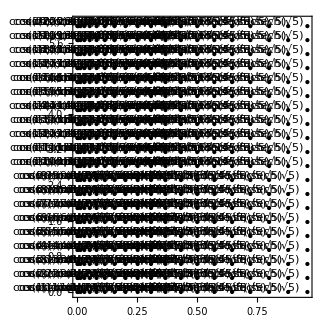

```mathematica
p1=Show[Graphics[Table[Point[grid[[ii,1]]],{ii,1,size}]],PlotRange->All,AspectRatio->1];

p2=Show[Graphics[Table[Text[grid[[ii,2]],{0.03,0.1}+grid[[ii,1]]],{ii,1,size}]],PlotRange->All,AspectRatio->1];

Show[p1,p2,Frame->True,FrameLabel->{"x","y"}]
```

## Compute derivatives

```mathematica
fval=Table[array[[ii,jj,2]],{ii,1,NX},{jj,1,NY}];
```

```mathematica
dxfval=Transpose[Table[DX.array[[All,ii,2]],{ii,1,NY}]];

dxxfval=Transpose[Table[DX2.array[[All,ii,2]],{ii,1,NY}]];
```

```mathematica
dyfval=Table[DY.array[[ii,All,2]],{ii,1,NX}];

dyyfval=Table[DY2.array[[ii,All,2]],{ii,1,NX}];
```

```mathematica
dxyfval=Transpose[Table[DX.dyfval[[All,ii]],{ii,1,NY}]];
```

Let us check the results;

## Check our discretization

```mathematica
fn[x_,y_]=Cos[y](1-0.5(1-x)^2);
```

```mathematica
fnx[x_,y_]=D[fn[x,y],x];

fny[x_,y_]=D[fn[x,y],y];

fnxx[x_,y_]=D[fn[x,y],{x,2}];

fnyy[x_,y_]=D[fn[x,y],{y,2}];

fnxy[x_,y_]=D[fn[x,y],x,y];
```

```mathematica
varrepl=Flatten[Table[array[[ii,jj,2]]->fn[xarr[[ii]],yarr[[jj]]],{ii,1,NX},{jj,1,NY}]]
```

{b[1]→0.5,b[2]→0.475528,b[3]→0.404508,b[4]→0.293893,b[5]→0.154508,b[6]→3.06162×10^-17,b[7]→-0.154508,b[8]→-0.293893,b[9]→-0.404508,b[10]→-0.475528,b[11]→-0.5,b[12]→-0.475528,b[13]→-0.404508,b[14]→-0.293893,b[15]→-0.154508,b[16]→-9.18485×10^-17,b[17]→0.154508,b[18]→0.293893,b[19]→0.404508,b[20]→0.475528,Cos[1]→0.503237,Cos[2]→0.478607,Cos[3]→0.407128,Cos[4]→0.295796,Cos[5]→0.155509,Cos[6]→3.08144×10^-17,Cos[7]→-0.155509,Cos[8]→-0.295796,Cos[9]→-0.407128,Cos[10]→-0.478607,Cos[11]→-0.503237,Cos[12]→-0.478607,Cos[13]→-0.407128,Cos[14]→-0.295796,Cos[15]→-0.155509,Cos[16]→-9.24432×10^-17,Cos[17]→0.155509,Cos[18]→0.295796,Cos[19]→0.407128,Cos[20]→0.478607,Cos[1] Cosh[2 √5] Sech[√5]→0.512866,Cos[2] Cosh[2 √5] Sech[√5]→0.487764,Cos[3] Cosh[2 √5] Sech[√5]→0.414917,Cos[4] Cosh[2 √5] Sech[√5]→0.301455,Cos[5] Cosh[2 √5] Sech[√5]→0.158484,Cos[6] Cosh[2 √5] Sech[√5]→3.1404×10^-17,Cos[7] Cosh[2 √5] Sech[√5]→-0.158484,Cos[8] Cosh[2 √5] Sech[√5]→-0.301455,Cos[9] Cosh[2 √5] Sech[√5]→-0.414917,Cos[10] Cosh[2 √5] Sech[√5]→-0.487764,Cos[11] Cosh[2 √5] Sech[√5]→-0.512866,Cos[12] Cosh[2 √5] Sech[√5]→-0.487764,Cos[13] Cosh[2 √5] Sech[√5]→-0.414917,Cos[14] Cosh[2 √5] Sech[√5]→-0.301455,Cos[15] Cosh[2 √5] Sech[√5]→-0.158484,Cos[16] Cosh[2 √5] Sech[√5]→-9.42119×10^-17,Cos[17] Cosh[2 √5] Sech[√5]→0.158484,Cos[18] Cosh[2 √5] Sech[√5]→0.301455,Cos[19] Cosh[2 √5] Sech[√5]→0.414917,Cos[20] Cosh[2 √5] Sech[√5]→0.487764,Cos[1] Cosh[3 √5] Sech[√5]→0.528636,Cos[2] Cosh[3 √5] Sech[√5]→0.502763,Cos[3] Cosh[3 √5] Sech[√5]→0.427676,Cos[4] Cosh[3 √5] Sech[√5]→0.310724,Cos[5] Cosh[3 √5] Sech[√5]→0.163358,Cos[6] Cosh[3 √5] Sech[√5]→3.23696×10^-17,Cos[7] Cosh[3 √5] Sech[√5]→-0.163358,Cos[8] Cosh[3 √5] Sech[√5]→-0.310724,Cos[9] Cosh[3 √5] Sech[√5]→-0.427676,Cos[10] Cosh[3 √5] Sech[√5]→-0.502763,Cos[11] Cosh[3 √5] Sech[√5]→-0.528636,Cos[12] Cosh[3 √5] Sech[√5]→-0.502763,Cos[13] Cosh[3 √5] Sech[√5]→-0.427676,Cos[14] Cosh[3 √5] Sech[√5]→-0.310724,Cos[15] Cosh[3 √5] Sech[√5]→-0.163358,Cos[16] Cosh[3 √5] Sech[√5]→-9.71089×10^-17,Cos[17] Cosh[3 √5] Sech[√5]→0.163358,Cos[18] Cosh[3 √5] Sech[√5]→0.310724,Cos[19] Cosh[3 √5] Sech[√5]→0.427676,Cos[20] Cosh[3 √5] Sech[√5]→0.502763,Cos[1] Cosh[4 √5] Sech[√5]→0.550139,Cos[2] Cosh[4 √5] Sech[√5]→0.523214,Cos[3] Cosh[4 √5] Sech[√5]→0.445072,Cos[4] Cosh[4 √5] Sech[√5]→0.323364,Cos[5] Cosh[4 √5] Sech[√5]→0.170002,Cos[6] Cosh[4 √5] Sech[√5]→3.36863×10^-17,Cos[7] Cosh[4 √5] Sech[√5]→-0.170002,Cos[8] Cosh[4 √5] Sech[√5]→-0.323364,Cos[9] Cosh[4 √5] Sech[√5]→-0.445072,Cos[10] Cosh[4 √5] Sech[√5]→-0.523214,Cos[11] Cosh[4 √5] Sech[√5]→-0.550139,Cos[12] Cosh[4 √5] Sech[√5]→-0.523214,Cos[13] Cosh[4 √5] Sech[√5]→-0.445072,Cos[14] Cosh[4 √5] Sech[√5]→-0.323364,Cos[15] Cosh[4 √5] Sech[√5]→-0.170002,Cos[16] Cosh[4 √5] Sech[√5]→-1.01059×10^-16,Cos[17] Cosh[4 √5] Sech[√5]→0.170002,Cos[18] Cosh[4 √5] Sech[√5]→0.323364,Cos[19] Cosh[4 √5] Sech[√5]→0.445072,Cos[20] Cosh[4 √5] Sech[√5]→0.523214,Cos[1] Cosh[5 √5] Sech[√5]→0.576819,Cos[2] Cosh[5 √5] Sech[√5]→0.548587,Cos[3] Cosh[5 √5] Sech[√5]→0.466656,Cos[4] Cosh[5 √5] Sech[√5]→0.339046,Cos[5] Cosh[5 √5] Sech[√5]→0.178247,Cos[6] Cosh[5 √5] Sech[√5]→3.532×10^-17,Cos[7] Cosh[5 √5] Sech[√5]→-0.178247,Cos[8] Cosh[5 √5] Sech[√5]→-0.339046,Cos[9] Cosh[5 √5] Sech[√5]→-0.466656,Cos[10] Cosh[5 √5] Sech[√5]→-0.548587,Cos[11] Cosh[5 √5] Sech[√5]→-0.576819,Cos[12] Cosh[5 √5] Sech[√5]→-0.548587,Cos[13] Cosh[5 √5] Sech[√5]→-0.466656,Cos[14] Cosh[5 √5] Sech[√5]→-0.339046,Cos[15] Cosh[5 √5] Sech[√5]→-0.178247,Cos[16] Cosh[5 √5] Sech[√5]→-1.0596×10^-16,Cos[17] Cosh[5 √5] Sech[√5]→0.178247,Cos[18] Cosh[5 √5] Sech[√5]→0.339046,Cos[19] Cosh[5 √5] Sech[√5]→0.466656,Cos[20] Cosh[5 √5] Sech[√5]→0.548587,Cos[1] Cosh[6 √5] Sech[√5]→0.607984,Cos[2] Cosh[6 √5] Sech[√5]→0.578227,Cos[3] Cosh[6 √5] Sech[√5]→0.491869,Cos[4] Cosh[6 √5] Sech[√5]→0.357364,Cos[5] Cosh[6 √5] Sech[√5]→0.187877,Cos[6] Cosh[6 √5] Sech[√5]→3.72283×10^-17,Cos[7] Cosh[6 √5] Sech[√5]→-0.187877,Cos[8] Cosh[6 √5] Sech[√5]→-0.357364,Cos[9] Cosh[6 √5] Sech[√5]→-0.491869,Cos[10] Cosh[6 √5] Sech[√5]→-0.578227,Cos[11] Cosh[6 √5] Sech[√5]→-0.607984,Cos[12] Cosh[6 √5] Sech[√5]→-0.578227,Cos[13] Cosh[6 √5] Sech[√5]→-0.491869,Cos[14] Cosh[6 √5] Sech[√5]→-0.357364,Cos[15] Cosh[6 √5] Sech[√5]→-0.187877,Cos[16] Cosh[6 √5] Sech[√5]→-1.11685×10^-16,Cos[17] Cosh[6 √5] Sech[√5]→0.187877,Cos[18] Cosh[6 √5] Sech[√5]→0.357364,Cos[19] Cosh[6 √5] Sech[√5]→0.491869,Cos[20] Cosh[6 √5] Sech[√5]→0.578227,Cos[1] Cosh[7 √5] Sech[√5]→0.642827,Cos[2] Cosh[7 √5] Sech[√5]→0.611365,Cos[3] Cosh[7 √5] Sech[√5]→0.520058,Cos[4] Cosh[7 √5] Sech[√5]→0.377844,Cos[5] Cosh[7 √5] Sech[√5]→0.198644,Cos[6] Cosh[7 √5] Sech[√5]→3.93618×10^-17,Cos[7] Cosh[7 √5] Sech[√5]→-0.198644,Cos[8] Cosh[7 √5] Sech[√5]→-0.377844,Cos[9] Cosh[7 √5] Sech[√5]→-0.520058,Cos[10] Cosh[7 √5] Sech[√5]→-0.611365,Cos[11] Cosh[7 √5] Sech[√5]→-0.642827,Cos[12] Cosh[7 √5] Sech[√5]→-0.611365,Cos[13] Cosh[7 √5] Sech[√5]→-0.520058,Cos[14] Cosh[7 √5] Sech[√5]→-0.377844,Cos[15] Cosh[7 √5] Sech[√5]→-0.198644,Cos[16] Cosh[7 √5] Sech[√5]→-1.18085×10^-16,Cos[17] Cosh[7 √5] Sech[√5]→0.198644,Cos[18] Cosh[7 √5] Sech[√5]→0.377844,Cos[19] Cosh[7 √5] Sech[√5]→0.520058,Cos[20] Cosh[7 √5] Sech[√5]→0.611365,Cos[1] Cosh[8 √5] Sech[√5]→0.680446,Cos[2] Cosh[8 √5] Sech[√5]→0.647142,Cos[3] Cosh[8 √5] Sech[√5]→0.550492,Cos[4] Cosh[8 √5] Sech[√5]→0.399956,Cos[5] Cosh[8 √5] Sech[√5]→0.210269,Cos[6] Cosh[8 √5] Sech[√5]→4.16653×10^-17,Cos[7] Cosh[8 √5] Sech[√5]→-0.210269,Cos[8] Cosh[8 √5] Sech[√5]→-0.399956,Cos[9] Cosh[8 √5] Sech[√5]→-0.550492,Cos[10] Cosh[8 √5] Sech[√5]→-0.647142,Cos[11] Cosh[8 √5] Sech[√5]→-0.680446,Cos[12] Cosh[8 √5] Sech[√5]→-0.647142,Cos[13] Cosh[8 √5] Sech[√5]→-0.550492,Cos[14] Cosh[8 √5] Sech[√5]→-0.399956,Cos[15] Cosh[8 √5] Sech[√5]→-0.210269,Cos[16] Cosh[8 √5] Sech[√5]→-1.24996×10^-16,Cos[17] Cosh[8 √5] Sech[√5]→0.210269,Cos[18] Cosh[8 √5] Sech[√5]→0.399956,Cos[19] Cosh[8 √5] Sech[√5]→0.550492,Cos[20] Cosh[8 √5] Sech[√5]→0.647142,Cos[1] Cosh[9 √5] Sech[√5]→0.719866,Cos[2] Cosh[9 √5] Sech[√5]→0.684633,Cos[3] Cosh[9 √5] Sech[√5]→0.582384,Cos[4] Cosh[9 √5] Sech[√5]→0.423127,Cos[5] Cosh[9 √5] Sech[√5]→0.222451,Cos[6] Cosh[9 √5] Sech[√5]→4.40791×10^-17,Cos[7] Cosh[9 √5] Sech[√5]→-0.222451,Cos[8] Cosh[9 √5] Sech[√5]→-0.423127,Cos[9] Cosh[9 √5] Sech[√5]→-0.582384,Cos[10] Cosh[9 √5] Sech[√5]→-0.684633,Cos[11] Cosh[9 √5] Sech[√5]→-0.719866,Cos[12] Cosh[9 √5] Sech[√5]→-0.684633,Cos[13] Cosh[9 √5] Sech[√5]→-0.582384,Cos[14] Cosh[9 √5] Sech[√5]→-0.423127,Cos[15] Cosh[9 √5] Sech[√5]→-0.222451,Cos[16] Cosh[9 √5] Sech[√5]→-1.32237×10^-16,Cos[17] Cosh[9 √5] Sech[√5]→0.222451,Cos[18] Cosh[9 √5] Sech[√5]→0.423127,Cos[19] Cosh[9 √5] Sech[√5]→0.582384,Cos[20] Cosh[9 √5] Sech[√5]→0.684633,Cos[1] Cosh[10 √5] Sech[√5]→0.760066,Cos[2] Cosh[10 √5] Sech[√5]→0.722866,Cos[3] Cosh[10 √5] Sech[√5]→0.614907,Cos[4] Cosh[10 √5] Sech[√5]→0.446756,Cos[5] Cosh[10 √5] Sech[√5]→0.234873,Cos[6] Cosh[10 √5] Sech[√5]→4.65406×10^-17,Cos[7] Cosh[10 √5] Sech[√5]→-0.234873,Cos[8] Cosh[10 √5] Sech[√5]→-0.446756,Cos[9] Cosh[10 √5] Sech[√5]→-0.614907,Cos[10] Cosh[10 √5] Sech[√5]→-0.722866,Cos[11] Cosh[10 √5] Sech[√5]→-0.760066,Cos[12] Cosh[10 √5] Sech[√5]→-0.722866,Cos[13] Cosh[10 √5] Sech[√5]→-0.614907,Cos[14] Cosh[10 √5] Sech[√5]→-0.446756,Cos[15] Cosh[10 √5] Sech[√5]→-0.234873,Cos[16] Cosh[10 √5] Sech[√5]→-1.39622×10^-16,Cos[17] Cosh[10 √5] Sech[√5]→0.234873,Cos[18] Cosh[10 √5] Sech[√5]→0.446756,Cos[19] Cosh[10 √5] Sech[√5]→0.614907,Cos[20] Cosh[10 √5] Sech[√5]→0.722866,Cos[1] Cosh[11 √5] Sech[√5]→0.800006,Cos[2] Cosh[11 √5] Sech[√5]→0.760851,Cos[3] Cosh[11 √5] Sech[√5]→0.647219,Cos[4] Cosh[11 √5] Sech[√5]→0.470232,Cos[5] Cosh[11 √5] Sech[√5]→0.247216,Cos[6] Cosh[11 √5] Sech[√5]→4.89863×10^-17,Cos[7] Cosh[11 √5] Sech[√5]→-0.247216,Cos[8] Cosh[11 √5] Sech[√5]→-0.470232,Cos[9] Cosh[11 √5] Sech[√5]→-0.647219,Cos[10] Cosh[11 √5] Sech[√5]→-0.760851,Cos[11] Cosh[11 √5] Sech[√5]→-0.800006,Cos[12] Cosh[11 √5] Sech[√5]→-0.760851,Cos[13] Cosh[11 √5] Sech[√5]→-0.647219,Cos[14] Cosh[11 √5] Sech[√5]→-0.470232,Cos[15] Cosh[11 √5] Sech[√5]→-0.247216,Cos[16] Cosh[11 √5] Sech[√5]→-1.46959×10^-16,Cos[17] Cosh[11 √5] Sech[√5]→0.247216,Cos[18] Cosh[11 √5] Sech[√5]→0.470232,Cos[19] Cosh[11 √5] Sech[√5]→0.647219,Cos[20] Cosh[11 √5] Sech[√5]→0.760851,Cos[1] Cosh[12 √5] Sech[√5]→0.838651,Cos[2] Cosh[12 √5] Sech[√5]→0.797605,Cos[3] Cosh[12 √5] Sech[√5]→0.678483,Cos[4] Cosh[12 √5] Sech[√5]→0.492947,Cos[5] Cosh[12 √5] Sech[√5]→0.259157,Cos[6] Cosh[12 √5] Sech[√5]→5.13526×10^-17,Cos[7] Cosh[12 √5] Sech[√5]→-0.259157,Cos[8] Cosh[12 √5] Sech[√5]→-0.492947,Cos[9] Cosh[12 √5] Sech[√5]→-0.678483,Cos[10] Cosh[12 √5] Sech[√5]→-0.797605,Cos[11] Cosh[12 √5] Sech[√5]→-0.838651,Cos[12] Cosh[12 √5] Sech[√5]→-0.797605,Cos[13] Cosh[12 √5] Sech[√5]→-0.678483,Cos[14] Cosh[12 √5] Sech[√5]→-0.492947,Cos[15] Cosh[12 √5] Sech[√5]→-0.259157,Cos[16] Cosh[12 √5] Sech[√5]→-1.54058×10^-16,Cos[17] Cosh[12 √5] Sech[√5]→0.259157,Cos[18] Cosh[12 √5] Sech[√5]→0.492947,Cos[19] Cosh[12 √5] Sech[√5]→0.678483,Cos[20] Cosh[12 √5] Sech[√5]→0.797605,Cos[1] Cosh[13 √5] Sech[√5]→0.875,Cos[2] Cosh[13 √5] Sech[√5]→0.832174,Cos[3] Cosh[13 √5] Sech[√5]→0.70789,Cos[4] Cosh[13 √5] Sech[√5]→0.514312,Cos[5] Cosh[13 √5] Sech[√5]→0.27039,Cos[6] Cosh[13 √5] Sech[√5]→5.35783×10^-17,Cos[7] Cosh[13 √5] Sech[√5]→-0.27039,Cos[8] Cosh[13 √5] Sech[√5]→-0.514312,Cos[9] Cosh[13 √5] Sech[√5]→-0.70789,Cos[10] Cosh[13 √5] Sech[√5]→-0.832174,Cos[11] Cosh[13 √5] Sech[√5]→-0.875,Cos[12] Cosh[13 √5] Sech[√5]→-0.832174,Cos[13] Cosh[13 √5] Sech[√5]→-0.70789,Cos[14] Cosh[13 √5] Sech[√5]→-0.514312,Cos[15] Cosh[13 √5] Sech[√5]→-0.27039,Cos[16] Cosh[13 √5] Sech[√5]→-1.60735×10^-16,Cos[17] Cosh[13 √5] Sech[√5]→0.27039,Cos[18] Cosh[13 √5] Sech[√5]→0.514312,Cos[19] Cosh[13 √5] Sech[√5]→0.70789,Cos[20] Cosh[13 √5] Sech[√5]→0.832174,Cos[1] Cosh[14 √5] Sech[√5]→0.908111,Cos[2] Cosh[14 √5] Sech[√5]→0.863665,Cos[3] Cosh[14 √5] Sech[√5]→0.734678,Cos[4] Cosh[14 √5] Sech[√5]→0.533774,Cos[5] Cosh[14 √5] Sech[√5]→0.280622,Cos[6] Cosh[14 √5] Sech[√5]→5.56058×10^-17,Cos[7] Cosh[14 √5] Sech[√5]→-0.280622,Cos[8] Cosh[14 √5] Sech[√5]→-0.533774,Cos[9] Cosh[14 √5] Sech[√5]→-0.734678,Cos[10] Cosh[14 √5] Sech[√5]→-0.863665,Cos[11] Cosh[14 √5] Sech[√5]→-0.908111,Cos[12] Cosh[14 √5] Sech[√5]→-0.863665,Cos[13] Cosh[14 √5] Sech[√5]→-0.734678,Cos[14] Cosh[14 √5] Sech[√5]→-0.533774,Cos[15] Cosh[14 √5] Sech[√5]→-0.280622,Cos[16] Cosh[14 √5] Sech[√5]→-1.66817×10^-16,Cos[17] Cosh[14 √5] Sech[√5]→0.280622,Cos[18] Cosh[14 √5] Sech[√5]→0.533774,Cos[19] Cosh[14 √5] Sech[√5]→0.734678,Cos[20] Cosh[14 √5] Sech[√5]→0.863665,Cos[1] Cosh[15 √5] Sech[√5]→0.937128,Cos[2] Cosh[15 √5] Sech[√5]→0.891261,Cos[3] Cosh[15 √5] Sech[√5]→0.758152,Cos[4] Cosh[15 √5] Sech[√5]→0.55083,Cos[5] Cosh[15 √5] Sech[√5]→0.289588,Cos[6] Cosh[15 √5] Sech[√5]→5.73825×10^-17,Cos[7] Cosh[15 √5] Sech[√5]→-0.289588,Cos[8] Cosh[15 √5] Sech[√5]→-0.55083,Cos[9] Cosh[15 √5] Sech[√5]→-0.758152,Cos[10] Cosh[15 √5] Sech[√5]→-0.891261,Cos[11] Cosh[15 √5] Sech[√5]→-0.937128,Cos[12] Cosh[15 √5] Sech[√5]→-0.891261,Cos[13] Cosh[15 √5] Sech[√5]→-0.758152,Cos[14] Cosh[15 √5] Sech[√5]→-0.55083,Cos[15] Cosh[15 √5] Sech[√5]→-0.289588,Cos[16] Cosh[15 √5] Sech[√5]→-1.72148×10^-16,Cos[17] Cosh[15 √5] Sech[√5]→0.289588,Cos[18] Cosh[15 √5] Sech[√5]→0.55083,Cos[19] Cosh[15 √5] Sech[√5]→0.758152,Cos[20] Cosh[15 √5] Sech[√5]→0.891261,Cos[1] Cosh[16 √5] Sech[√5]→0.961298,Cos[2] Cosh[16 √5] Sech[√5]→0.914248,Cos[3] Cosh[16 √5] Sech[√5]→0.777706,Cos[4] Cosh[16 √5] Sech[√5]→0.565037,Cos[5] Cosh[16 √5] Sech[√5]→0.297057,Cos[6] Cosh[16 √5] Sech[√5]→5.88625×10^-17,Cos[7] Cosh[16 √5] Sech[√5]→-0.297057,Cos[8] Cosh[16 √5] Sech[√5]→-0.565037,Cos[9] Cosh[16 √5] Sech[√5]→-0.777706,Cos[10] Cosh[16 √5] Sech[√5]→-0.914248,Cos[11] Cosh[16 √5] Sech[√5]→-0.961298,Cos[12] Cosh[16 √5] Sech[√5]→-0.914248,Cos[13] Cosh[16 √5] Sech[√5]→-0.777706,Cos[14] Cosh[16 √5] Sech[√5]→-0.565037,Cos[15] Cosh[16 √5] Sech[√5]→-0.297057,Cos[16] Cosh[16 √5] Sech[√5]→-1.76587×10^-16,Cos[17] Cosh[16 √5] Sech[√5]→0.297057,Cos[18] Cosh[16 √5] Sech[√5]→0.565037,Cos[19] Cosh[16 √5] Sech[√5]→0.777706,Cos[20] Cosh[16 √5] Sech[√5]→0.914248,Cos[1] Cosh[17 √5] Sech[√5]→0.979995,Cos[2] Cosh[17 √5] Sech[√5]→0.93203,Cos[3] Cosh[17 √5] Sech[√5]→0.792832,Cos[4] Cosh[17 √5] Sech[√5]→0.576027,Cos[5] Cosh[17 √5] Sech[√5]→0.302835,Cos[6] Cosh[17 √5] Sech[√5]→6.00074×10^-17,Cos[7] Cosh[17 √5] Sech[√5]→-0.302835,Cos[8] Cosh[17 √5] Sech[√5]→-0.576027,Cos[9] Cosh[17 √5] Sech[√5]→-0.792832,Cos[10] Cosh[17 √5] Sech[√5]→-0.93203,Cos[11] Cosh[17 √5] Sech[√5]→-0.979995,Cos[12] Cosh[17 √5] Sech[√5]→-0.93203,Cos[13] Cosh[17 √5] Sech[√5]→-0.792832,Cos[14] Cosh[17 √5] Sech[√5]→-0.576027,Cos[15] Cosh[17 √5] Sech[√5]→-0.302835,Cos[16] Cosh[17 √5] Sech[√5]→-1.80022×10^-16,Cos[17] Cosh[17 √5] Sech[√5]→0.302835,Cos[18] Cosh[17 √5] Sech[√5]→0.576027,Cos[19] Cosh[17 √5] Sech[√5]→0.792832,Cos[20] Cosh[17 √5] Sech[√5]→0.93203,Cos[1] Cosh[18 √5] Sech[√5]→0.992735,Cos[2] Cosh[18 √5] Sech[√5]→0.944148,Cos[3] Cosh[18 √5] Sech[√5]→0.80314,Cos[4] Cosh[18 √5] Sech[√5]→0.583515,Cos[5] Cosh[18 √5] Sech[√5]→0.306772,Cos[6] Cosh[18 √5] Sech[√5]→6.07875×10^-17,Cos[7] Cosh[18 √5] Sech[√5]→-0.306772,Cos[8] Cosh[18 √5] Sech[√5]→-0.583515,Cos[9] Cosh[18 √5] Sech[√5]→-0.80314,Cos[10] Cosh[18 √5] Sech[√5]→-0.944148,Cos[11] Cosh[18 √5] Sech[√5]→-0.992735,Cos[12] Cosh[18 √5] Sech[√5]→-0.944148,Cos[13] Cosh[18 √5] Sech[√5]→-0.80314,Cos[14] Cosh[18 √5] Sech[√5]→-0.583515,Cos[15] Cosh[18 √5] Sech[√5]→-0.306772,Cos[16] Cosh[18 √5] Sech[√5]→-1.82363×10^-16,Cos[17] Cosh[18 √5] Sech[√5]→0.306772,Cos[18] Cosh[18 √5] Sech[√5]→0.583515,Cos[19] Cosh[18 √5] Sech[√5]→0.80314,Cos[20] Cosh[18 √5] Sech[√5]→0.944148,Cos[1] Cosh[19 √5] Sech[√5]→0.999189,Cos[2] Cosh[19 √5] Sech[√5]→0.950286,Cos[3] Cosh[19 √5] Sech[√5]→0.808361,Cos[4] Cosh[19 √5] Sech[√5]→0.587309,Cos[5] Cosh[19 √5] Sech[√5]→0.308766,Cos[6] Cosh[19 √5] Sech[√5]→6.11827×10^-17,Cos[7] Cosh[19 √5] Sech[√5]→-0.308766,Cos[8] Cosh[19 √5] Sech[√5]→-0.587309,Cos[9] Cosh[19 √5] Sech[√5]→-0.808361,Cos[10] Cosh[19 √5] Sech[√5]→-0.950286,Cos[11] Cosh[19 √5] Sech[√5]→-0.999189,Cos[12] Cosh[19 √5] Sech[√5]→-0.950286,Cos[13] Cosh[19 √5] Sech[√5]→-0.808361,Cos[14] Cosh[19 √5] Sech[√5]→-0.587309,Cos[15] Cosh[19 √5] Sech[√5]→-0.308766,Cos[16] Cosh[19 √5] Sech[√5]→-1.83548×10^-16,Cos[17] Cosh[19 √5] Sech[√5]→0.308766,Cos[18] Cosh[19 √5] Sech[√5]→0.587309,Cos[19] Cosh[19 √5] Sech[√5]→0.808361,Cos[20] Cosh[19 √5] Sech[√5]→0.950286}

Check our discretized x derivatives; since we used 2nd order polynominal interpolation and fn is only quadratic in x this should agree (up to numerical precision).

```mathematica
Table[fnx[x,y]/.{x->xarr[[ii]],y->yarr[[jj]]},{ii,1,NX},{jj,1,NY}]

dxfval/.varrepl
```

{{1.,0.951057,0.809017,0.587785,0.309017,6.12323×10^-17,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,-1.83697×10^-16,0.309017,0.587785,0.809017,0.951057},{0.996757,0.947973,0.806394,0.585879,0.308015,6.10338×10^-17,-0.308015,-0.585879,-0.806394,-0.947973,-0.996757,-0.947973,-0.806394,-0.585879,-0.308015,-1.83101×10^-16,0.308015,0.585879,0.806394,0.947973},{0.98705,0.938741,0.79854,0.580174,0.305015,6.04394×10^-17,-0.305015,-0.580174,-0.79854,-0.938741,-0.98705,-0.938741,-0.79854,-0.580174,-0.305015,-1.81318×10^-16,0.305015,0.580174,0.79854,0.938741},{0.970942,0.923421,0.785508,0.570705,0.300038,5.9453×10^-17,-0.300038,-0.570705,-0.785508,-0.923421,-0.970942,-0.923421,-0.785508,-0.570705,-0.300038,-1.78359×10^-16,0.300038,0.570705,0.785508,0.923421},{0.948536,0.902112,0.767382,0.557536,0.293114,5.80811×10^-17,-0.293114,-0.557536,-0.767382,-0.902112,-0.948536,-0.902112,-0.767382,-0.557536,-0.293114,-1.74243×10^-16,0.293114,0.557536,0.767382,0.902112},{0.919979,0.874952,0.744279,0.54075,0.284289,5.63325×10^-17,-0.284289,-0.54075,-0.744279,-0.874952,-0.919979,-0.874952,-0.744279,-0.54075,-0.284289,-1.68997×10^-16,0.284289,0.54075,0.744279,0.874952},{0.885456,0.842119,0.716349,0.520458,0.273621,5.42185×10^-17,-0.273621,-0.520458,-0.716349,-0.842119,-0.885456,-0.842119,-0.716349,-0.520458,-0.273621,-1.62656×10^-16,0.273621,0.520458,0.716349,0.842119},{0.84519,0.803824,0.683773,0.49679,0.261178,5.1753×10^-17,-0.261178,-0.49679,-0.683773,-0.803824,-0.84519,-0.803824,-0.683773,-0.49679,-0.261178,-1.55259×10^-16,0.261178,0.49679,0.683773,0.803824},{0.799443,0.760315,0.646763,0.469901,0.247041,4.89518×10^-17,-0.247041,-0.469901,-0.646763,-0.760315,-0.799443,-0.760315,-0.646763,-0.469901,-0.247041,-1.46855×10^-16,0.247041,0.469901,0.646763,0.760315},{0.748511,0.711876,0.605558,0.439964,0.231303,4.58331×10^-17,-0.231303,-0.439964,-0.605558,-0.711876,-0.748511,-0.711876,-0.605558,-0.439964,-0.231303,-1.37499×10^-16,0.231303,0.439964,0.605558,0.711876},{0.692724,0.65882,0.560426,0.407173,0.214064,4.24171×10^-17,-0.214064,-0.407173,-0.560426,-0.65882,-0.692724,-0.65882,-0.560426,-0.407173,-0.214064,-1.27251×10^-16,0.214064,0.407173,0.560426,0.65882},{0.632445,0.601491,0.511659,0.371742,0.195436,3.87261×10^-17,-0.195436,-0.371742,-0.511659,-0.601491,-0.632445,-0.601491,-0.511659,-0.371742,-0.195436,-1.16178×10^-16,0.195436,0.371742,0.511659,0.601491},{0.568065,0.540262,0.459574,0.3339,0.175542,3.47839×10^-17,-0.175542,-0.3339,-0.459574,-0.540262,-0.568065,-0.540262,-0.459574,-0.3339,-0.175542,-1.04352×10^-16,0.175542,0.3339,0.459574,0.540262},{0.5,0.475528,0.404508,0.293893,0.154508,3.06162×10^-17,-0.154508,-0.293893,-0.404508,-0.475528,-0.5,-0.475528,-0.404508,-0.293893,-0.154508,-9.18485×10^-17,0.154508,0.293893,0.404508,0.475528},{0.428693,0.407711,0.34682,0.251979,0.132473,2.62498×10^-17,-0.132473,-0.251979,-0.34682,-0.407711,-0.428693,-0.407711,-0.34682,-0.251979,-0.132473,-7.87495×10^-17,0.132473,0.251979,0.34682,0.407711},{0.354605,0.337249,0.286881,0.208432,0.109579,2.17133×10^-17,-0.109579,-0.208432,-0.286881,-0.337249,-0.354605,-0.337249,-0.286881,-0.208432,-0.109579,-6.51399×10^-17,0.109579,0.208432,0.286881,0.337249},{0.278217,0.264601,0.225083,0.163532,0.0859739,1.70359×10^-17,-0.0859739,-0.163532,-0.225083,-0.264601,-0.278217,-0.264601,-0.225083,-0.163532,-0.0859739,-5.11077×10^-17,0.0859739,0.163532,0.225083,0.264601},{0.200026,0.190236,0.161824,0.117572,0.0618113,1.2248×10^-17,-0.0618113,-0.117572,-0.161824,-0.190236,-0.200026,-0.190236,-0.161824,-0.117572,-0.0618113,-3.67441×10^-17,0.0618113,0.117572,0.161824,0.190236},{0.120537,0.114637,0.0975162,0.0708497,0.0372479,7.38074×10^-18,-0.0372479,-0.0708497,-0.0975162,-0.114637,-0.120537,-0.114637,-0.0975162,-0.0708497,-0.0372479,-2.21422×10^-17,0.0372479,0.0708497,0.0975162,0.114637},{0.0402659,0.0382952,0.0325758,0.0236677,0.0124429,2.46558×10^-18,-0.0124429,-0.0236677,-0.0325758,-0.0382952,-0.0402659,-0.0382952,-0.0325758,-0.0236677,-0.0124429,-7.39673×10^-18,0.0124429,0.0236677,0.0325758,0.0382952}}

{{1.89191×10^16,-1.45717×10^16,-3.46654×10^16,-2.28878×10^16,9.93266×10^15,3.36211×10^16,2.63985×10^16,-5.0948×10^15,-3.19039×10^16,-2.93808×10^16,1.54969×10^14,2.95482×10^16,3.1775×10^16,4.78796×10^15,-2.66011×10^16,-3.35332×10^16,-9.63506×10^15,2.31215×10^16,3.46203×10^16,1.42893×10^16},{-9.52109×10^15,7.33325×10^15,1.74454×10^16,1.15184×10^16,-4.99864×10^15,-1.69199×10^16,-1.32851×10^16,2.56397×10^15,1.60557×10^16,1.47859×10^16,-7.79887×10^13,-1.48702×10^16,-1.59908×10^16,-2.40955×10^15,1.33871×10^16,1.68757×10^16,4.84887×10^15,-1.1636×10^16,-1.74227×10^16,-7.19114×10^15},{9.70894×10^15,-7.47793×10^15,-1.77896×10^16,-1.17456×10^16,5.09725×10^15,1.72537×10^16,1.35472×10^16,-2.61456×10^15,-1.63725×10^16,-1.50777×10^16,7.95274×10^13,1.51636×10^16,1.63063×10^16,2.45709×10^15,-1.36512×10^16,-1.72086×10^16,-4.94453×10^15,1.18655×10^16,1.77665×10^16,7.33301×10^15},{-1.00331×10^16,7.72764×10^15,1.83837×10^16,1.21378×10^16,-5.26746×10^15,-1.78299×10^16,-1.39996×10^16,2.70186×10^15,1.69192×10^16,1.55811×10^16,-8.2183×10^13,-1.56699×10^16,-1.68508×10^16,-2.53914×10^15,1.4107×10^16,1.77833×10^16,5.10964×10^15,-1.22617×10^16,-1.83597×10^16,-7.57788×10^15},{1.05118×10^16,-8.09628×10^15,-1.92606×10^16,-1.27169×10^16,5.51874×10^15,1.86804×10^16,1.46674×10^16,-2.83075×10^15,-1.77264×10^16,-1.63244×10^16,8.61035×10^13,1.64175×10^16,1.76547×10^16,2.66027×10^15,-1.478×10^16,-1.86316×10^16,-5.3534×10^15,1.28467×10^16,1.92356×10^16,7.93938×10^15},{-1.11731×10^16,8.60563×10^15,2.04724×10^16,1.35169×10^16,-5.86594×10^15,-1.98556×10^16,-1.55902×10^16,3.00884×10^15,1.88415×10^16,1.73514×10^16,-9.15203×10^13,-1.74503×10^16,-1.87654×10^16,-2.82763×10^15,1.57098×10^16,1.98037×10^16,5.69019×10^15,-1.36549×10^16,-2.04457×10^16,-8.43885×10^15},{1.20593×10^16,-9.28819×10^15,-2.20961×10^16,-1.4589×10^16,6.3312×10^15,2.14305×10^16,1.68267×10^16,-3.24749×10^15,-2.0336×10^16,-1.87277×10^16,9.87794×10^13,1.88344×10^16,2.02538×10^16,3.05191×10^15,-1.69559×10^16,-2.13745×10^16,-6.14151×10^15,1.47379×10^16,2.20674×10^16,9.10819×10^15},{-1.32327×10^16,1.0192×10^16,2.42462×10^16,1.60086×10^16,-6.94726×10^15,-2.35158×10^16,-1.84641×10^16,3.56349×10^15,2.23148×10^16,2.055×10^16,-1.08391×10^14,-2.06671×10^16,-2.22246×10^16,-3.34887×10^15,1.86058×10^16,2.34543×10^16,6.73911×10^15,-1.6172×10^16,-2.42147×10^16,-9.99447×10^15},{1.47861×10^16,-1.13884×10^16,-2.70925×10^16,-1.78878×10^16,7.76279×10^15,2.62763×10^16,2.06315×10^16,-3.9818×10^15,-2.49343×10^16,-2.29623×10^16,1.21115×10^14,2.30932×10^16,2.48335×10^16,3.742×10^15,-2.07899×10^16,-2.62076×10^16,-7.53021×10^15,1.80704×10^16,2.70572×10^16,1.11677×10^16},{-1.686×10^16,1.29858×10^16,3.08925×10^16,2.03968×10^16,-8.85162×10^15,-2.99619×10^16,-2.35254×10^16,4.5403×10^15,2.84316×10^16,2.61831×10^16,-1.38103×10^14,-2.63323×10^16,-2.83167×10^16,-4.26686×10^15,2.37059×10^16,2.98836×10^16,8.58642×10^15,-2.06051×10^16,-3.08523×10^16,-1.27341×10^16},{1.96742×10^16,-1.51533×10^16,-3.60489×10^16,-2.38013×10^16,1.03291×10^16,3.4963×10^16,2.74521×10^16,-5.29814×10^15,-3.31773×10^16,-3.05534×10^16,1.61154×10^14,3.07275×10^16,3.30431×10^16,4.97905×10^15,-2.76627×10^16,-3.48715×10^16,-1.00196×10^16,2.40443×10^16,3.6002×10^16,1.48596×10^16},{-2.35851×10^16,1.81655×10^16,4.32149×10^16,2.85327×10^16,-1.23823×10^16,-4.19131×10^16,-3.29091×10^16,6.35133×10^15,3.97724×10^16,3.66269×10^16,-1.93189×10^14,-3.68357×10^16,-3.96116×10^16,-5.96882×10^15,3.31617×10^16,4.18035×10^16,1.20114×10^16,-2.8824×10^16,-4.31587×10^16,-1.78135×10^16},{2.92027×10^16,-2.24923×10^16,-5.3508×10^16,-3.53287×10^16,1.53316×10^16,5.18961×10^16,4.07476×10^16,-7.86411×10^15,-4.92456×10^16,-4.53509×10^16,2.39204×10^14,4.56094×10^16,4.90465×10^16,7.39049×10^15,-4.10603×10^16,-5.17604×10^16,-1.48723×10^16,3.56894×10^16,5.34384×10^16,2.20564×10^16},{-3.76225×10^16,2.89773×10^16,6.89355×10^16,4.55147×10^16,-1.97521×10^16,-6.68589×10^16,-5.2496×10^16,1.01315×10^16,6.34442×10^16,5.84265×10^16,-3.08172×10^14,-5.87595×10^16,-6.31877×10^16,-9.52134×10^15,5.28989×10^16,6.66841×10^16,1.91603×10^16,-4.59794×10^16,-6.88458×10^16,-2.84157×10^16},{5.11199×10^16,-3.93731×10^16,-9.36667×10^16,-6.18435×10^16,2.68383×10^16,9.08451×10^16,7.13294×10^16,-1.37663×10^16,-8.62053×10^16,-7.93875×10^16,4.18731×10^14,7.984×10^16,8.58568×10^16,1.29372×10^16,-7.18768×10^16,-9.06076×10^16,-2.60342×10^16,6.24749×10^16,9.35448×10^16,3.86101×10^16},{-7.36265×10^16,5.67079×10^16,1.34905×10^17,8.90714×10^16,-3.86544×10^16,-1.30841×10^17,-1.02734×10^17,1.98271×10^16,1.24159×10^17,1.14339×10^17,-6.03086×10^14,-1.14991×10^17,-1.23657×10^17,-1.8633×10^16,1.03522×10^17,1.30499×10^17,3.74962×10^16,-8.99807×10^16,-1.3473×10^17,-5.56089×10^16},{1.25136×10^17,-9.63812×10^16,-2.29286×10^17,-1.51386×10^17,6.56972×10^16,2.22379×10^17,1.74607×10^17,-3.36984×10^16,-2.11021×10^17,-1.94332×10^17,1.02501×10^15,1.9544×10^17,2.10168×10^17,3.16689×10^16,-1.75947×10^17,-2.21798×10^17,-6.37289×10^16,1.52932×10^17,2.28988×10^17,9.45134×10^16},{-1.73279×10^17,1.33461×10^17,3.17498×10^17,2.09628×10^17,-9.09726×10^16,-3.07934×10^17,-2.41782×10^17,4.6663×10^16,2.92206×10^17,2.69097×10^17,-1.41935×10^15,-2.7063×10^17,-2.91025×10^17,-4.38527×10^16,2.43638×10^17,3.07129×10^17,8.8247×10^16,-2.11769×10^17,-3.17085×10^17,-1.30875×10^17},{1.05182×10^18,-8.10124×10^17,-1.92724×10^18,-1.27246×10^18,5.52212×10^17,1.86919×10^18,1.46764×10^18,-2.83249×10^17,-1.77372×10^18,-1.63344×10^18,8.61562×10^15,1.64275×10^18,1.76655×10^18,2.6619×10^17,-1.4789×10^18,-1.8643×10^18,-5.35668×10^17,1.28546×10^18,1.92474×10^18,7.94424×10^17},{1.70241×10^18,-1.31122×10^18,-3.11932×10^18,-2.05953×10^18,8.93777×10^17,3.02535×10^18,2.37543×10^18,-4.58449×10^17,-2.87084×10^18,-2.64379×10^18,1.39447×10^16,2.65886×10^18,2.85923×10^18,4.30839×10^17,-2.39366×10^18,-3.01744×10^18,-8.66999×10^17,2.08056×10^18,3.11526×10^18,1.28581×10^18}}

```mathematica
Table[fnxx[x,y]/.{x->xarr[[ii]],y->yarr[[jj]]},{ii,1,NX},{jj,1,NY}]

dxxfval/.varrepl
```

{{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057},{-1.,-0.951057,-0.809017,-0.587785,-0.309017,-6.12323×10^-17,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,1.83697×10^-16,-0.309017,-0.587785,-0.809017,-0.951057}}

{{-1.91147×10^19,1.47224×10^19,3.50238×10^19,2.31245×10^19,-1.00354×10^19,-3.39688×10^19,-2.66715×10^19,5.14748×10^18,3.22339×10^19,2.96846×10^19,-1.56572×10^17,-2.98538×10^19,-3.21035×10^19,-4.83747×10^18,2.68761×10^19,3.388×10^19,9.73469×10^18,-2.33606×10^19,-3.49783×10^19,-1.44371×10^19},{-1.50384×10^18,1.15827×10^18,2.75548×10^18,1.81931×10^18,-7.89526×10^17,-2.67247×10^18,-2.09836×10^18,4.04975×10^17,2.53598×10^18,2.33541×10^18,-1.23182×10^16,-2.34872×10^18,-2.52572×10^18,-3.80585×10^17,2.11446×10^18,2.66548×10^18,7.65871×10^17,-1.83788×10^18,-2.75189×10^18,-1.13583×10^18},{4.117×10^17,-3.17096×10^17,-7.54355×10^17,-4.98063×10^17,2.16145×10^17,7.31631×10^17,5.74458×10^17,-1.10868×10^17,-6.94263×10^17,-6.39356×10^17,3.37229×10^15,6.43×10^17,6.91456×10^17,1.04191×10^17,-5.78867×10^17,-7.29717×10^17,-2.09669×10^17,5.03148×10^17,7.53373×10^17,3.1095×10^17},{-2.11348×10^17,1.62783×10^17,3.87252×10^17,2.55684×10^17,-1.10959×10^17,-3.75587×10^17,-2.94902×10^17,5.69148×10^16,3.56404×10^17,3.28217×10^17,-1.73119×10^15,-3.30088×10^17,-3.54963×10^17,-5.34871×10^16,2.97165×10^17,3.74605×10^17,1.07635×10^17,-2.58294×10^17,-3.86748×10^17,-1.59628×10^17},{1.43671×10^17,-1.10657×10^17,-2.63247×10^17,-1.73809×10^17,7.5428×10^16,2.55317×10^17,2.00468×10^17,-3.86896×10^16,-2.42277×10^17,-2.23116×10^17,1.17683×10^15,2.24387×10^17,2.41297×10^17,3.63595×10^16,-2.02007×10^17,-2.54649×10^17,-7.31681×10^16,1.75583×10^17,2.62904×10^17,1.08512×10^17},{-1.1538×10^17,8.88672×10^16,2.11411×10^17,1.39584×10^17,-6.05754×10^16,-2.05042×10^17,-1.60994×10^17,3.10712×10^16,1.9457×10^17,1.79182×10^17,-9.45097×10^14,-1.80203×10^17,-1.93783×10^17,-2.91999×10^16,1.6223×10^17,2.04506×10^17,5.87605×10^16,-1.41009×10^17,-2.11136×10^17,-8.7145×10^16},{1.03794×10^17,-7.99434×10^16,-1.90181×10^17,-1.25567×10^17,5.44926×10^16,1.84452×10^17,1.44827×10^17,-2.79511×10^16,-1.75032×10^17,-1.61189×10^17,8.50193×10^14,1.62108×10^17,1.74324×10^17,2.62677×10^16,-1.45939×10^17,-1.8397×10^17,-5.28599×10^16,1.26849×10^17,1.89934×10^17,7.83941×10^16},{-1.0162×10^17,7.82691×10^16,1.86198×10^17,1.22938×10^17,-5.33513×10^16,-1.80589×10^17,-1.41794×10^17,2.73657×10^16,1.71366×10^17,1.57813×10^17,-8.32387×10^14,-1.58712×10^17,-1.70673×10^17,-2.57176×10^16,1.42882×10^17,1.80117×10^17,5.17528×10^16,-1.24193×10^17,-1.85956×10^17,-7.67522×10^16},{1.06526×10^17,-8.20476×10^16,-1.95187×10^17,-1.28872×10^17,5.59269×10^16,1.89307×10^17,1.48639×10^17,-2.86868×10^16,-1.79639×10^17,-1.65431×10^17,8.72571×10^14,1.66374×10^17,1.78912×10^17,2.69591×10^16,-1.4978×10^17,-1.88812×10^17,-5.42512×10^16,1.30188×10^17,1.94933×10^17,8.04575×10^16},{-1.18506×10^17,9.12743×10^16,2.17137×10^17,1.43365×10^17,-6.22162×10^16,-2.10596×10^17,-1.65355×10^17,3.19128×10^16,1.9984×10^17,1.84035×10^17,-9.70697×10^14,-1.85084×10^17,-1.99032×10^17,-2.99908×10^16,1.66624×10^17,2.10045×10^17,6.03521×10^16,-1.44829×10^17,-2.16854×10^17,-8.95054×10^16},{1.39375×10^17,-1.07348×10^17,-2.55376×10^17,-1.68612×10^17,7.31728×10^16,2.47683×10^17,1.94475×10^17,-3.75328×10^16,-2.35033×10^17,-2.16445×10^17,1.14164×10^15,2.17678×10^17,2.34083×10^17,3.52724×10^16,-1.95967×10^17,-2.47035×10^17,-7.09804×10^16,1.70334×10^17,2.55044×10^17,1.05268×10^17},{-1.7334×10^17,1.33508×10^17,3.17609×10^17,2.09702×10^17,-9.10044×10^16,-3.08042×10^17,-2.41867×10^17,4.66793×10^16,2.92309×10^17,2.69191×10^17,-1.41985×10^15,-2.70725×10^17,-2.91127×10^17,-4.3868×10^16,2.43723×10^17,3.07236×10^17,8.82778×10^16,-2.11843×10^17,-3.17196×10^17,-1.30921×10^17},{2.28963×10^17,-1.7635×10^17,-4.19528×10^17,-2.76994×10^17,1.20207×10^17,4.0689×10^17,3.1948×10^17,-6.16584×10^16,-3.86109×10^17,-3.55572×10^17,1.87547×10^15,3.57599×10^17,3.84548×10^17,5.7945×10^16,-3.21932×10^17,-4.05826×10^17,-1.16606×10^17,2.79822×10^17,4.18982×10^17,1.72932×10^17},{-3.2363×10^17,2.49264×10^17,5.92986×10^17,3.91519×10^17,-1.69908×10^17,-5.75123×10^17,-4.51572×10^17,8.71516×10^16,5.45749×10^17,5.02587×10^17,-2.6509×10^15,-5.05452×10^17,-5.43542×10^17,-8.19028×10^16,4.55038×10^17,5.73619×10^17,1.64817×10^17,-3.95516×10^17,-5.92214×10^17,-2.44433×10^17},{5.00306×10^17,-3.85341×10^17,-9.16707×10^17,-6.05257×10^17,2.62664×10^17,8.89092×10^17,6.98094×10^17,-1.34729×10^17,-8.43683×10^17,-7.76958×10^17,4.09808×10^15,7.81386×10^17,8.40272×10^17,1.26615×10^17,-7.03451×10^17,-8.86767×10^17,-2.54794×10^17,6.11436×10^17,9.15514×10^17,3.77873×10^17},{-8.36425×10^17,6.44224×10^17,1.53258×10^18,1.01189×10^18,-4.39128×10^17,-1.48641×10^18,-1.16709×10^18,2.25244×10^17,1.41049×10^18,1.29894×10^18,-6.85128×10^15,-1.30634×10^18,-1.40479×10^18,-2.11679×10^17,1.17605×10^18,1.48252×10^18,4.25972×10^17,-1.02222×10^18,-1.53058×10^18,-6.31739×10^17},{1.8717×10^18,-1.4416×10^18,-3.4295×10^18,-2.26433×10^18,9.82654×10^17,3.32619×10^18,2.61164×10^18,-5.04037×10^17,-3.15631×10^18,-2.90668×10^18,1.53314×10^16,2.92325×10^18,3.14355×10^18,4.73681×10^17,-2.63169×10^18,-3.31749×10^18,-9.53212×10^17,2.28745×10^18,3.42504×10^18,1.41366×10^18},{-2.85809×10^18,2.20133×10^18,5.23686×10^18,3.45764×10^18,-1.50051×10^18,-5.0791×10^18,-3.98799×10^18,7.69665×10^17,4.81969×10^18,4.43852×10^18,-2.3411×10^16,-4.46381×10^18,-4.80021×10^18,-7.23312×10^17,4.01859×10^18,5.06582×10^18,1.45556×10^18,-3.49294×10^18,-5.23004×10^18,-2.15867×10^18},{2.99718×10^19,-2.30846×10^19,-5.49171×10^19,-3.62591×10^19,1.57354×10^19,5.32628×10^19,4.18206×10^19,-8.07121×10^18,-5.05424×10^19,-4.65451×10^19,2.45503×10^17,4.68104×10^19,5.03381×10^19,7.58511×10^18,-4.21416×10^19,-5.31235×10^19,-1.52639×10^19,3.66292×10^19,5.48456×10^19,2.26372×10^19},{-2.82743×10^19,2.17772×10^19,5.18068×10^19,3.42055×10^19,-1.48442×10^19,-5.02462×10^19,-3.94521×10^19,7.6141×10^18,4.76799×10^19,4.39091×10^19,-2.31599×10^17,-4.41593×10^19,-4.74872×10^19,-7.15553×10^18,3.97549×10^19,5.01148×10^19,1.43994×10^19,-3.45547×10^19,-5.17394×10^19,-2.13552×10^19}}

```mathematica
Table[fny[x,y]/.{x->xarr[[ii]],y->yarr[[jj]]},{ii,1,NX},{jj,1,NY}]//Chop

dyfval/.varrepl//Chop
```

{{0,-0.154508,-0.293893,-0.404508,-0.475528,-0.5,-0.475528,-0.404508,-0.293893,-0.154508,0,0.154508,0.293893,0.404508,0.475528,0.5,0.475528,0.404508,0.293893,0.154508},{0,-0.155509,-0.295796,-0.407128,-0.478607,-0.503237,-0.478607,-0.407128,-0.295796,-0.155509,0,0.155509,0.295796,0.407128,0.478607,0.503237,0.478607,0.407128,0.295796,0.155509},{0,-0.158484,-0.301455,-0.414917,-0.487764,-0.512866,-0.487764,-0.414917,-0.301455,-0.158484,0,0.158484,0.301455,0.414917,0.487764,0.512866,0.487764,0.414917,0.301455,0.158484},{0,-0.163358,-0.310724,-0.427676,-0.502763,-0.528636,-0.502763,-0.427676,-0.310724,-0.163358,0,0.163358,0.310724,0.427676,0.502763,0.528636,0.502763,0.427676,0.310724,0.163358},{0,-0.170002,-0.323364,-0.445072,-0.523214,-0.550139,-0.523214,-0.445072,-0.323364,-0.170002,0,0.170002,0.323364,0.445072,0.523214,0.550139,0.523214,0.445072,0.323364,0.170002},{0,-0.178247,-0.339046,-0.466656,-0.548587,-0.576819,-0.548587,-0.466656,-0.339046,-0.178247,0,0.178247,0.339046,0.466656,0.548587,0.576819,0.548587,0.466656,0.339046,0.178247},{0,-0.187877,-0.357364,-0.491869,-0.578227,-0.607984,-0.578227,-0.491869,-0.357364,-0.187877,0,0.187877,0.357364,0.491869,0.578227,0.607984,0.578227,0.491869,0.357364,0.187877},{0,-0.198644,-0.377844,-0.520058,-0.611365,-0.642827,-0.611365,-0.520058,-0.377844,-0.198644,0,0.198644,0.377844,0.520058,0.611365,0.642827,0.611365,0.520058,0.377844,0.198644},{0,-0.210269,-0.399956,-0.550492,-0.647142,-0.680446,-0.647142,-0.550492,-0.399956,-0.210269,0,0.210269,0.399956,0.550492,0.647142,0.680446,0.647142,0.550492,0.399956,0.210269},{0,-0.222451,-0.423127,-0.582384,-0.684633,-0.719866,-0.684633,-0.582384,-0.423127,-0.222451,0,0.222451,0.423127,0.582384,0.684633,0.719866,0.684633,0.582384,0.423127,0.222451},{0,-0.234873,-0.446756,-0.614907,-0.722866,-0.760066,-0.722866,-0.614907,-0.446756,-0.234873,0,0.234873,0.446756,0.614907,0.722866,0.760066,0.722866,0.614907,0.446756,0.234873},{0,-0.247216,-0.470232,-0.647219,-0.760851,-0.800006,-0.760851,-0.647219,-0.470232,-0.247216,0,0.247216,0.470232,0.647219,0.760851,0.800006,0.760851,0.647219,0.470232,0.247216},{0,-0.259157,-0.492947,-0.678483,-0.797605,-0.838651,-0.797605,-0.678483,-0.492947,-0.259157,0,0.259157,0.492947,0.678483,0.797605,0.838651,0.797605,0.678483,0.492947,0.259157},{0,-0.27039,-0.514312,-0.70789,-0.832174,-0.875,-0.832174,-0.70789,-0.514312,-0.27039,0,0.27039,0.514312,0.70789,0.832174,0.875,0.832174,0.70789,0.514312,0.27039},{0,-0.280622,-0.533774,-0.734678,-0.863665,-0.908111,-0.863665,-0.734678,-0.533774,-0.280622,0,0.280622,0.533774,0.734678,0.863665,0.908111,0.863665,0.734678,0.533774,0.280622},{0,-0.289588,-0.55083,-0.758152,-0.891261,-0.937128,-0.891261,-0.758152,-0.55083,-0.289588,0,0.289588,0.55083,0.758152,0.891261,0.937128,0.891261,0.758152,0.55083,0.289588},{0,-0.297057,-0.565037,-0.777706,-0.914248,-0.961298,-0.914248,-0.777706,-0.565037,-0.297057,0,0.297057,0.565037,0.777706,0.914248,0.961298,0.914248,0.777706,0.565037,0.297057},{0,-0.302835,-0.576027,-0.792832,-0.93203,-0.979995,-0.93203,-0.792832,-0.576027,-0.302835,0,0.302835,0.576027,0.792832,0.93203,0.979995,0.93203,0.792832,0.576027,0.302835},{0,-0.306772,-0.583515,-0.80314,-0.944148,-0.992735,-0.944148,-0.80314,-0.583515,-0.306772,0,0.306772,0.583515,0.80314,0.944148,0.992735,0.944148,0.80314,0.583515,0.306772},{0,-0.308766,-0.587309,-0.808361,-0.950286,-0.999189,-0.950286,-0.808361,-0.587309,-0.308766,0,0.308766,0.587309,0.808361,0.950286,0.999189,0.950286,0.808361,0.587309,0.308766}}

{{0,-0.154508,-0.293893,-0.404508,-0.475528,-0.5,-0.475528,-0.404508,-0.293893,-0.154508,0,0.154508,0.293893,0.404508,0.475528,0.5,0.475528,0.404508,0.293893,0.154508},{-0.731723,-3.82741,0.138729,1.99876,3.35076,0.670725,-1.93477,-3.25366,-1.25359,1.7167,3.15554,1.77936,-1.45639,-2.97979,-2.30963,1.24304,2.60813,3.05036,-1.56705,-0.398076},{-6.7699,-35.4112,1.28352,18.4925,31.0013,6.20555,-17.9005,-30.1029,-11.5982,15.8829,29.195,16.4626,-13.4746,-27.569,-21.3687,11.5006,24.1304,28.222,-14.4984,-3.68301},{-63.3342,-331.281,12.0077,173.002,290.025,58.0545,-167.464,-281.62,-108.505,148.588,273.127,154.012,-126.058,-257.915,-199.91,107.591,225.746,264.024,-135.636,-34.4555},{-592.584,-3099.62,112.349,1618.69,2713.61,543.185,-1566.87,-2634.97,-1015.22,1390.26,2555.5,1441.01,-1179.46,-2413.17,-1870.45,1006.67,2112.18,2470.33,-1269.07,-322.381},{-5544.49,-29001.5,1051.19,15145.2,25389.8,5082.29,-14660.3,-24654.,-9498.86,13007.9,23910.5,13482.7,-11035.5,-22578.8,-17500.8,9418.87,19762.6,23113.5,-11874.,-3016.35},{-51876.9,-271351.,9835.45,141706.,237559.,47552.3,-137169.,-230674.,-88875.8,121708.,223718.,126151.,-103254.,-211258.,-163745.,88127.3,184908.,216261.,-111099.,-28222.4},{-485384.,-2.53889×10^6,92025.1,1.32587×10^6,2.22271×10^6,444922.,-1.28342×10^6,-2.1583×10^6,-831564.,1.13876×10^6,2.09321×10^6,1.18033×10^6,-966090.,-1.97663×10^6,-1.53208×10^6,824561.,1.73009×10^6,2.02344×10^6,-1.0395×10^6,-264062.},{-4.54148×10^6,-2.3755×10^7,861030.,1.24054×10^7,2.07967×10^7,4.16289×10^6,-1.20083×10^7,-2.0194×10^7,-7.7805×10^6,1.06548×10^7,1.9585×10^7,1.10437×10^7,-9.0392×10^6,-1.84942×10^7,-1.43349×10^7,7.71498×10^6,1.61875×10^7,1.89323×10^7,-9.72601×10^6,-2.47069×10^6},{-4.24922×10^7,-2.22263×10^8,8.0562×10^6,1.16071×10^8,1.94584×10^8,3.895×10^7,-1.12355×10^8,-1.88945×10^8,-7.2798×10^7,9.96911×10^7,1.83247×10^8,1.0333×10^8,-8.4575×10^7,-1.73041×10^8,-1.34124×10^8,7.21849×10^7,1.51458×10^8,1.77139×10^8,-9.10011×10^7,-2.31169×10^7},{-3.97577×10^8,-2.0796×10^9,7.53776×10^7,1.08601×10^9,1.82062×10^9,3.64434×10^8,-1.05124×10^9,-1.76786×10^9,-6.81132×10^8,9.32757×10^8,1.71454×10^9,9.66803×10^8,-7.91323×10^8,-1.61905×10^9,-1.25492×10^9,6.75396×10^8,1.41711×10^9,1.6574×10^9,-8.51449×10^8,-2.16293×10^8},{-3.71992×10^9,-1.94577×10^10,7.05268×10^8,1.01613×10^10,1.70346×10^10,3.40982×10^9,-9.83594×10^9,-1.65409×10^10,-6.37299×10^9,8.72731×10^9,1.60421×10^10,9.04586×10^9,-7.40399×10^9,-1.51486×10^10,-1.17417×10^10,6.31932×10^9,1.32591×10^10,1.55074×10^10,-7.96655×10^9,-2.02373×10^9},{-3.48053×10^10,-1.82055×10^11,6.59882×10^9,9.50735×10^10,1.59383×10^11,3.19039×10^10,-9.20296×10^10,-1.54764×10^11,-5.96287×10^10,8.16568×10^10,1.50097×10^11,8.46373×10^10,-6.92752×10^10,-1.41737×10^11,-1.0986×10^11,5.91265×10^10,1.24059×10^11,1.45094×10^11,-7.45388×10^10,-1.8935×10^10},{-3.25655×10^11,-1.7034×10^12,6.17416×10^10,8.89552×10^11,1.49127×10^12,2.98508×10^11,-8.61072×10^11,-1.44805×10^12,-5.57914×10^11,7.64019×10^11,1.40438×10^12,7.91906×10^11,-6.48171×10^11,-1.32616×10^12,-1.02791×10^12,5.53216×10^11,1.16075×10^12,1.35757×10^12,-6.9742×10^11,-1.77165×10^11},{-3.04698×10^12,-1.59378×10^13,5.77684×10^11,8.32307×10^12,1.3953×10^13,2.79298×10^12,-8.0566×10^12,-1.35486×10^13,-5.22011×10^12,7.14852×10^12,1.314×10^13,7.40945×10^12,-6.06459×10^12,-1.24082×10^13,-9.61757×10^12,5.17615×10^12,1.08605×10^13,1.27021×10^13,-6.52539×10^12,-1.65764×10^12},{-2.8509×10^13,-1.49121×10^14,5.40508×10^12,7.78745×10^13,1.30551×10^14,2.61324×10^13,-7.53813×10^13,-1.26767×10^14,-4.88418×10^13,6.68849×10^13,1.22944×10^14,6.93263×10^13,-5.67432×10^13,-1.16097×10^14,-8.99865×10^13,4.84304×10^13,1.01616×10^14,1.18846×10^14,-6.10546×10^13,-1.55096×10^13},{-2.66743×10^14,-1.39525×10^15,5.05725×10^13,7.28631×10^14,1.22149×10^15,2.44507×10^14,-7.05303×10^14,-1.18609×10^15,-4.56986×10^14,6.25807×10^14,1.15032×10^15,6.48649×10^14,-5.30916×10^14,-1.08626×10^15,-8.41956×10^14,4.53138×10^14,9.5077×10^14,1.11198×10^15,-5.71255×10^14,-1.45115×10^14},{-2.49578×10^15,-1.30546×10^16,4.7318×10^14,6.81741×10^15,1.14289×10^16,2.28772×10^15,-6.59914×10^15,-1.10977×10^16,-4.27578×10^15,5.85534×10^15,1.0763×10^16,6.06906×10^15,-4.9675×10^15,-1.01635×10^16,-7.87773×10^15,4.23977×10^15,8.89585×10^15,1.04042×10^16,-5.34493×10^15,-1.35777×10^15},{-2.33516×10^16,-1.22145×10^17,4.42729×10^15,6.37869×10^16,1.06934×10^17,2.1405×10^16,-6.17447×10^16,-1.03835×10^17,-4.00062×10^16,5.47853×10^16,1.00703×10^17,5.6785×10^16,-4.64782×10^16,-9.50947×10^16,-7.37077×10^16,3.96693×10^16,8.32338×10^16,9.73469×10^16,-5.00097×10^16,-1.27039×10^16},{-2.18489×10^17,-1.14285×10^18,4.14238×10^16,5.9682×10^17,1.00052×10^18,2.00275×10^17,-5.77712×10^17,-9.71527×10^17,-3.74317×10^17,5.12597×10^17,9.42228×10^17,5.31307×10^17,-4.34872×10^17,-8.89751×10^17,-6.89644×10^17,3.71164×10^17,7.78774×10^17,9.10823×10^17,-4.67914×10^17,-1.18864×10^17}}

```mathematica
Table[fnyy[x,y]/.{x->xarr[[ii]],y->yarr[[jj]]},{ii,1,NX},{jj,1,NY}]//Chop

dyyfval/.varrepl//Chop
```

{{-0.5,-0.475528,-0.404508,-0.293893,-0.154508,0,0.154508,0.293893,0.404508,0.475528,0.5,0.475528,0.404508,0.293893,0.154508,0,-0.154508,-0.293893,-0.404508,-0.475528},{-0.503237,-0.478607,-0.407128,-0.295796,-0.155509,0,0.155509,0.295796,0.407128,0.478607,0.503237,0.478607,0.407128,0.295796,0.155509,0,-0.155509,-0.295796,-0.407128,-0.478607},{-0.512866,-0.487764,-0.414917,-0.301455,-0.158484,0,0.158484,0.301455,0.414917,0.487764,0.512866,0.487764,0.414917,0.301455,0.158484,0,-0.158484,-0.301455,-0.414917,-0.487764},{-0.528636,-0.502763,-0.427676,-0.310724,-0.163358,0,0.163358,0.310724,0.427676,0.502763,0.528636,0.502763,0.427676,0.310724,0.163358,0,-0.163358,-0.310724,-0.427676,-0.502763},{-0.550139,-0.523214,-0.445072,-0.323364,-0.170002,0,0.170002,0.323364,0.445072,0.523214,0.550139,0.523214,0.445072,0.323364,0.170002,0,-0.170002,-0.323364,-0.445072,-0.523214},{-0.576819,-0.548587,-0.466656,-0.339046,-0.178247,0,0.178247,0.339046,0.466656,0.548587,0.576819,0.548587,0.466656,0.339046,0.178247,0,-0.178247,-0.339046,-0.466656,-0.548587},{-0.607984,-0.578227,-0.491869,-0.357364,-0.187877,0,0.187877,0.357364,0.491869,0.578227,0.607984,0.578227,0.491869,0.357364,0.187877,0,-0.187877,-0.357364,-0.491869,-0.578227},{-0.642827,-0.611365,-0.520058,-0.377844,-0.198644,0,0.198644,0.377844,0.520058,0.611365,0.642827,0.611365,0.520058,0.377844,0.198644,0,-0.198644,-0.377844,-0.520058,-0.611365},{-0.680446,-0.647142,-0.550492,-0.399956,-0.210269,0,0.210269,0.399956,0.550492,0.647142,0.680446,0.647142,0.550492,0.399956,0.210269,0,-0.210269,-0.399956,-0.550492,-0.647142},{-0.719866,-0.684633,-0.582384,-0.423127,-0.222451,0,0.222451,0.423127,0.582384,0.684633,0.719866,0.684633,0.582384,0.423127,0.222451,0,-0.222451,-0.423127,-0.582384,-0.684633},{-0.760066,-0.722866,-0.614907,-0.446756,-0.234873,0,0.234873,0.446756,0.614907,0.722866,0.760066,0.722866,0.614907,0.446756,0.234873,0,-0.234873,-0.446756,-0.614907,-0.722866},{-0.800006,-0.760851,-0.647219,-0.470232,-0.247216,0,0.247216,0.470232,0.647219,0.760851,0.800006,0.760851,0.647219,0.470232,0.247216,0,-0.247216,-0.470232,-0.647219,-0.760851},{-0.838651,-0.797605,-0.678483,-0.492947,-0.259157,0,0.259157,0.492947,0.678483,0.797605,0.838651,0.797605,0.678483,0.492947,0.259157,0,-0.259157,-0.492947,-0.678483,-0.797605},{-0.875,-0.832174,-0.70789,-0.514312,-0.27039,0,0.27039,0.514312,0.70789,0.832174,0.875,0.832174,0.70789,0.514312,0.27039,0,-0.27039,-0.514312,-0.70789,-0.832174},{-0.908111,-0.863665,-0.734678,-0.533774,-0.280622,0,0.280622,0.533774,0.734678,0.863665,0.908111,0.863665,0.734678,0.533774,0.280622,0,-0.280622,-0.533774,-0.734678,-0.863665},{-0.937128,-0.891261,-0.758152,-0.55083,-0.289588,0,0.289588,0.55083,0.758152,0.891261,0.937128,0.891261,0.758152,0.55083,0.289588,0,-0.289588,-0.55083,-0.758152,-0.891261},{-0.961298,-0.914248,-0.777706,-0.565037,-0.297057,0,0.297057,0.565037,0.777706,0.914248,0.961298,0.914248,0.777706,0.565037,0.297057,0,-0.297057,-0.565037,-0.777706,-0.914248},{-0.979995,-0.93203,-0.792832,-0.576027,-0.302835,0,0.302835,0.576027,0.792832,0.93203,0.979995,0.93203,0.792832,0.576027,0.302835,0,-0.302835,-0.576027,-0.792832,-0.93203},{-0.992735,-0.944148,-0.80314,-0.583515,-0.306772,0,0.306772,0.583515,0.80314,0.944148,0.992735,0.944148,0.80314,0.583515,0.306772,0,-0.306772,-0.583515,-0.80314,-0.944148},{-0.999189,-0.950286,-0.808361,-0.587309,-0.308766,0,0.308766,0.587309,0.808361,0.950286,0.999189,0.950286,0.808361,0.587309,0.308766,0,-0.308766,-0.587309,-0.808361,-0.950286}}

{{-0.5,-0.475528,-0.404508,-0.293893,-0.154508,0,0.154508,0.293893,0.404508,0.475528,0.5,0.475528,0.404508,0.293893,0.154508,0,-0.154508,-0.293893,-0.404508,-0.475528},{-15.5239,4.75643,11.2726,4.76383,-0.735583,-12.0138,-5.26992,-0.943228,11.6762,6.04567,2.40916,-10.9885,-6.78841,-3.73443,9.94874,7.62555,4.52469,-7.6398,-11.5135,12.1282},{-143.627,44.0065,104.294,44.075,-6.80561,-111.152,-48.7574,-8.72675,108.028,55.9346,22.2895,-101.665,-62.8064,-34.551,92.0458,70.5517,41.8624,-70.6834,-106.523,112.21},{-1343.67,411.693,975.698,412.333,-63.6683,-1039.85,-456.138,-81.6411,1010.63,523.283,208.525,-951.105,-587.571,-323.234,861.112,660.029,391.634,-661.262,-996.549,1049.76},{-12572.,3851.98,9129.07,3857.97,-595.71,-9729.33,-4267.83,-763.871,9455.92,4896.07,1951.05,-8898.97,-5497.58,-3024.32,8056.96,6175.54,3664.31,-6187.07,-9324.17,9822.},{-117630.,36041.,85415.9,36097.,-5573.74,-91032.2,-39931.9,-7147.13,88474.,45809.9,18254.9,-83262.9,-51437.9,-28297.,75384.7,57781.2,34285.,-57889.1,-87241.3,91899.2},{-1.1006×10^6,337216.,799191.,337741.,-52150.5,-851740.,-373621.,-66871.9,827804.,428619.,170802.,-779047.,-481277.,-264760.,705335.,540628.,320786.,-541638.,-816271.,859852.},{-1.02977×10^7,3.15515×10^6,7.47761×10^6,3.16006×10^6,-487945.,-7.96928×10^6,-3.49578×10^6,-625685.,7.74532×10^6,4.01036×10^6,1.5981×10^6,-7.28913×10^6,-4.50306×10^6,-2.47722×10^6,6.59944×10^6,5.05837×10^6,3.00143×10^6,-5.06782×10^6,-7.63741×10^6,8.04518×10^6},{-9.63502×10^7,2.95211×10^7,6.9964×10^7,2.9567×10^7,-4.56544×10^6,-7.45643×10^7,-3.27081×10^7,-5.8542×10^6,7.24689×10^7,3.75228×10^7,1.49526×10^7,-6.82005×10^7,-4.21327×10^7,-2.3178×10^7,6.17475×10^7,4.73285×10^7,2.80827×10^7,-4.74169×10^7,-7.14592×10^7,7.52745×10^7},{-9.01498×10^8,2.76213×10^8,6.54616×10^8,2.76643×10^8,-4.27164×10^7,-6.97659×10^8,-3.06032×10^8,-5.47747×10^7,6.78053×10^8,3.51081×10^8,1.39903×10^8,-6.38116×10^8,-3.94213×10^8,-2.16864×10^8,5.77738×10^8,4.42827×10^8,2.62755×10^8,-4.43654×10^8,-6.68606×10^8,7.04303×10^8},{-8.43484×10^9,2.58438×10^9,6.1249×10^9,2.5884×10^9,-3.99675×10^8,-6.52762×10^9,-2.86338×10^9,-5.12498×10^8,6.34418×10^9,3.28488×10^9,1.309×10^9,-5.97051×10^9,-3.68845×10^9,-2.02908×10^9,5.40559×10^9,4.1433×10^9,2.45846×10^9,-4.15104×10^9,-6.25579×10^9,6.58979×10^9},{-7.89203×10^10,2.41807×10^10,5.73074×10^10,2.42183×10^10,-3.73954×10^9,-6.10755×10^10,-2.67912×10^10,-4.79517×10^9,5.93591×10^10,3.07349×10^10,1.22476×10^10,-5.58629×10^10,-3.45108×10^10,-1.8985×10^10,5.05772×10^10,3.87667×10^10,2.30025×10^10,-3.88391×10^10,-5.85321×10^10,6.16572×10^10},{-7.38415×10^11,2.26246×10^11,5.36195×10^11,2.26598×10^11,-3.49889×10^10,-5.71451×10^11,-2.50671×10^11,-4.48658×10^10,5.55392×10^11,2.8757×10^11,1.14595×10^11,-5.2268×10^11,-3.22899×10^11,-1.77633×10^11,4.73224×10^11,3.62719×10^11,2.15222×10^11,-3.63397×10^11,-5.47654×10^11,5.76893×10^11},{-6.90896×10^12,2.11686×10^12,5.01689×10^12,2.12015×10^12,-3.27373×10^11,-5.34676×10^12,-2.34539×10^12,-4.19786×10^11,5.19651×10^12,2.69064×10^12,1.0722×10^12,-4.89043×10^12,-3.0212×10^12,-1.66202×10^12,4.42771×10^12,3.39377×10^12,2.01372×10^12,-3.40011×10^12,-5.12411×10^12,5.39769×10^12},{-6.46435×10^13,1.98063×10^13,4.69404×10^13,1.98371×10^13,-3.06305×10^12,-5.00268×10^13,-2.19446×10^13,-3.92771×10^12,4.8621×10^13,2.51749×10^13,1.0032×10^13,-4.57572×10^13,-2.82678×10^13,-1.55506×10^13,4.14277×10^13,3.17537×10^13,1.88413×10^13,-3.1813×10^13,-4.79435×10^13,5.05033×10^13},{-6.04835×10^14,1.85317×10^14,4.39196×10^14,1.85606×10^14,-2.86594×10^13,-4.68074×10^14,-2.05324×10^14,-3.67495×10^13,4.5492×10^14,2.35548×10^14,9.38643×10^13,-4.28126×10^14,-2.64486×10^14,-1.45499×10^14,3.87617×10^14,2.97103×10^14,1.76288×10^14,-2.97657×10^14,-4.48582×10^14,4.72532×10^14},{-5.65912×10^15,1.73392×10^15,4.10933×10^15,1.73661×10^15,-2.6815×10^14,-4.37952×10^15,-1.92111×10^15,-3.43846×10^14,4.25645×10^15,2.2039×10^15,8.78238×10^14,-4.00575×10^15,-2.47466×10^15,-1.36136×10^15,3.62673×10^15,2.77983×10^15,1.64944×10^15,-2.78502×10^15,-4.19715×10^15,4.42123×10^15},{-5.29494×10^16,1.62233×10^16,3.84488×10^16,1.62486×10^16,-2.50894×10^15,-4.09769×10^16,-1.79748×10^16,-3.21718×10^15,3.98253×10^16,2.06207×10^16,8.21721×10^15,-3.74796×10^16,-2.31541×10^16,-1.27375×10^16,3.39334×10^16,2.60094×10^16,1.54329×10^16,-2.6058×10^16,-3.92705×10^16,4.13671×10^16},{-4.95419×10^17,1.51793×10^17,3.59745×10^17,1.52029×10^17,-2.34748×10^16,-3.83399×10^17,-1.6818×10^17,-3.01015×10^16,3.72624×10^17,1.92937×10^17,7.68841×10^16,-3.50677×10^17,-2.1664×10^17,-1.19178×10^17,3.17497×10^17,2.43356×10^17,1.44397×10^17,-2.43811×10^17,-3.67433×10^17,3.8705×10^17},{-4.63537×10^18,1.42025×10^18,3.36594×10^18,1.42246×10^18,-2.19642×10^17,-3.58726×10^18,-1.57357×10^18,-2.81643×10^17,3.48645×10^18,1.80521×10^18,7.19363×10^17,-3.2811×10^18,-2.02699×10^18,-1.11508×10^18,2.97065×10^18,2.27695×10^18,1.35105×10^18,-2.28121×10^18,-3.43787×10^18,3.62143×10^18}}

```mathematica
Table[fnxy[x,y]/.{x->xarr[[ii]],y->yarr[[jj]]},{ii,1,NX},{jj,1,NY}]//Chop

dxyfval/.varrepl//Chop
```

{{0,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,0,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017},{0,-0.308015,-0.585879,-0.806394,-0.947973,-0.996757,-0.947973,-0.806394,-0.585879,-0.308015,0,0.308015,0.585879,0.806394,0.947973,0.996757,0.947973,0.806394,0.585879,0.308015},{0,-0.305015,-0.580174,-0.79854,-0.938741,-0.98705,-0.938741,-0.79854,-0.580174,-0.305015,0,0.305015,0.580174,0.79854,0.938741,0.98705,0.938741,0.79854,0.580174,0.305015},{0,-0.300038,-0.570705,-0.785508,-0.923421,-0.970942,-0.923421,-0.785508,-0.570705,-0.300038,0,0.300038,0.570705,0.785508,0.923421,0.970942,0.923421,0.785508,0.570705,0.300038},{0,-0.293114,-0.557536,-0.767382,-0.902112,-0.948536,-0.902112,-0.767382,-0.557536,-0.293114,0,0.293114,0.557536,0.767382,0.902112,0.948536,0.902112,0.767382,0.557536,0.293114},{0,-0.284289,-0.54075,-0.744279,-0.874952,-0.919979,-0.874952,-0.744279,-0.54075,-0.284289,0,0.284289,0.54075,0.744279,0.874952,0.919979,0.874952,0.744279,0.54075,0.284289},{0,-0.273621,-0.520458,-0.716349,-0.842119,-0.885456,-0.842119,-0.716349,-0.520458,-0.273621,0,0.273621,0.520458,0.716349,0.842119,0.885456,0.842119,0.716349,0.520458,0.273621},{0,-0.261178,-0.49679,-0.683773,-0.803824,-0.84519,-0.803824,-0.683773,-0.49679,-0.261178,0,0.261178,0.49679,0.683773,0.803824,0.84519,0.803824,0.683773,0.49679,0.261178},{0,-0.247041,-0.469901,-0.646763,-0.760315,-0.799443,-0.760315,-0.646763,-0.469901,-0.247041,0,0.247041,0.469901,0.646763,0.760315,0.799443,0.760315,0.646763,0.469901,0.247041},{0,-0.231303,-0.439964,-0.605558,-0.711876,-0.748511,-0.711876,-0.605558,-0.439964,-0.231303,0,0.231303,0.439964,0.605558,0.711876,0.748511,0.711876,0.605558,0.439964,0.231303},{0,-0.214064,-0.407173,-0.560426,-0.65882,-0.692724,-0.65882,-0.560426,-0.407173,-0.214064,0,0.214064,0.407173,0.560426,0.65882,0.692724,0.65882,0.560426,0.407173,0.214064},{0,-0.195436,-0.371742,-0.511659,-0.601491,-0.632445,-0.601491,-0.511659,-0.371742,-0.195436,0,0.195436,0.371742,0.511659,0.601491,0.632445,0.601491,0.511659,0.371742,0.195436},{0,-0.175542,-0.3339,-0.459574,-0.540262,-0.568065,-0.540262,-0.459574,-0.3339,-0.175542,0,0.175542,0.3339,0.459574,0.540262,0.568065,0.540262,0.459574,0.3339,0.175542},{0,-0.154508,-0.293893,-0.404508,-0.475528,-0.5,-0.475528,-0.404508,-0.293893,-0.154508,0,0.154508,0.293893,0.404508,0.475528,0.5,0.475528,0.404508,0.293893,0.154508},{0,-0.132473,-0.251979,-0.34682,-0.407711,-0.428693,-0.407711,-0.34682,-0.251979,-0.132473,0,0.132473,0.251979,0.34682,0.407711,0.428693,0.407711,0.34682,0.251979,0.132473},{0,-0.109579,-0.208432,-0.286881,-0.337249,-0.354605,-0.337249,-0.286881,-0.208432,-0.109579,0,0.109579,0.208432,0.286881,0.337249,0.354605,0.337249,0.286881,0.208432,0.109579},{0,-0.0859739,-0.163532,-0.225083,-0.264601,-0.278217,-0.264601,-0.225083,-0.163532,-0.0859739,0,0.0859739,0.163532,0.225083,0.264601,0.278217,0.264601,0.225083,0.163532,0.0859739},{0,-0.0618113,-0.117572,-0.161824,-0.190236,-0.200026,-0.190236,-0.161824,-0.117572,-0.0618113,0,0.0618113,0.117572,0.161824,0.190236,0.200026,0.190236,0.161824,0.117572,0.0618113},{0,-0.0372479,-0.0708497,-0.0975162,-0.114637,-0.120537,-0.114637,-0.0975162,-0.0708497,-0.0372479,0,0.0372479,0.0708497,0.0975162,0.114637,0.120537,0.114637,0.0975162,0.0708497,0.0372479},{0,-0.0124429,-0.0236677,-0.0325758,-0.0382952,-0.0402659,-0.0382952,-0.0325758,-0.0236677,-0.0124429,0,0.0124429,0.0236677,0.0325758,0.0382952,0.0402659,0.0382952,0.0325758,0.0236677,0.0124429}}

{{-2.56218×10^16,-1.3402×10^17,4.8577×10^15,6.99881×10^16,1.1733×10^17,2.3486×10^16,-6.77474×10^16,-1.13929×10^17,-4.38955×10^16,6.01114×10^16,1.10494×10^17,6.23055×10^16,-5.09968×10^16,-1.0434×10^17,-8.08735×10^16,4.35259×10^16,9.13256×10^16,1.06811×10^17,-5.48716×10^16,-1.3939×10^16},{1.28943×10^16,6.74458×10^16,-2.44465×10^15,-3.52217×10^16,-5.90465×10^16,-1.18194×10^16,3.40941×10^16,5.73353×10^16,2.20905×10^16,-3.02512×10^16,-5.56062×10^16,-3.13554×10^16,2.56643×10^16,5.25092×10^16,4.06998×10^16,-2.19045×10^16,-4.59598×10^16,-5.37528×10^16,2.76143×10^16,7.01482×10^15},{-1.31487×10^16,-6.87764×10^16,2.49288×10^15,3.59166×10^16,6.02114×10^16,1.20526×10^16,-3.47667×10^16,-5.84665×10^16,-2.25264×10^16,3.08481×10^16,5.67033×10^16,3.1974×10^16,-2.61706×10^16,-5.35452×10^16,-4.15028×10^16,2.23367×10^16,4.68666×10^16,5.48133×10^16,-2.81591×10^16,-7.15322×10^15},{1.35877×10^16,7.1073×10^16,-2.57613×10^15,-3.71159×10^16,-6.2222×10^16,-1.2455×10^16,3.59276×10^16,6.04188×10^16,2.32786×10^16,-3.18782×10^16,-5.85967×10^16,-3.30417×10^16,2.70445×10^16,5.53332×10^16,4.28886×10^16,-2.30825×10^16,-4.84316×10^16,-5.66437×10^16,2.90994×10^16,7.39208×10^15},{-1.42359×10^16,-7.44635×10^16,2.69902×10^15,3.88865×10^16,6.51903×10^16,1.30492×10^16,-3.76416×10^16,-6.33011×10^16,-2.43891×10^16,3.33989×10^16,6.1392×10^16,3.4618×10^16,-2.83346×10^16,-5.79728×10^16,-4.49346×10^16,2.41837×10^16,5.0742×10^16,5.93458×10^16,-3.04875×10^16,-7.74471×10^15},{1.51315×10^16,7.91481×10^16,-2.86882×10^15,-4.13329×10^16,-6.92915×10^16,-1.38701×10^16,4.00096×10^16,6.72834×10^16,2.59234×10^16,-3.55001×10^16,-6.52543×10^16,-3.67958×10^16,3.01172×10^16,6.16199×10^16,4.77615×10^16,-2.57051×10^16,-5.39342×10^16,-6.30793×10^16,3.24055×10^16,8.23194×10^15},{-1.63317×10^16,-8.54258×10^16,3.09636×10^15,4.46113×10^16,7.47874×10^16,1.49702×10^16,-4.3183×10^16,-7.26201×10^16,-2.79796×10^16,3.83158×10^16,7.043×10^16,3.97143×10^16,-3.2506×10^16,-6.65074×10^16,-5.15498×10^16,2.77439×10^16,5.82121×10^16,6.80825×10^16,-3.49758×10^16,-8.88487×10^15},{1.79208×10^16,9.37382×10^16,-3.39765×10^15,-4.89522×10^16,-8.20646×10^16,-1.64269×10^16,4.7385×10^16,7.96864×10^16,3.07021×10^16,-4.20441×10^16,-7.72832×10^16,-4.35788×10^16,3.5669×10^16,7.29789×10^16,5.65658×10^16,-3.04436×10^16,-6.38764×10^16,-7.47074×10^16,3.83792×10^16,9.74942×10^15},{-2.00246×10^16,-1.04742×10^17,3.7965×10^15,5.46987×10^16,9.16981×10^16,1.83553×10^16,-5.29475×10^16,-8.90407×10^16,-3.43062×10^16,4.69796×10^16,8.63554×10^16,4.86944×10^16,-3.98561×10^16,-8.15459×10^16,-6.32061×10^16,3.40173×10^16,7.13748×10^16,8.34772×10^16,-4.28845×10^16,-1.08939×10^16},{2.28333×10^16,1.19433×10^17,-4.32901×10^15,-6.23709×10^16,-1.0456×10^17,-2.09298×10^16,6.0374×10^16,1.0153×10^17,3.91181×10^16,-5.35691×10^16,-9.84679×10^16,-5.55244×10^16,4.54465×10^16,9.29837×10^16,7.20715×10^16,-3.87887×10^16,-8.13861×10^16,-9.51859×10^16,4.88996×10^16,1.24219×10^16},{-2.66444×10^16,-1.39369×10^17,5.05158×10^15,7.27814×10^16,1.22012×10^17,2.44233×10^16,-7.04513×10^16,-1.18476×10^17,-4.56474×10^16,6.25105×10^16,1.14904×10^17,6.47922×10^16,-5.30321×10^16,-1.08504×10^17,-8.41012×10^16,4.5263×10^16,9.49705×10^16,1.11074×10^17,-5.70615×10^16,-1.44953×10^16},{3.1941×10^16,1.67073×10^17,-6.05576×10^15,-8.72493×10^16,-1.46267×10^17,-2.92783×10^16,8.4456×10^16,1.42028×10^17,5.47215×10^16,-7.49367×10^16,-1.37745×10^17,-7.7672×10^16,6.35741×10^16,1.30073×10^17,1.00819×10^17,-5.42607×10^16,-1.13849×10^17,-1.33154×10^17,6.84046×10^16,1.73767×10^16},{-3.95488×10^16,-2.06867×10^17,7.49814×10^15,1.08031×10^17,1.81105×10^17,3.62519×10^16,-1.04572×10^17,-1.75857×10^17,-6.77553×10^16,9.27855×10^16,1.70553×10^17,9.61722×10^16,-7.87164×10^16,-1.61054×10^17,-1.24833×10^17,6.71847×10^16,1.40966×10^17,1.64869×10^17,-8.46974×10^16,-2.15156×10^16},{5.09516×10^16,2.66511×10^17,-9.66002×10^15,-1.39178×10^17,-2.33322×10^17,-4.67041×10^16,1.34722×10^17,2.2656×10^17,8.72906×10^16,-1.19538×10^17,-2.19727×10^17,-1.23901×10^17,1.01412×10^17,2.0749×10^17,1.60825×10^17,-8.65555×10^16,-1.8161×10^17,-2.12404×10^17,1.09118×10^17,2.7719×10^16},{-6.92309×10^16,-3.62125×10^17,1.31256×10^16,1.8911×10^17,3.17028×10^17,6.34596×10^16,-1.83055×10^17,-3.0784×10^17,-1.18607×10^17,1.62423×10^17,2.98556×10^17,1.68351×10^17,-1.37795×10^17,-2.81928×10^17,-2.18522×10^17,1.17608×10^17,2.46764×10^17,2.88606×10^17,-1.48264×10^17,-3.76634×10^16},{9.97111×10^16,5.21557×10^17,-1.89045×10^16,-2.72369×10^17,-4.56605×10^17,-9.1399×10^16,2.63649×10^17,4.43373×10^17,1.70826×10^17,-2.33932×10^17,-4.30002×10^17,-2.42471×10^17,1.98461×10^17,4.06053×10^17,3.14731×10^17,-1.69387×10^17,-3.55407×10^17,-4.1567×10^17,2.13541×10^17,5.42455×10^16},{-1.6947×10^17,-8.86442×10^17,3.21301×10^16,4.6292×10^17,7.7605×10^17,1.55342×10^17,-4.48099×10^17,-7.5356×10^17,-2.90337×10^17,3.97593×10^17,7.30834×10^17,4.12106×10^17,-3.37306×10^17,-6.9013×10^17,-5.34919×10^17,2.87892×10^17,6.04052×10^17,7.06475×10^17,-3.62935×10^17,-9.2196×10^16},{2.34669×10^17,1.22748×10^18,-4.44914×10^16,-6.41017×10^17,-1.07462×10^18,-2.15106×10^17,6.20494×10^17,1.04347×10^18,4.02037×10^17,-5.50557×10^17,-1.012×10^18,-5.70653×10^17,4.67076×10^17,9.55641×10^17,7.40715×10^17,-3.98651×10^17,-8.36446×10^17,-9.78274×10^17,5.02565×10^17,1.27666×10^17},{-1.42446×10^18,-7.45091×10^18,2.70067×10^17,3.89103×10^18,6.52302×10^18,1.30572×10^18,-3.76646×10^18,-6.33398×10^18,-2.4404×10^18,3.34193×10^18,6.14296×10^18,3.46392×10^18,-2.8352×10^18,-5.80083×10^18,-4.49621×10^18,2.41985×10^18,5.07731×10^18,5.93822×10^18,-3.05062×10^18,-7.74946×10^17},{-2.30555×10^18,-1.20596×10^19,4.37114×10^17,6.29779×10^18,1.05578×10^19,2.11335×10^18,-6.09616×10^18,-1.02518×10^19,-3.94988×10^18,5.40905×10^18,9.94263×10^18,5.60648×10^18,-4.58888×10^18,-9.38887×10^18,-7.2773×10^18,3.91662×10^18,8.21782×10^18,9.61123×10^18,-4.93755×10^18,-1.25428×10^18}}

## Implement boundary conditions, initial guess and p.d.e. to be solved.

```mathematica
bfn[x_,y_]=Cos[y];
```

This code creates the boundary and interior replacelists for the boundary condition at x=0 and the initial guess for the interior points respectively. Note that we are using the lists ' boundary' and ' interior' that we created initially when we built ' grid'.

```mathematica
boundaryrepl=Flatten[Table[array[[ii,jj,2]]->bfn[xarr[[ii]],yarr[[jj]]],{ii,1,1},{jj,1,NY}]]

interiorrepl=Flatten[Table[array[[ii,jj,2]]->bfn[xarr[[ii]],yarr[[jj]]],{ii,2,NX},{jj,1,NY}]]
```

{b[1]→1.,b[2]→0.951057,b[3]→0.809017,b[4]→0.587785,b[5]→0.309017,b[6]→6.12323×10^-17,b[7]→-0.309017,b[8]→-0.587785,b[9]→-0.809017,b[10]→-0.951057,b[11]→-1.,b[12]→-0.951057,b[13]→-0.809017,b[14]→-0.587785,b[15]→-0.309017,b[16]→-1.83697×10^-16,b[17]→0.309017,b[18]→0.587785,b[19]→0.809017,b[20]→0.951057}

{Cos[1]→1.,Cos[2]→0.951057,Cos[3]→0.809017,Cos[4]→0.587785,Cos[5]→0.309017,Cos[6]→6.12323×10^-17,Cos[7]→-0.309017,Cos[8]→-0.587785,Cos[9]→-0.809017,Cos[10]→-0.951057,Cos[11]→-1.,Cos[12]→-0.951057,Cos[13]→-0.809017,Cos[14]→-0.587785,Cos[15]→-0.309017,Cos[16]→-1.83697×10^-16,Cos[17]→0.309017,Cos[18]→0.587785,Cos[19]→0.809017,Cos[20]→0.951057,Cos[1] Cosh[2 √5] Sech[√5]→1.,Cos[2] Cosh[2 √5] Sech[√5]→0.951057,Cos[3] Cosh[2 √5] Sech[√5]→0.809017,Cos[4] Cosh[2 √5] Sech[√5]→0.587785,Cos[5] Cosh[2 √5] Sech[√5]→0.309017,Cos[6] Cosh[2 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[2 √5] Sech[√5]→-0.309017,Cos[8] Cosh[2 √5] Sech[√5]→-0.587785,Cos[9] Cosh[2 √5] Sech[√5]→-0.809017,Cos[10] Cosh[2 √5] Sech[√5]→-0.951057,Cos[11] Cosh[2 √5] Sech[√5]→-1.,Cos[12] Cosh[2 √5] Sech[√5]→-0.951057,Cos[13] Cosh[2 √5] Sech[√5]→-0.809017,Cos[14] Cosh[2 √5] Sech[√5]→-0.587785,Cos[15] Cosh[2 √5] Sech[√5]→-0.309017,Cos[16] Cosh[2 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[2 √5] Sech[√5]→0.309017,Cos[18] Cosh[2 √5] Sech[√5]→0.587785,Cos[19] Cosh[2 √5] Sech[√5]→0.809017,Cos[20] Cosh[2 √5] Sech[√5]→0.951057,Cos[1] Cosh[3 √5] Sech[√5]→1.,Cos[2] Cosh[3 √5] Sech[√5]→0.951057,Cos[3] Cosh[3 √5] Sech[√5]→0.809017,Cos[4] Cosh[3 √5] Sech[√5]→0.587785,Cos[5] Cosh[3 √5] Sech[√5]→0.309017,Cos[6] Cosh[3 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[3 √5] Sech[√5]→-0.309017,Cos[8] Cosh[3 √5] Sech[√5]→-0.587785,Cos[9] Cosh[3 √5] Sech[√5]→-0.809017,Cos[10] Cosh[3 √5] Sech[√5]→-0.951057,Cos[11] Cosh[3 √5] Sech[√5]→-1.,Cos[12] Cosh[3 √5] Sech[√5]→-0.951057,Cos[13] Cosh[3 √5] Sech[√5]→-0.809017,Cos[14] Cosh[3 √5] Sech[√5]→-0.587785,Cos[15] Cosh[3 √5] Sech[√5]→-0.309017,Cos[16] Cosh[3 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[3 √5] Sech[√5]→0.309017,Cos[18] Cosh[3 √5] Sech[√5]→0.587785,Cos[19] Cosh[3 √5] Sech[√5]→0.809017,Cos[20] Cosh[3 √5] Sech[√5]→0.951057,Cos[1] Cosh[4 √5] Sech[√5]→1.,Cos[2] Cosh[4 √5] Sech[√5]→0.951057,Cos[3] Cosh[4 √5] Sech[√5]→0.809017,Cos[4] Cosh[4 √5] Sech[√5]→0.587785,Cos[5] Cosh[4 √5] Sech[√5]→0.309017,Cos[6] Cosh[4 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[4 √5] Sech[√5]→-0.309017,Cos[8] Cosh[4 √5] Sech[√5]→-0.587785,Cos[9] Cosh[4 √5] Sech[√5]→-0.809017,Cos[10] Cosh[4 √5] Sech[√5]→-0.951057,Cos[11] Cosh[4 √5] Sech[√5]→-1.,Cos[12] Cosh[4 √5] Sech[√5]→-0.951057,Cos[13] Cosh[4 √5] Sech[√5]→-0.809017,Cos[14] Cosh[4 √5] Sech[√5]→-0.587785,Cos[15] Cosh[4 √5] Sech[√5]→-0.309017,Cos[16] Cosh[4 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[4 √5] Sech[√5]→0.309017,Cos[18] Cosh[4 √5] Sech[√5]→0.587785,Cos[19] Cosh[4 √5] Sech[√5]→0.809017,Cos[20] Cosh[4 √5] Sech[√5]→0.951057,Cos[1] Cosh[5 √5] Sech[√5]→1.,Cos[2] Cosh[5 √5] Sech[√5]→0.951057,Cos[3] Cosh[5 √5] Sech[√5]→0.809017,Cos[4] Cosh[5 √5] Sech[√5]→0.587785,Cos[5] Cosh[5 √5] Sech[√5]→0.309017,Cos[6] Cosh[5 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[5 √5] Sech[√5]→-0.309017,Cos[8] Cosh[5 √5] Sech[√5]→-0.587785,Cos[9] Cosh[5 √5] Sech[√5]→-0.809017,Cos[10] Cosh[5 √5] Sech[√5]→-0.951057,Cos[11] Cosh[5 √5] Sech[√5]→-1.,Cos[12] Cosh[5 √5] Sech[√5]→-0.951057,Cos[13] Cosh[5 √5] Sech[√5]→-0.809017,Cos[14] Cosh[5 √5] Sech[√5]→-0.587785,Cos[15] Cosh[5 √5] Sech[√5]→-0.309017,Cos[16] Cosh[5 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[5 √5] Sech[√5]→0.309017,Cos[18] Cosh[5 √5] Sech[√5]→0.587785,Cos[19] Cosh[5 √5] Sech[√5]→0.809017,Cos[20] Cosh[5 √5] Sech[√5]→0.951057,Cos[1] Cosh[6 √5] Sech[√5]→1.,Cos[2] Cosh[6 √5] Sech[√5]→0.951057,Cos[3] Cosh[6 √5] Sech[√5]→0.809017,Cos[4] Cosh[6 √5] Sech[√5]→0.587785,Cos[5] Cosh[6 √5] Sech[√5]→0.309017,Cos[6] Cosh[6 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[6 √5] Sech[√5]→-0.309017,Cos[8] Cosh[6 √5] Sech[√5]→-0.587785,Cos[9] Cosh[6 √5] Sech[√5]→-0.809017,Cos[10] Cosh[6 √5] Sech[√5]→-0.951057,Cos[11] Cosh[6 √5] Sech[√5]→-1.,Cos[12] Cosh[6 √5] Sech[√5]→-0.951057,Cos[13] Cosh[6 √5] Sech[√5]→-0.809017,Cos[14] Cosh[6 √5] Sech[√5]→-0.587785,Cos[15] Cosh[6 √5] Sech[√5]→-0.309017,Cos[16] Cosh[6 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[6 √5] Sech[√5]→0.309017,Cos[18] Cosh[6 √5] Sech[√5]→0.587785,Cos[19] Cosh[6 √5] Sech[√5]→0.809017,Cos[20] Cosh[6 √5] Sech[√5]→0.951057,Cos[1] Cosh[7 √5] Sech[√5]→1.,Cos[2] Cosh[7 √5] Sech[√5]→0.951057,Cos[3] Cosh[7 √5] Sech[√5]→0.809017,Cos[4] Cosh[7 √5] Sech[√5]→0.587785,Cos[5] Cosh[7 √5] Sech[√5]→0.309017,Cos[6] Cosh[7 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[7 √5] Sech[√5]→-0.309017,Cos[8] Cosh[7 √5] Sech[√5]→-0.587785,Cos[9] Cosh[7 √5] Sech[√5]→-0.809017,Cos[10] Cosh[7 √5] Sech[√5]→-0.951057,Cos[11] Cosh[7 √5] Sech[√5]→-1.,Cos[12] Cosh[7 √5] Sech[√5]→-0.951057,Cos[13] Cosh[7 √5] Sech[√5]→-0.809017,Cos[14] Cosh[7 √5] Sech[√5]→-0.587785,Cos[15] Cosh[7 √5] Sech[√5]→-0.309017,Cos[16] Cosh[7 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[7 √5] Sech[√5]→0.309017,Cos[18] Cosh[7 √5] Sech[√5]→0.587785,Cos[19] Cosh[7 √5] Sech[√5]→0.809017,Cos[20] Cosh[7 √5] Sech[√5]→0.951057,Cos[1] Cosh[8 √5] Sech[√5]→1.,Cos[2] Cosh[8 √5] Sech[√5]→0.951057,Cos[3] Cosh[8 √5] Sech[√5]→0.809017,Cos[4] Cosh[8 √5] Sech[√5]→0.587785,Cos[5] Cosh[8 √5] Sech[√5]→0.309017,Cos[6] Cosh[8 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[8 √5] Sech[√5]→-0.309017,Cos[8] Cosh[8 √5] Sech[√5]→-0.587785,Cos[9] Cosh[8 √5] Sech[√5]→-0.809017,Cos[10] Cosh[8 √5] Sech[√5]→-0.951057,Cos[11] Cosh[8 √5] Sech[√5]→-1.,Cos[12] Cosh[8 √5] Sech[√5]→-0.951057,Cos[13] Cosh[8 √5] Sech[√5]→-0.809017,Cos[14] Cosh[8 √5] Sech[√5]→-0.587785,Cos[15] Cosh[8 √5] Sech[√5]→-0.309017,Cos[16] Cosh[8 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[8 √5] Sech[√5]→0.309017,Cos[18] Cosh[8 √5] Sech[√5]→0.587785,Cos[19] Cosh[8 √5] Sech[√5]→0.809017,Cos[20] Cosh[8 √5] Sech[√5]→0.951057,Cos[1] Cosh[9 √5] Sech[√5]→1.,Cos[2] Cosh[9 √5] Sech[√5]→0.951057,Cos[3] Cosh[9 √5] Sech[√5]→0.809017,Cos[4] Cosh[9 √5] Sech[√5]→0.587785,Cos[5] Cosh[9 √5] Sech[√5]→0.309017,Cos[6] Cosh[9 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[9 √5] Sech[√5]→-0.309017,Cos[8] Cosh[9 √5] Sech[√5]→-0.587785,Cos[9] Cosh[9 √5] Sech[√5]→-0.809017,Cos[10] Cosh[9 √5] Sech[√5]→-0.951057,Cos[11] Cosh[9 √5] Sech[√5]→-1.,Cos[12] Cosh[9 √5] Sech[√5]→-0.951057,Cos[13] Cosh[9 √5] Sech[√5]→-0.809017,Cos[14] Cosh[9 √5] Sech[√5]→-0.587785,Cos[15] Cosh[9 √5] Sech[√5]→-0.309017,Cos[16] Cosh[9 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[9 √5] Sech[√5]→0.309017,Cos[18] Cosh[9 √5] Sech[√5]→0.587785,Cos[19] Cosh[9 √5] Sech[√5]→0.809017,Cos[20] Cosh[9 √5] Sech[√5]→0.951057,Cos[1] Cosh[10 √5] Sech[√5]→1.,Cos[2] Cosh[10 √5] Sech[√5]→0.951057,Cos[3] Cosh[10 √5] Sech[√5]→0.809017,Cos[4] Cosh[10 √5] Sech[√5]→0.587785,Cos[5] Cosh[10 √5] Sech[√5]→0.309017,Cos[6] Cosh[10 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[10 √5] Sech[√5]→-0.309017,Cos[8] Cosh[10 √5] Sech[√5]→-0.587785,Cos[9] Cosh[10 √5] Sech[√5]→-0.809017,Cos[10] Cosh[10 √5] Sech[√5]→-0.951057,Cos[11] Cosh[10 √5] Sech[√5]→-1.,Cos[12] Cosh[10 √5] Sech[√5]→-0.951057,Cos[13] Cosh[10 √5] Sech[√5]→-0.809017,Cos[14] Cosh[10 √5] Sech[√5]→-0.587785,Cos[15] Cosh[10 √5] Sech[√5]→-0.309017,Cos[16] Cosh[10 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[10 √5] Sech[√5]→0.309017,Cos[18] Cosh[10 √5] Sech[√5]→0.587785,Cos[19] Cosh[10 √5] Sech[√5]→0.809017,Cos[20] Cosh[10 √5] Sech[√5]→0.951057,Cos[1] Cosh[11 √5] Sech[√5]→1.,Cos[2] Cosh[11 √5] Sech[√5]→0.951057,Cos[3] Cosh[11 √5] Sech[√5]→0.809017,Cos[4] Cosh[11 √5] Sech[√5]→0.587785,Cos[5] Cosh[11 √5] Sech[√5]→0.309017,Cos[6] Cosh[11 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[11 √5] Sech[√5]→-0.309017,Cos[8] Cosh[11 √5] Sech[√5]→-0.587785,Cos[9] Cosh[11 √5] Sech[√5]→-0.809017,Cos[10] Cosh[11 √5] Sech[√5]→-0.951057,Cos[11] Cosh[11 √5] Sech[√5]→-1.,Cos[12] Cosh[11 √5] Sech[√5]→-0.951057,Cos[13] Cosh[11 √5] Sech[√5]→-0.809017,Cos[14] Cosh[11 √5] Sech[√5]→-0.587785,Cos[15] Cosh[11 √5] Sech[√5]→-0.309017,Cos[16] Cosh[11 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[11 √5] Sech[√5]→0.309017,Cos[18] Cosh[11 √5] Sech[√5]→0.587785,Cos[19] Cosh[11 √5] Sech[√5]→0.809017,Cos[20] Cosh[11 √5] Sech[√5]→0.951057,Cos[1] Cosh[12 √5] Sech[√5]→1.,Cos[2] Cosh[12 √5] Sech[√5]→0.951057,Cos[3] Cosh[12 √5] Sech[√5]→0.809017,Cos[4] Cosh[12 √5] Sech[√5]→0.587785,Cos[5] Cosh[12 √5] Sech[√5]→0.309017,Cos[6] Cosh[12 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[12 √5] Sech[√5]→-0.309017,Cos[8] Cosh[12 √5] Sech[√5]→-0.587785,Cos[9] Cosh[12 √5] Sech[√5]→-0.809017,Cos[10] Cosh[12 √5] Sech[√5]→-0.951057,Cos[11] Cosh[12 √5] Sech[√5]→-1.,Cos[12] Cosh[12 √5] Sech[√5]→-0.951057,Cos[13] Cosh[12 √5] Sech[√5]→-0.809017,Cos[14] Cosh[12 √5] Sech[√5]→-0.587785,Cos[15] Cosh[12 √5] Sech[√5]→-0.309017,Cos[16] Cosh[12 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[12 √5] Sech[√5]→0.309017,Cos[18] Cosh[12 √5] Sech[√5]→0.587785,Cos[19] Cosh[12 √5] Sech[√5]→0.809017,Cos[20] Cosh[12 √5] Sech[√5]→0.951057,Cos[1] Cosh[13 √5] Sech[√5]→1.,Cos[2] Cosh[13 √5] Sech[√5]→0.951057,Cos[3] Cosh[13 √5] Sech[√5]→0.809017,Cos[4] Cosh[13 √5] Sech[√5]→0.587785,Cos[5] Cosh[13 √5] Sech[√5]→0.309017,Cos[6] Cosh[13 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[13 √5] Sech[√5]→-0.309017,Cos[8] Cosh[13 √5] Sech[√5]→-0.587785,Cos[9] Cosh[13 √5] Sech[√5]→-0.809017,Cos[10] Cosh[13 √5] Sech[√5]→-0.951057,Cos[11] Cosh[13 √5] Sech[√5]→-1.,Cos[12] Cosh[13 √5] Sech[√5]→-0.951057,Cos[13] Cosh[13 √5] Sech[√5]→-0.809017,Cos[14] Cosh[13 √5] Sech[√5]→-0.587785,Cos[15] Cosh[13 √5] Sech[√5]→-0.309017,Cos[16] Cosh[13 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[13 √5] Sech[√5]→0.309017,Cos[18] Cosh[13 √5] Sech[√5]→0.587785,Cos[19] Cosh[13 √5] Sech[√5]→0.809017,Cos[20] Cosh[13 √5] Sech[√5]→0.951057,Cos[1] Cosh[14 √5] Sech[√5]→1.,Cos[2] Cosh[14 √5] Sech[√5]→0.951057,Cos[3] Cosh[14 √5] Sech[√5]→0.809017,Cos[4] Cosh[14 √5] Sech[√5]→0.587785,Cos[5] Cosh[14 √5] Sech[√5]→0.309017,Cos[6] Cosh[14 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[14 √5] Sech[√5]→-0.309017,Cos[8] Cosh[14 √5] Sech[√5]→-0.587785,Cos[9] Cosh[14 √5] Sech[√5]→-0.809017,Cos[10] Cosh[14 √5] Sech[√5]→-0.951057,Cos[11] Cosh[14 √5] Sech[√5]→-1.,Cos[12] Cosh[14 √5] Sech[√5]→-0.951057,Cos[13] Cosh[14 √5] Sech[√5]→-0.809017,Cos[14] Cosh[14 √5] Sech[√5]→-0.587785,Cos[15] Cosh[14 √5] Sech[√5]→-0.309017,Cos[16] Cosh[14 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[14 √5] Sech[√5]→0.309017,Cos[18] Cosh[14 √5] Sech[√5]→0.587785,Cos[19] Cosh[14 √5] Sech[√5]→0.809017,Cos[20] Cosh[14 √5] Sech[√5]→0.951057,Cos[1] Cosh[15 √5] Sech[√5]→1.,Cos[2] Cosh[15 √5] Sech[√5]→0.951057,Cos[3] Cosh[15 √5] Sech[√5]→0.809017,Cos[4] Cosh[15 √5] Sech[√5]→0.587785,Cos[5] Cosh[15 √5] Sech[√5]→0.309017,Cos[6] Cosh[15 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[15 √5] Sech[√5]→-0.309017,Cos[8] Cosh[15 √5] Sech[√5]→-0.587785,Cos[9] Cosh[15 √5] Sech[√5]→-0.809017,Cos[10] Cosh[15 √5] Sech[√5]→-0.951057,Cos[11] Cosh[15 √5] Sech[√5]→-1.,Cos[12] Cosh[15 √5] Sech[√5]→-0.951057,Cos[13] Cosh[15 √5] Sech[√5]→-0.809017,Cos[14] Cosh[15 √5] Sech[√5]→-0.587785,Cos[15] Cosh[15 √5] Sech[√5]→-0.309017,Cos[16] Cosh[15 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[15 √5] Sech[√5]→0.309017,Cos[18] Cosh[15 √5] Sech[√5]→0.587785,Cos[19] Cosh[15 √5] Sech[√5]→0.809017,Cos[20] Cosh[15 √5] Sech[√5]→0.951057,Cos[1] Cosh[16 √5] Sech[√5]→1.,Cos[2] Cosh[16 √5] Sech[√5]→0.951057,Cos[3] Cosh[16 √5] Sech[√5]→0.809017,Cos[4] Cosh[16 √5] Sech[√5]→0.587785,Cos[5] Cosh[16 √5] Sech[√5]→0.309017,Cos[6] Cosh[16 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[16 √5] Sech[√5]→-0.309017,Cos[8] Cosh[16 √5] Sech[√5]→-0.587785,Cos[9] Cosh[16 √5] Sech[√5]→-0.809017,Cos[10] Cosh[16 √5] Sech[√5]→-0.951057,Cos[11] Cosh[16 √5] Sech[√5]→-1.,Cos[12] Cosh[16 √5] Sech[√5]→-0.951057,Cos[13] Cosh[16 √5] Sech[√5]→-0.809017,Cos[14] Cosh[16 √5] Sech[√5]→-0.587785,Cos[15] Cosh[16 √5] Sech[√5]→-0.309017,Cos[16] Cosh[16 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[16 √5] Sech[√5]→0.309017,Cos[18] Cosh[16 √5] Sech[√5]→0.587785,Cos[19] Cosh[16 √5] Sech[√5]→0.809017,Cos[20] Cosh[16 √5] Sech[√5]→0.951057,Cos[1] Cosh[17 √5] Sech[√5]→1.,Cos[2] Cosh[17 √5] Sech[√5]→0.951057,Cos[3] Cosh[17 √5] Sech[√5]→0.809017,Cos[4] Cosh[17 √5] Sech[√5]→0.587785,Cos[5] Cosh[17 √5] Sech[√5]→0.309017,Cos[6] Cosh[17 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[17 √5] Sech[√5]→-0.309017,Cos[8] Cosh[17 √5] Sech[√5]→-0.587785,Cos[9] Cosh[17 √5] Sech[√5]→-0.809017,Cos[10] Cosh[17 √5] Sech[√5]→-0.951057,Cos[11] Cosh[17 √5] Sech[√5]→-1.,Cos[12] Cosh[17 √5] Sech[√5]→-0.951057,Cos[13] Cosh[17 √5] Sech[√5]→-0.809017,Cos[14] Cosh[17 √5] Sech[√5]→-0.587785,Cos[15] Cosh[17 √5] Sech[√5]→-0.309017,Cos[16] Cosh[17 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[17 √5] Sech[√5]→0.309017,Cos[18] Cosh[17 √5] Sech[√5]→0.587785,Cos[19] Cosh[17 √5] Sech[√5]→0.809017,Cos[20] Cosh[17 √5] Sech[√5]→0.951057,Cos[1] Cosh[18 √5] Sech[√5]→1.,Cos[2] Cosh[18 √5] Sech[√5]→0.951057,Cos[3] Cosh[18 √5] Sech[√5]→0.809017,Cos[4] Cosh[18 √5] Sech[√5]→0.587785,Cos[5] Cosh[18 √5] Sech[√5]→0.309017,Cos[6] Cosh[18 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[18 √5] Sech[√5]→-0.309017,Cos[8] Cosh[18 √5] Sech[√5]→-0.587785,Cos[9] Cosh[18 √5] Sech[√5]→-0.809017,Cos[10] Cosh[18 √5] Sech[√5]→-0.951057,Cos[11] Cosh[18 √5] Sech[√5]→-1.,Cos[12] Cosh[18 √5] Sech[√5]→-0.951057,Cos[13] Cosh[18 √5] Sech[√5]→-0.809017,Cos[14] Cosh[18 √5] Sech[√5]→-0.587785,Cos[15] Cosh[18 √5] Sech[√5]→-0.309017,Cos[16] Cosh[18 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[18 √5] Sech[√5]→0.309017,Cos[18] Cosh[18 √5] Sech[√5]→0.587785,Cos[19] Cosh[18 √5] Sech[√5]→0.809017,Cos[20] Cosh[18 √5] Sech[√5]→0.951057,Cos[1] Cosh[19 √5] Sech[√5]→1.,Cos[2] Cosh[19 √5] Sech[√5]→0.951057,Cos[3] Cosh[19 √5] Sech[√5]→0.809017,Cos[4] Cosh[19 √5] Sech[√5]→0.587785,Cos[5] Cosh[19 √5] Sech[√5]→0.309017,Cos[6] Cosh[19 √5] Sech[√5]→6.12323×10^-17,Cos[7] Cosh[19 √5] Sech[√5]→-0.309017,Cos[8] Cosh[19 √5] Sech[√5]→-0.587785,Cos[9] Cosh[19 √5] Sech[√5]→-0.809017,Cos[10] Cosh[19 √5] Sech[√5]→-0.951057,Cos[11] Cosh[19 √5] Sech[√5]→-1.,Cos[12] Cosh[19 √5] Sech[√5]→-0.951057,Cos[13] Cosh[19 √5] Sech[√5]→-0.809017,Cos[14] Cosh[19 √5] Sech[√5]→-0.587785,Cos[15] Cosh[19 √5] Sech[√5]→-0.309017,Cos[16] Cosh[19 √5] Sech[√5]→-1.83697×10^-16,Cos[17] Cosh[19 √5] Sech[√5]→0.309017,Cos[18] Cosh[19 √5] Sech[√5]→0.587785,Cos[19] Cosh[19 √5] Sech[√5]→0.809017,Cos[20] Cosh[19 √5] Sech[√5]→0.951057}

## Solve the Laplace equation

Now creating the equation list at the interior points is very straightforward (where we also impose the boundary condition at x=0 using boundaryrepl)

```mathematica
interiorequations=Table[
(dxxfval+5dyyfval)[[ii,jj]]/.boundaryrepl
,{ii,2,NX},{jj,1,NY}];
```

```mathematica
varandguess=Transpose[{interiorvar,interiorvar/.interiorrepl}]
```

{{Cos[1],1.},{Cos[2],0.951057},{Cos[3],0.809017},{Cos[4],0.587785},{Cos[5],0.309017},{Cos[6],6.12323×10^-17},{Cos[7],-0.309017},{Cos[8],-0.587785},{Cos[9],-0.809017},{Cos[10],-0.951057},{Cos[11],-1.},{Cos[12],-0.951057},{Cos[13],-0.809017},{Cos[14],-0.587785},{Cos[15],-0.309017},{Cos[16],-1.83697×10^-16},{Cos[17],0.309017},{Cos[18],0.587785},{Cos[19],0.809017},{Cos[20],0.951057},{Cos[1] Cosh[2 √5] Sech[√5],1.},{Cos[2] Cosh[2 √5] Sech[√5],0.951057},{Cos[3] Cosh[2 √5] Sech[√5],0.809017},{Cos[4] Cosh[2 √5] Sech[√5],0.587785},{Cos[5] Cosh[2 √5] Sech[√5],0.309017},{Cos[6] Cosh[2 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[2 √5] Sech[√5],-0.309017},{Cos[8] Cosh[2 √5] Sech[√5],-0.587785},{Cos[9] Cosh[2 √5] Sech[√5],-0.809017},{Cos[10] Cosh[2 √5] Sech[√5],-0.951057},{Cos[11] Cosh[2 √5] Sech[√5],-1.},{Cos[12] Cosh[2 √5] Sech[√5],-0.951057},{Cos[13] Cosh[2 √5] Sech[√5],-0.809017},{Cos[14] Cosh[2 √5] Sech[√5],-0.587785},{Cos[15] Cosh[2 √5] Sech[√5],-0.309017},{Cos[16] Cosh[2 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[2 √5] Sech[√5],0.309017},{Cos[18] Cosh[2 √5] Sech[√5],0.587785},{Cos[19] Cosh[2 √5] Sech[√5],0.809017},{Cos[20] Cosh[2 √5] Sech[√5],0.951057},{Cos[1] Cosh[3 √5] Sech[√5],1.},{Cos[2] Cosh[3 √5] Sech[√5],0.951057},{Cos[3] Cosh[3 √5] Sech[√5],0.809017},{Cos[4] Cosh[3 √5] Sech[√5],0.587785},{Cos[5] Cosh[3 √5] Sech[√5],0.309017},{Cos[6] Cosh[3 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[3 √5] Sech[√5],-0.309017},{Cos[8] Cosh[3 √5] Sech[√5],-0.587785},{Cos[9] Cosh[3 √5] Sech[√5],-0.809017},{Cos[10] Cosh[3 √5] Sech[√5],-0.951057},{Cos[11] Cosh[3 √5] Sech[√5],-1.},{Cos[12] Cosh[3 √5] Sech[√5],-0.951057},{Cos[13] Cosh[3 √5] Sech[√5],-0.809017},{Cos[14] Cosh[3 √5] Sech[√5],-0.587785},{Cos[15] Cosh[3 √5] Sech[√5],-0.309017},{Cos[16] Cosh[3 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[3 √5] Sech[√5],0.309017},{Cos[18] Cosh[3 √5] Sech[√5],0.587785},{Cos[19] Cosh[3 √5] Sech[√5],0.809017},{Cos[20] Cosh[3 √5] Sech[√5],0.951057},{Cos[1] Cosh[4 √5] Sech[√5],1.},{Cos[2] Cosh[4 √5] Sech[√5],0.951057},{Cos[3] Cosh[4 √5] Sech[√5],0.809017},{Cos[4] Cosh[4 √5] Sech[√5],0.587785},{Cos[5] Cosh[4 √5] Sech[√5],0.309017},{Cos[6] Cosh[4 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[4 √5] Sech[√5],-0.309017},{Cos[8] Cosh[4 √5] Sech[√5],-0.587785},{Cos[9] Cosh[4 √5] Sech[√5],-0.809017},{Cos[10] Cosh[4 √5] Sech[√5],-0.951057},{Cos[11] Cosh[4 √5] Sech[√5],-1.},{Cos[12] Cosh[4 √5] Sech[√5],-0.951057},{Cos[13] Cosh[4 √5] Sech[√5],-0.809017},{Cos[14] Cosh[4 √5] Sech[√5],-0.587785},{Cos[15] Cosh[4 √5] Sech[√5],-0.309017},{Cos[16] Cosh[4 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[4 √5] Sech[√5],0.309017},{Cos[18] Cosh[4 √5] Sech[√5],0.587785},{Cos[19] Cosh[4 √5] Sech[√5],0.809017},{Cos[20] Cosh[4 √5] Sech[√5],0.951057},{Cos[1] Cosh[5 √5] Sech[√5],1.},{Cos[2] Cosh[5 √5] Sech[√5],0.951057},{Cos[3] Cosh[5 √5] Sech[√5],0.809017},{Cos[4] Cosh[5 √5] Sech[√5],0.587785},{Cos[5] Cosh[5 √5] Sech[√5],0.309017},{Cos[6] Cosh[5 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[5 √5] Sech[√5],-0.309017},{Cos[8] Cosh[5 √5] Sech[√5],-0.587785},{Cos[9] Cosh[5 √5] Sech[√5],-0.809017},{Cos[10] Cosh[5 √5] Sech[√5],-0.951057},{Cos[11] Cosh[5 √5] Sech[√5],-1.},{Cos[12] Cosh[5 √5] Sech[√5],-0.951057},{Cos[13] Cosh[5 √5] Sech[√5],-0.809017},{Cos[14] Cosh[5 √5] Sech[√5],-0.587785},{Cos[15] Cosh[5 √5] Sech[√5],-0.309017},{Cos[16] Cosh[5 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[5 √5] Sech[√5],0.309017},{Cos[18] Cosh[5 √5] Sech[√5],0.587785},{Cos[19] Cosh[5 √5] Sech[√5],0.809017},{Cos[20] Cosh[5 √5] Sech[√5],0.951057},{Cos[1] Cosh[6 √5] Sech[√5],1.},{Cos[2] Cosh[6 √5] Sech[√5],0.951057},{Cos[3] Cosh[6 √5] Sech[√5],0.809017},{Cos[4] Cosh[6 √5] Sech[√5],0.587785},{Cos[5] Cosh[6 √5] Sech[√5],0.309017},{Cos[6] Cosh[6 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[6 √5] Sech[√5],-0.309017},{Cos[8] Cosh[6 √5] Sech[√5],-0.587785},{Cos[9] Cosh[6 √5] Sech[√5],-0.809017},{Cos[10] Cosh[6 √5] Sech[√5],-0.951057},{Cos[11] Cosh[6 √5] Sech[√5],-1.},{Cos[12] Cosh[6 √5] Sech[√5],-0.951057},{Cos[13] Cosh[6 √5] Sech[√5],-0.809017},{Cos[14] Cosh[6 √5] Sech[√5],-0.587785},{Cos[15] Cosh[6 √5] Sech[√5],-0.309017},{Cos[16] Cosh[6 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[6 √5] Sech[√5],0.309017},{Cos[18] Cosh[6 √5] Sech[√5],0.587785},{Cos[19] Cosh[6 √5] Sech[√5],0.809017},{Cos[20] Cosh[6 √5] Sech[√5],0.951057},{Cos[1] Cosh[7 √5] Sech[√5],1.},{Cos[2] Cosh[7 √5] Sech[√5],0.951057},{Cos[3] Cosh[7 √5] Sech[√5],0.809017},{Cos[4] Cosh[7 √5] Sech[√5],0.587785},{Cos[5] Cosh[7 √5] Sech[√5],0.309017},{Cos[6] Cosh[7 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[7 √5] Sech[√5],-0.309017},{Cos[8] Cosh[7 √5] Sech[√5],-0.587785},{Cos[9] Cosh[7 √5] Sech[√5],-0.809017},{Cos[10] Cosh[7 √5] Sech[√5],-0.951057},{Cos[11] Cosh[7 √5] Sech[√5],-1.},{Cos[12] Cosh[7 √5] Sech[√5],-0.951057},{Cos[13] Cosh[7 √5] Sech[√5],-0.809017},{Cos[14] Cosh[7 √5] Sech[√5],-0.587785},{Cos[15] Cosh[7 √5] Sech[√5],-0.309017},{Cos[16] Cosh[7 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[7 √5] Sech[√5],0.309017},{Cos[18] Cosh[7 √5] Sech[√5],0.587785},{Cos[19] Cosh[7 √5] Sech[√5],0.809017},{Cos[20] Cosh[7 √5] Sech[√5],0.951057},{Cos[1] Cosh[8 √5] Sech[√5],1.},{Cos[2] Cosh[8 √5] Sech[√5],0.951057},{Cos[3] Cosh[8 √5] Sech[√5],0.809017},{Cos[4] Cosh[8 √5] Sech[√5],0.587785},{Cos[5] Cosh[8 √5] Sech[√5],0.309017},{Cos[6] Cosh[8 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[8 √5] Sech[√5],-0.309017},{Cos[8] Cosh[8 √5] Sech[√5],-0.587785},{Cos[9] Cosh[8 √5] Sech[√5],-0.809017},{Cos[10] Cosh[8 √5] Sech[√5],-0.951057},{Cos[11] Cosh[8 √5] Sech[√5],-1.},{Cos[12] Cosh[8 √5] Sech[√5],-0.951057},{Cos[13] Cosh[8 √5] Sech[√5],-0.809017},{Cos[14] Cosh[8 √5] Sech[√5],-0.587785},{Cos[15] Cosh[8 √5] Sech[√5],-0.309017},{Cos[16] Cosh[8 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[8 √5] Sech[√5],0.309017},{Cos[18] Cosh[8 √5] Sech[√5],0.587785},{Cos[19] Cosh[8 √5] Sech[√5],0.809017},{Cos[20] Cosh[8 √5] Sech[√5],0.951057},{Cos[1] Cosh[9 √5] Sech[√5],1.},{Cos[2] Cosh[9 √5] Sech[√5],0.951057},{Cos[3] Cosh[9 √5] Sech[√5],0.809017},{Cos[4] Cosh[9 √5] Sech[√5],0.587785},{Cos[5] Cosh[9 √5] Sech[√5],0.309017},{Cos[6] Cosh[9 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[9 √5] Sech[√5],-0.309017},{Cos[8] Cosh[9 √5] Sech[√5],-0.587785},{Cos[9] Cosh[9 √5] Sech[√5],-0.809017},{Cos[10] Cosh[9 √5] Sech[√5],-0.951057},{Cos[11] Cosh[9 √5] Sech[√5],-1.},{Cos[12] Cosh[9 √5] Sech[√5],-0.951057},{Cos[13] Cosh[9 √5] Sech[√5],-0.809017},{Cos[14] Cosh[9 √5] Sech[√5],-0.587785},{Cos[15] Cosh[9 √5] Sech[√5],-0.309017},{Cos[16] Cosh[9 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[9 √5] Sech[√5],0.309017},{Cos[18] Cosh[9 √5] Sech[√5],0.587785},{Cos[19] Cosh[9 √5] Sech[√5],0.809017},{Cos[20] Cosh[9 √5] Sech[√5],0.951057},{Cos[1] Cosh[10 √5] Sech[√5],1.},{Cos[2] Cosh[10 √5] Sech[√5],0.951057},{Cos[3] Cosh[10 √5] Sech[√5],0.809017},{Cos[4] Cosh[10 √5] Sech[√5],0.587785},{Cos[5] Cosh[10 √5] Sech[√5],0.309017},{Cos[6] Cosh[10 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[10 √5] Sech[√5],-0.309017},{Cos[8] Cosh[10 √5] Sech[√5],-0.587785},{Cos[9] Cosh[10 √5] Sech[√5],-0.809017},{Cos[10] Cosh[10 √5] Sech[√5],-0.951057},{Cos[11] Cosh[10 √5] Sech[√5],-1.},{Cos[12] Cosh[10 √5] Sech[√5],-0.951057},{Cos[13] Cosh[10 √5] Sech[√5],-0.809017},{Cos[14] Cosh[10 √5] Sech[√5],-0.587785},{Cos[15] Cosh[10 √5] Sech[√5],-0.309017},{Cos[16] Cosh[10 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[10 √5] Sech[√5],0.309017},{Cos[18] Cosh[10 √5] Sech[√5],0.587785},{Cos[19] Cosh[10 √5] Sech[√5],0.809017},{Cos[20] Cosh[10 √5] Sech[√5],0.951057},{Cos[1] Cosh[11 √5] Sech[√5],1.},{Cos[2] Cosh[11 √5] Sech[√5],0.951057},{Cos[3] Cosh[11 √5] Sech[√5],0.809017},{Cos[4] Cosh[11 √5] Sech[√5],0.587785},{Cos[5] Cosh[11 √5] Sech[√5],0.309017},{Cos[6] Cosh[11 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[11 √5] Sech[√5],-0.309017},{Cos[8] Cosh[11 √5] Sech[√5],-0.587785},{Cos[9] Cosh[11 √5] Sech[√5],-0.809017},{Cos[10] Cosh[11 √5] Sech[√5],-0.951057},{Cos[11] Cosh[11 √5] Sech[√5],-1.},{Cos[12] Cosh[11 √5] Sech[√5],-0.951057},{Cos[13] Cosh[11 √5] Sech[√5],-0.809017},{Cos[14] Cosh[11 √5] Sech[√5],-0.587785},{Cos[15] Cosh[11 √5] Sech[√5],-0.309017},{Cos[16] Cosh[11 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[11 √5] Sech[√5],0.309017},{Cos[18] Cosh[11 √5] Sech[√5],0.587785},{Cos[19] Cosh[11 √5] Sech[√5],0.809017},{Cos[20] Cosh[11 √5] Sech[√5],0.951057},{Cos[1] Cosh[12 √5] Sech[√5],1.},{Cos[2] Cosh[12 √5] Sech[√5],0.951057},{Cos[3] Cosh[12 √5] Sech[√5],0.809017},{Cos[4] Cosh[12 √5] Sech[√5],0.587785},{Cos[5] Cosh[12 √5] Sech[√5],0.309017},{Cos[6] Cosh[12 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[12 √5] Sech[√5],-0.309017},{Cos[8] Cosh[12 √5] Sech[√5],-0.587785},{Cos[9] Cosh[12 √5] Sech[√5],-0.809017},{Cos[10] Cosh[12 √5] Sech[√5],-0.951057},{Cos[11] Cosh[12 √5] Sech[√5],-1.},{Cos[12] Cosh[12 √5] Sech[√5],-0.951057},{Cos[13] Cosh[12 √5] Sech[√5],-0.809017},{Cos[14] Cosh[12 √5] Sech[√5],-0.587785},{Cos[15] Cosh[12 √5] Sech[√5],-0.309017},{Cos[16] Cosh[12 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[12 √5] Sech[√5],0.309017},{Cos[18] Cosh[12 √5] Sech[√5],0.587785},{Cos[19] Cosh[12 √5] Sech[√5],0.809017},{Cos[20] Cosh[12 √5] Sech[√5],0.951057},{Cos[1] Cosh[13 √5] Sech[√5],1.},{Cos[2] Cosh[13 √5] Sech[√5],0.951057},{Cos[3] Cosh[13 √5] Sech[√5],0.809017},{Cos[4] Cosh[13 √5] Sech[√5],0.587785},{Cos[5] Cosh[13 √5] Sech[√5],0.309017},{Cos[6] Cosh[13 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[13 √5] Sech[√5],-0.309017},{Cos[8] Cosh[13 √5] Sech[√5],-0.587785},{Cos[9] Cosh[13 √5] Sech[√5],-0.809017},{Cos[10] Cosh[13 √5] Sech[√5],-0.951057},{Cos[11] Cosh[13 √5] Sech[√5],-1.},{Cos[12] Cosh[13 √5] Sech[√5],-0.951057},{Cos[13] Cosh[13 √5] Sech[√5],-0.809017},{Cos[14] Cosh[13 √5] Sech[√5],-0.587785},{Cos[15] Cosh[13 √5] Sech[√5],-0.309017},{Cos[16] Cosh[13 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[13 √5] Sech[√5],0.309017},{Cos[18] Cosh[13 √5] Sech[√5],0.587785},{Cos[19] Cosh[13 √5] Sech[√5],0.809017},{Cos[20] Cosh[13 √5] Sech[√5],0.951057},{Cos[1] Cosh[14 √5] Sech[√5],1.},{Cos[2] Cosh[14 √5] Sech[√5],0.951057},{Cos[3] Cosh[14 √5] Sech[√5],0.809017},{Cos[4] Cosh[14 √5] Sech[√5],0.587785},{Cos[5] Cosh[14 √5] Sech[√5],0.309017},{Cos[6] Cosh[14 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[14 √5] Sech[√5],-0.309017},{Cos[8] Cosh[14 √5] Sech[√5],-0.587785},{Cos[9] Cosh[14 √5] Sech[√5],-0.809017},{Cos[10] Cosh[14 √5] Sech[√5],-0.951057},{Cos[11] Cosh[14 √5] Sech[√5],-1.},{Cos[12] Cosh[14 √5] Sech[√5],-0.951057},{Cos[13] Cosh[14 √5] Sech[√5],-0.809017},{Cos[14] Cosh[14 √5] Sech[√5],-0.587785},{Cos[15] Cosh[14 √5] Sech[√5],-0.309017},{Cos[16] Cosh[14 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[14 √5] Sech[√5],0.309017},{Cos[18] Cosh[14 √5] Sech[√5],0.587785},{Cos[19] Cosh[14 √5] Sech[√5],0.809017},{Cos[20] Cosh[14 √5] Sech[√5],0.951057},{Cos[1] Cosh[15 √5] Sech[√5],1.},{Cos[2] Cosh[15 √5] Sech[√5],0.951057},{Cos[3] Cosh[15 √5] Sech[√5],0.809017},{Cos[4] Cosh[15 √5] Sech[√5],0.587785},{Cos[5] Cosh[15 √5] Sech[√5],0.309017},{Cos[6] Cosh[15 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[15 √5] Sech[√5],-0.309017},{Cos[8] Cosh[15 √5] Sech[√5],-0.587785},{Cos[9] Cosh[15 √5] Sech[√5],-0.809017},{Cos[10] Cosh[15 √5] Sech[√5],-0.951057},{Cos[11] Cosh[15 √5] Sech[√5],-1.},{Cos[12] Cosh[15 √5] Sech[√5],-0.951057},{Cos[13] Cosh[15 √5] Sech[√5],-0.809017},{Cos[14] Cosh[15 √5] Sech[√5],-0.587785},{Cos[15] Cosh[15 √5] Sech[√5],-0.309017},{Cos[16] Cosh[15 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[15 √5] Sech[√5],0.309017},{Cos[18] Cosh[15 √5] Sech[√5],0.587785},{Cos[19] Cosh[15 √5] Sech[√5],0.809017},{Cos[20] Cosh[15 √5] Sech[√5],0.951057},{Cos[1] Cosh[16 √5] Sech[√5],1.},{Cos[2] Cosh[16 √5] Sech[√5],0.951057},{Cos[3] Cosh[16 √5] Sech[√5],0.809017},{Cos[4] Cosh[16 √5] Sech[√5],0.587785},{Cos[5] Cosh[16 √5] Sech[√5],0.309017},{Cos[6] Cosh[16 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[16 √5] Sech[√5],-0.309017},{Cos[8] Cosh[16 √5] Sech[√5],-0.587785},{Cos[9] Cosh[16 √5] Sech[√5],-0.809017},{Cos[10] Cosh[16 √5] Sech[√5],-0.951057},{Cos[11] Cosh[16 √5] Sech[√5],-1.},{Cos[12] Cosh[16 √5] Sech[√5],-0.951057},{Cos[13] Cosh[16 √5] Sech[√5],-0.809017},{Cos[14] Cosh[16 √5] Sech[√5],-0.587785},{Cos[15] Cosh[16 √5] Sech[√5],-0.309017},{Cos[16] Cosh[16 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[16 √5] Sech[√5],0.309017},{Cos[18] Cosh[16 √5] Sech[√5],0.587785},{Cos[19] Cosh[16 √5] Sech[√5],0.809017},{Cos[20] Cosh[16 √5] Sech[√5],0.951057},{Cos[1] Cosh[17 √5] Sech[√5],1.},{Cos[2] Cosh[17 √5] Sech[√5],0.951057},{Cos[3] Cosh[17 √5] Sech[√5],0.809017},{Cos[4] Cosh[17 √5] Sech[√5],0.587785},{Cos[5] Cosh[17 √5] Sech[√5],0.309017},{Cos[6] Cosh[17 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[17 √5] Sech[√5],-0.309017},{Cos[8] Cosh[17 √5] Sech[√5],-0.587785},{Cos[9] Cosh[17 √5] Sech[√5],-0.809017},{Cos[10] Cosh[17 √5] Sech[√5],-0.951057},{Cos[11] Cosh[17 √5] Sech[√5],-1.},{Cos[12] Cosh[17 √5] Sech[√5],-0.951057},{Cos[13] Cosh[17 √5] Sech[√5],-0.809017},{Cos[14] Cosh[17 √5] Sech[√5],-0.587785},{Cos[15] Cosh[17 √5] Sech[√5],-0.309017},{Cos[16] Cosh[17 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[17 √5] Sech[√5],0.309017},{Cos[18] Cosh[17 √5] Sech[√5],0.587785},{Cos[19] Cosh[17 √5] Sech[√5],0.809017},{Cos[20] Cosh[17 √5] Sech[√5],0.951057},{Cos[1] Cosh[18 √5] Sech[√5],1.},{Cos[2] Cosh[18 √5] Sech[√5],0.951057},{Cos[3] Cosh[18 √5] Sech[√5],0.809017},{Cos[4] Cosh[18 √5] Sech[√5],0.587785},{Cos[5] Cosh[18 √5] Sech[√5],0.309017},{Cos[6] Cosh[18 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[18 √5] Sech[√5],-0.309017},{Cos[8] Cosh[18 √5] Sech[√5],-0.587785},{Cos[9] Cosh[18 √5] Sech[√5],-0.809017},{Cos[10] Cosh[18 √5] Sech[√5],-0.951057},{Cos[11] Cosh[18 √5] Sech[√5],-1.},{Cos[12] Cosh[18 √5] Sech[√5],-0.951057},{Cos[13] Cosh[18 √5] Sech[√5],-0.809017},{Cos[14] Cosh[18 √5] Sech[√5],-0.587785},{Cos[15] Cosh[18 √5] Sech[√5],-0.309017},{Cos[16] Cosh[18 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[18 √5] Sech[√5],0.309017},{Cos[18] Cosh[18 √5] Sech[√5],0.587785},{Cos[19] Cosh[18 √5] Sech[√5],0.809017},{Cos[20] Cosh[18 √5] Sech[√5],0.951057},{Cos[1] Cosh[19 √5] Sech[√5],1.},{Cos[2] Cosh[19 √5] Sech[√5],0.951057},{Cos[3] Cosh[19 √5] Sech[√5],0.809017},{Cos[4] Cosh[19 √5] Sech[√5],0.587785},{Cos[5] Cosh[19 √5] Sech[√5],0.309017},{Cos[6] Cosh[19 √5] Sech[√5],6.12323×10^-17},{Cos[7] Cosh[19 √5] Sech[√5],-0.309017},{Cos[8] Cosh[19 √5] Sech[√5],-0.587785},{Cos[9] Cosh[19 √5] Sech[√5],-0.809017},{Cos[10] Cosh[19 √5] Sech[√5],-0.951057},{Cos[11] Cosh[19 √5] Sech[√5],-1.},{Cos[12] Cosh[19 √5] Sech[√5],-0.951057},{Cos[13] Cosh[19 √5] Sech[√5],-0.809017},{Cos[14] Cosh[19 √5] Sech[√5],-0.587785},{Cos[15] Cosh[19 √5] Sech[√5],-0.309017},{Cos[16] Cosh[19 √5] Sech[√5],-1.83697×10^-16},{Cos[17] Cosh[19 √5] Sech[√5],0.309017},{Cos[18] Cosh[19 √5] Sech[√5],0.587785},{Cos[19] Cosh[19 √5] Sech[√5],0.809017},{Cos[20] Cosh[19 √5] Sech[√5],0.951057}}

```mathematica
solution=FindRoot[interiorequations,varandguess,StepMonitor:>Print["norm = ",Norm[interiorequations]]]
```

FindRoot[interiorequations,varandguess,StepMonitor:>Print[norm = ,Norm[interiorequations]]]

```mathematica
disp[x_]:=Block[{p1,p2},

p1=ListPointPlot3D[x,PlotRange->All];

p2=ListPlot3D[x,PlotRange->All,Mesh->False];

Print[Show[p1,p2]];

]
```

```mathematica
disp[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],grid[[ii,2]]/.boundaryrepl/.solution}
,{ii,1,Length[grid]}]]
```

-Graphics3D-

The exact analytic solution for these boundary conditions is;

```mathematica
fanalytic[x_,y_]:=Cos[y] Cosh[Sqrt[5](x-1)]/Cosh[Sqrt[5]]
```

```mathematica
disp[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],fanalytic[grid[[ii,1,1]],grid[[ii,1,2]]]}
,{ii,1,Length[grid]}]]
```

-Graphics3D-

The difference with our discrete solution is;

```mathematica
disp[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],(grid[[ii,2]]/.boundaryrepl/.solution)-fanalytic[grid[[ii,1,1]],grid[[ii,1,2]]]}
,{ii,1,Length[grid]}]]
```

-Graphics3D-

## Solve a non-linear Laplace equation

```mathematica
interiorequations=Table[
(dxxfval+5dyyfval-2fval^2)[[ii,jj]]/.boundaryrepl
,{ii,2,NX},{jj,1,NY}];
```

```mathematica
solution2=FindRoot[interiorequations,varandguess,StepMonitor:>Print["Step; norm = ",Norm[interiorequations]]]
```

FindRoot[interiorequations,varandguess,StepMonitor:>Print[Step; norm = ,Norm[interiorequations]]]

```mathematica
disp[Table[
{grid[[ii,1,1]],grid[[ii,1,2]],grid[[ii,2]]/.boundaryrepl/.solution2}
,{ii,1,size}]]
```

-Graphics3D-